```mathematica
Quit[]
```

## General resources

```mathematica
ClearAll[mySP,SP,myNorm];
mySP[v_?ListQ,w_?ListQ]:=v[[1]]w[[1]]-v[[2]]w[[2]]-v[[3]]w[[3]]-v[[4]]w[[4]]
SP[v_?ListQ,w_?ListQ]:=v[[1]]w[[1]]-v[[2]]w[[2]]-v[[3]]w[[3]]-v[[4]]w[[4]]
myNorm[v_?ListQ]:=Sqrt[v[[1]]v[[1]]+v[[2]]v[[2]]+v[[3]]v[[3]]]
h[t_]:=Exp[-t^2]/Sqrt[2 N[Pi,32]]
```

```mathematica
Get["/Users/vjhirsch/HEP_programs/cLTD/cLTD.m"]
SetOptions[cLTD,"FORMpath"->"/Users/vjhirsch/HEP_programs/form/bin/form"];
```

:::::::::::::::::::::::: cLTD ::::::::::::::::::::::::

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

A Mathematica front end for cLTD [arxiv:2009.05509].

## Limit Prober

```mathematica
ClearAll[ComputeALimit];
ComputeALimit[headRes_,itgs_,ks_,ls_,ms_,limitName_,OptionsPattern[{epsOrder->0,q->{0,0,0},q0->1,precision->20,IncludeSoft->True,UseFloats->False}]]:=Block[{newRes},
newRes={limitName};
PrintTemporary["Computing "<>limitName<>" limit..."];
If[Length[itgs]>1,AppendTo[newRes,
N[
Total[Table[Series[itg⟦2⟧[
If[OptionValue[UseFloats],SetPrecision[ks,OptionValue[precision]],ks],
If[OptionValue[UseFloats],SetPrecision[ls,OptionValue[precision]],ls],
If[OptionValue[UseFloats],SetPrecision[ms,OptionValue[precision]],ms],
OptionValue[q],OptionValue[q0]],{eps,0,OptionValue[epsOrder]},Assumptions->{eps>0}],{itg,itgs}]]//Simplify,
OptionValue[precision]]
];
];
newRes=Join[newRes,Table[
N[Series[itg⟦2⟧[
If[OptionValue[UseFloats],SetPrecision[ks,OptionValue[precision]],ks],
If[OptionValue[UseFloats],SetPrecision[ls,OptionValue[precision]],ls],
If[OptionValue[UseFloats],SetPrecision[ms,OptionValue[precision]],ms],
OptionValue[q],OptionValue[q0]],{eps,0,OptionValue[epsOrder]},Assumptions->{eps>0}],OptionValue[precision]],{itg,itgs}]];
PrintTemporary[Grid[Join[{headRes},{newRes}],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]];
newRes
]
```

## h (t) definition

```mathematica
h1[t_,σ_]:=Exp[-t^2/σ^2] 2/(Sqrt[π]σ)
```

```mathematica
Integrate[h1[t,σ],{t,0,∞},Assumptions->{σ>0}]
```

1

This function is however not so nice because it does not go exponentially to zero for small t.

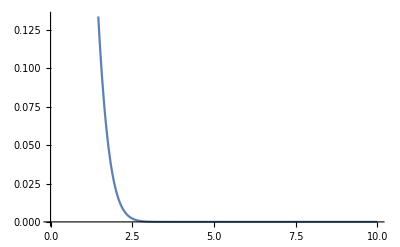

```mathematica
Plot[h1[t,1],{t,0,10}]
```

We will therefore prefer this functional form!

```mathematica
h2[t_,σ_]:=Exp[-σ(1+t^2)/t] 1/(2 BesselK[1,2σ])
```

```mathematica
Integrate[h2[t,2],{t,0,∞},Assumptions->{σ>0}]
```

1

Test it :

General::munfl: Exp[-4895.11] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9790.21] is too small to represent as a normalized machine number; precision may be lost.

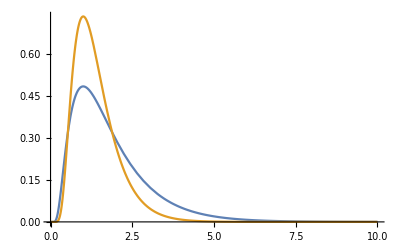

```mathematica
Plot[{h2[t,1],h2[t,2]},{t,0,10},PlotRange->All]
```

Choose which t-function to employ

```mathematica
h[t_,σ_]:=h2[t,σ]
```

## Rust Resources

```mathematica
RegisterExternalEvaluator["Python","/opt/local/Library/Frameworks/Python.framework/Versions/3.9/bin/python3"];
```

```mathematica
RustBindingsPath="/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/uv_alphaloop/Mathematica";
AlphaLoopPath="/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/uv_alphaloop";
```

```mathematica
Get[RustBindingsPath<>"/"<>"RustFromMathematicaV2.m"]
```

Package for accessing alphaLoop implementation in Rust.
This V2 version uses the faster approach of StartExternalSession[Python] to talk to alphaLoop.

Variables you may want to overwrite are:

RFM$LTDFolder = <Path>;
RFM$PythonInterpreter = <Path>;
RFM$CUBAPath = <Path>;
RFM$SCSPath=<Path>;
RFM$ECOSPath=<Path>;

The function: 
RFM$GetLTDHook[name_,OptionsPattern[
{
RunMode->'LTD',
HyperparametersPath->'LTD/hyperparameters.yaml',
TopologiesPath->'LTD/topologies.yaml',
AmplitudesPath->'LTD/anplitudes.yaml',
DEBUG->False
}

Allows you to generate a hook, which will automatically be placed in the list:

RFM$AllHooksStarted

Then you can test that one hook is active with:

RFM$CheckHookStatus[hook_]

And use them to access information from Rust with the following three API entry points (for now):

RFM$GetLTDDeformation[hook_, RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetCrossSectionDeformation[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetRescaling[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$Parameterize[hook_,LoopIndex_,ECM_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$InvParameterize[hook_,LoopIndex_,ECM_,Momentum_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$Evaluate[hook_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateCut[hook_,CutID_,scalingFactor_, scalingFactorJacobian_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateIntegrand[hook_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]

Set your environment variables as follows:

RFM$CUBAPath = "<PATHTO>/Cuba-4.2/lib";
RFM$SCSPath="<PATHTO>/scs/out";
RFM$ECOSPath="<PATHTO>/ecos";
RFM$DYLDPATHS=RFM$CUBAPath<>":"<>RFM$SCSPath<>":"<>RFM$ECOSPath;

and then call:
RFM$SetEnvironment[];

Specify the LTD folder to the hook package:

```mathematica
RFM$LTDFolder=AlphaLoopPath;
RFM$PythonInterpreter = "/opt/local/Library/Frameworks/Python.framework/Versions/3.9/bin/python3";
RFM$CUBAPath = "/Users/vjhirsch/HEP_programs/Cuba-4.2/lib";
RFM$SCSPath="/Users/vjhirsch/HEP_programs/scs/out";
RFM$ECOSPath="/Users/vjhirsch/HEP_programs/ecos";
RFM$DYLDPATHS=RFM$CUBAPath<>":"<>RFM$SCSPath<>":"<>RFM$ECOSPath;
```

```mathematica
RFM$SetEnvironment[];
```

Make sure a stat folder exists in the local directory:

```mathematica
If[Not[DirectoryQ[NotebookDirectory[]<>"/stats"]],CreateDirectory[NotebookDirectory[]<>"stats"]];
```

```mathematica
InvParametrize[hook_,moms_, OptionsPattern[{ECM->1}]]:=Block[{xs,jac,tmp},
tmp=Table[
RFM$InvParameterize[hook,iMom-1,OptionValue[ECM]^2,moms⟦iMom⟧]
,{iMom,Length[moms]}
];
xs=Join@@Table[invP["Xs"],{invP, tmp}];
jac=Times@@Join@@Table[invP["Jacobian"],{invP, tmp}];
<|"xs"->xs,"jac"->jac|>
]

GetRescaling[hook_,cutID_, moms_]:=Block[{RescalingSolutions},
RescalingSolutions=RFM$GetRescaling[hook,cutID,moms];
If[RescalingSolutions["tSolutions"]⟦1⟧>0,
{RescalingSolutions["tSolutions"]⟦1⟧,RescalingSolutions["tJacobians"]⟦1⟧},
{RescalingSolutions["tSolutions"]⟦2⟧,RescalingSolutions["tJacobians"]⟦2⟧}
]
]
```

```mathematica
Q0ForThisSection=Total[RFM$LoadYaml[AlphaLoopPath<>"/yaml_hyperparameters/epem_a_ttx_NNLO_hyperparameters.yaml"]["CrossSection"]["incoming_momenta"]]⟦1⟧;
```

```mathematica
EvaluateFullIntegrand[hook_, moms_,OptionsPattern[{ECM->1}]]:=Module[{xs},
xs=InvParametrize[hook,moms,ECM->OptionValue[ECM]];
RFM$EvaluateIntegrand[hook,xs["xs"]]xs["jac"]
]
EvaluateCut[hook_,cutID_, moms_,OptionsPattern[{ECM->1}]]:=Module[{rescaling},
If[cutID≥0,
rescaling=GetRescaling[hook, cutID, moms];
RFM$EvaluateCut[hook,cutID,rescaling⟦1⟧,rescaling⟦2⟧,moms,DEBUG->False,f128->True],
EvaluateFullIntegrand[hook,moms,ECM->OptionValue[ECM]]
]
]
```

```mathematica
ExtractPower[evals_,OptionsPattern[{StabThres->0.001}]]:=Block[
{fitRes,localEvals},
localEvals=Select[evals,((Abs[Re[#⟦2⟧]])!=0.)&];
If[Or[Length[localEvals]==0,AllTrue[localEvals,((Abs[Re[#⟦2⟧]])==0.)&]],
0.,
fitRes=CoefficientList[Fit[Table[{-Log10[ev⟦1⟧],Log10[Abs[Re[ev⟦2⟧]]]},{ev,localEvals}],{1,x,x^2},x],x];
If[Abs[fitRes⟦3⟧/fitRes⟦2⟧]>OptionValue[StabThres],
If[Abs[fitRes⟦2⟧/fitRes⟦1⟧]>OptionValue[StabThres],
Print["WARNING: unstable fit with extracted {1,x,x^2} coefficients being: "<>ToString[fitRes,InputForm]];
];
];
fitRes⟦2⟧
]
]
```

```mathematica
ClearAll[ComputeARustLimit];

ComputeARustLimit[headRes_,itgs_,vecs_,limitName_,OptionsPattern[{minPower->3,maxPower->6,nSteps->50,IncludeSoft->True,ShowLast->True,StabThreshold->0.001,DEBUG->False,ECM->1}]]:=Block[
{newRes,evalRes,tmpRes,powerObtained,strRes},
newRes={limitName};
PrintTemporary["Computing "<>limitName<>" limit..."];

newRes=Join[newRes,Table[
evalRes=Table[
tmpRes=
Total[Table[
itgComponent["weight"]EvaluateCut[itgComponent["hook"],itgComponent["cutID"],
MapMomentumToRustLMB[Q0ForThisSection/100(vecs/.{eps->10^-epspower})],ECM->OptionValue[ECM]
],{itgComponent,itg⟦2⟧}]

];
{N[10^-epspower],tmpRes},
{epspower,OptionValue[minPower],OptionValue[maxPower],(OptionValue[maxPower]-OptionValue[minPower])/OptionValue[nSteps]}
];
If[OptionValue[DEBUG],Print["List of results for limit "<>limitName<>" with itg "<>itg⟦1⟧<>" :"];Print[TableForm[evalRes]];];
powerObtained=Round[ExtractPower[
evalRes
,StabThres->OptionValue[StabThreshold]
],0.001];
If[OptionValue[DEBUG],Print["Resulting in a power fit of "<>ToString[powerObtained,InputForm]]];
(*strRes="p="<>ToString[powerObtained]<>"|s="<>If[Sign[Total[Table[ev⟦2⟧,{ev,evalRes}]]]>0,"+1","-1"];*)
strRes=If[OptionValue[ShowLast],
"p="<>ToString[powerObtained]<>" | last="<>ToString[Re[evalRes⟦-1⟧⟦2⟧],InputForm],
"p="<>ToString[powerObtained]
];
If[OptionValue[DEBUG],Print["Final string result for this:"<>strRes]];
strRes,
{itg,itgs}
]
];
PrintTemporary[Grid[Join[{headRes},{newRes}],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]];
newRes
]
```

```mathematica
ClearAll[TestCompareRustvsMM];
TestCompareRustvsMM[pts_,itgs_,OptionsPattern[{ECM->1,PHASE->Re}]]:=Block[
{tmpRes,allNumRes,allRes, RustRes,MMRes},
allRes={{"Comparison"}};
allRes⟦-1⟧=Join[allRes⟦-1⟧,Table[pt⟦1⟧,{pt,pts}]];

allNumRes=Table[
Table[
Total[
Table[

If[
KeyExistsQ[itgComponent,"hook"],

(* Rust evaluation *)
RustRes=itgComponent["weight"]((OptionValue[PHASE])@EvaluateCut[itgComponent["hook"],itgComponent["cutID"],
MapMomentumToRustLMB[pt⟦2⟧],ECM->OptionValue[ECM]
]);
(*Print[RustRes];*)
RustRes
,

(* MM evaluation *)
MMRes=itgComponent["weight"] N[(itgComponent["function"]@@Join[pt⟦2⟧,itgComponent["extra_args"]]),20];
(*Print[MMRes];*)
MMRes
],
{itgComponent,itg⟦2⟧}]
],
{itg,itgs}
],
{pt,pts}
];

allRes=Join[allRes,
Flatten[Table[
If[Iitg==1,
{Join[{itgs⟦Iitg⟧⟦1⟧},Table[nr⟦Iitg⟧,{nr,allNumRes}]]}
,
Join[{
Join[{itgs⟦Iitg⟧⟦1⟧},Table[nr⟦Iitg⟧,{nr,allNumRes}]],
Join[{"ratio: "<>itgs⟦Iitg⟧⟦1⟧<>" / "<>itgs⟦1⟧⟦1⟧},Table[If[nr⟦1⟧≠0.,nr⟦Iitg⟧/nr⟦1⟧,0.],{nr,allNumRes}]]
},
If[Length[pts]>1,
{Join[{itgs⟦Iitg⟧⟦1⟧<>" ( ratio@pt<i> / ratio@"<>pts⟦1⟧⟦1⟧<>" )"},
Table[
If[Ipt==1,"N/A",
If[And[allNumRes⟦1⟧⟦1⟧≠0,(allNumRes⟦1⟧⟦Iitg⟧/allNumRes⟦1⟧⟦1⟧)≠0],
(allNumRes⟦Ipt⟧⟦Iitg⟧/allNumRes⟦Ipt⟧⟦1⟧)/(allNumRes⟦1⟧⟦Iitg⟧/allNumRes⟦1⟧⟦1⟧)
,"N/A"]
]
,{Ipt,Length[allNumRes]}]
]}
,
{}]
]
]
,{Iitg,Length[itgs]}
],1]
];

Grid[allRes,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]

]
```

## NLO SE

## -Graphics-

### -Graphics-

```mathematica
h[t_,sigma_]:=Exp[-t^2/(2 sigma^2)]/(Sqrt[2 Pi] sigma)
```

```mathematica
treal[k_,l_,q_,q0_]:=q0/(myNorm[k+l]+myNorm[l]+myNorm[k])
```

```mathematica
real[k_,l_,q_,q0_]:=(1/(2(k0+l0)2(-l0)2(-k0+q0))1/(mySP[{k0,k[[1]],k[[2]],k[[3]]},{k0,k[[1]],k[[2]],k[[3]]}]^2))/.{l0->-myNorm[l],k0->q0-myNorm[k-q]}

realLU[k_,l_,q_,q0_]:=(t^6/(myNorm[k+l]+myNorm[l]+myNorm[k])*real[t*k,t*l,q,q0])/.{t->treal[k,l,q,q0]}
```

### -Graphics-

```mathematica
D[(k[0]+l[0])^2-TensorExpand[(k+l).(k+l)],k[0]]
```

2 (k[0]+l[0])

```mathematica
tvirtual[k_,l_,q_,q0_]:=q0/(2myNorm[k])
```

```mathematica
tvirtualA[k_,l_,m_,q_,q0_]:=q0/(2myNorm[k])
tvirtualB[k_,l_,m_,q_,q0_]:=(t/.Solve[t myNorm[k]+Sqrt[t^2(k⟦1⟧^2+k⟦2⟧^2+k⟦3⟧^2)+m^2]-q0==0,{t}]⟦1⟧)
```

```mathematica
(*virtualBubble[k_,l_,q_,q0_]:=((1/(2 l0 mySP[{k0,k[[1]],k[[2]],k[[3]]}+{l0,l[[1]],l[[2]],l[[3]]},{k0,k[[1]],k[[2]],k[[3]]}+{l0,l[[1]],l[[2]],l[[3]]}])/.{l0->myNorm[l]})+(1/(2 (k0+l0)mySP[{l0,l[[1]],l[[2]],l[[3]]},{l0,l[[1]],l[[2]],l[[3]]}])/.{l0->-k0+myNorm[k+l]}))/.{k0->q0-myNorm[k-q]}*)
```

```mathematica
virtualBubblecLTD=cLTD[prop[kIN+lIN,0]prop[kIN+lIN,0]prop[lIN,0](-D[(kIN[0]+lIN[0])^2-TensorExpand[(kIN+lIN).(kIN+lIN)],kIN[0]]),loopmom->{lIN}];
virtualBubblecLTDNoDerivative=cLTD[prop[kIN+lIN,0]prop[lIN,0],loopmom->{lIN}];
virtualBubbleDerivative[k_,l_,q_,q0_]:=Block[
{cLTDexpr },
cLTDexpr=(virtualBubblecLTD/.{kIN->k,lIN->l});
cLTDexpr=Simplify[cLTDexpr⟦1⟧/.{den[x_]:>1/x,cLTDnorm[x_]:>ⅈ/x}]/.cLTDexpr⟦2⟧;
(1/((2k[0])(2(-k[0]+q0)))(1/(2k[0])cLTDexpr))/.{k[0]->myNorm[k]}
]
virtualBubble[k_,l_,q_,q0_]:=Block[
{cLTDexprNoDerivative },
cLTDexprNoDerivative=(virtualBubblecLTDNoDerivative/.{kIN->k,lIN->l});
cLTDexprNoDerivative=Simplify[cLTDexprNoDerivative⟦1⟧/.{den[x_]:>1/x,cLTDnorm[x_]:>ⅈ/x}]/.cLTDexprNoDerivative⟦2⟧;
(cLTDexprNoDerivative)/.{k[0]->myNorm[k]}
]
```

```mathematica
virtualBubbleBis[k_,k0_,l_,q_,q0_]:=Block[
{cLTDexprNoDerivative },
cLTDexprNoDerivative=(virtualBubblecLTDNoDerivative/.{kIN->k,lIN->l});
cLTDexprNoDerivative=Simplify[cLTDexprNoDerivative⟦1⟧/.{den[x_]:>1/x,cLTDnorm[x_]:>ⅈ/x}]/.cLTDexprNoDerivative⟦2⟧;
(cLTDexprNoDerivative)/.{k[0]->k0}
]
```

```mathematica
realOSCT[k_,l_,q_,q0_]:=(
real[k,l,q,q0]-
((1/(2(-myNorm[k]+q0))((1/(2(k0+l0)2(-l0)))(1/(mySP[{k0,k[[1]],k[[2]],k[[3]]},{k0,k[[1]],k[[2]],k[[3]]}]^2))))/.{l0->-myNorm[l],k0->q0-myNorm[k-q]})
)
```

```mathematica
realOSCTLU[k_,l_,q_,q0_]:=((t^6/(myNorm[k+l]+myNorm[l]+myNorm[k])*realOSCT[t*k,t*l,q,q0])/.{t->treal[k,l,q,q0]})
```

```mathematica
PhSpMeasure[k_,l_,q_,q0_]:=1/((2k0)(2(q0-k0)))/.{k0->q0-myNorm[k-q]};
(*
PhSpMeasure[k_,l_,q_,q0_]:=1/((2(q0-k0)))/.{k0->q0-myNorm[k-q]};
virtualBubbleLU[k_,l_,q_,q0_]:=(1/(4 myNorm[k]^2 q0^2)D[ts^6virtualBubble[ts*k,ts*l,q,q0]*PhSpMeasure[ts*k,ts*l,q,q0],ts])/.{ts->tvirtual[k,l,q,q0],ta->tvirtual[k,l,q,q0]}
*)
```

```mathematica
myCT[k0_,k_,l_]:=((1/(2(k0+l0)2(-l0)))/.{l0->myNorm[tCT l]})/.{tCT->k0/(2myNorm[l])}
```

```mathematica
myCTLU[k_,l_,q_,q0_]:=((tv^6/(myNorm[k]+myNorm[k])*(myCT[myNorm[tv k],tv k,tv l]))/.{tv->tvirtual[k,l,q,q0]});
```

```mathematica
virtualBubbleLUA[k_,l_,m_,q_,q0_]:=((t^6/(myNorm[k]+myNorm[k])*1/((2k0)(2(-k0+q0)))*1/(k0^2-t^2(k.k)-m^2)virtualBubbleBis[t*k,k0,t*l,q,q0])/.{k0->myNorm[t k]})/.{t->tvirtualA[k,l,m,q,q0]}
virtualBubbleLUB[k_,l_,m_,q_,q0_]:=((t^6*((1/D[ttmp myNorm[k]+Sqrt[ttmp^2(k⟦1⟧^2+k⟦2⟧^2+k⟦3⟧^2)+m^2]-q0,ttmp])/.{ttmp->t})*1/((2k0)(2(-k0+q0)))*1/(k0^2-t^2(k).(k))virtualBubbleBis[t*k,k0,t*l,q,q0])/.{k0->Sqrt[(t^2 k.k+m^2)]})/.{t->tvirtualB[k,l,m,q,q0]}
```

```mathematica
virtualBubbleLU[k_,l_,q_,q0_]:=(t^6/(myNorm[k]+myNorm[k])*virtualBubbleDerivative[t*k,t*l,q,q0])/.{t->tvirtual[k,l,q,q0]}
virtualBubbleExtraLU[k_,l_,q_,q0_]:=(1/(4 myNorm[k]^2 q0^2))((D[ts^6(virtualBubble[t*k,ts*l,q,q0]/.{t->tvirtual[k,l,q,q0]})PhSpMeasure[ts*k,ts*l,q,q0],ts])/.{ts->tvirtual[k,l,q,q0]})
```

```mathematica
ks={0,0,3/4};
ls=-{0,0,1/2};
```

```mathematica
tvirtualB[ks,ls+1{0,1,0},λ,{0,0,0},2]
```

1/3 (4-λ^2)

```mathematica
Series[virtualBubbleLUB[ks,ls+1{0,1,0},λ,{0,0,0},2],{λ,0,3}]
```

(128 (2 √5+√17))/(81 √85 (7+√85) λ^2)-(32 ((2 √5+√17) (5+2 √85)))/(81 (√85 (7+√85)^2))+(8 (2 √5+√17) (215+14 √85) λ^2)/(81 √85 (7+√85)^3)+O[λ]^4

```mathematica
Series[virtualBubbleLUB[ks,ls+1{0,1,0},λ,{0,0,0},2],{λ,0,3}]
```

(128 (2 √5+√17))/(81 √85 (7+√85) λ^2)-(32 ((2 √5+√17) (5+2 √85)))/(81 (√85 (7+√85)^2))+(8 (2 √5+√17) (215+14 √85) λ^2)/(81 √85 (7+√85)^3)+O[λ]^4

```mathematica
Series[virtualBubbleLUA[ks,ls+1{0,1,0},λ,{0,0,0},2],{λ,0,3}]
```

-(128 (2 √5+√17))/(81 (√85 (7+√85)) λ^2)+O[λ]^4

```mathematica
Series[virtualBubbleLUA[ks,ls+eps{0,1,0},λ,{0,0,0},2]+virtualBubbleLUB[ks,ls+eps{0,1,0},λ,{0,0,0},2],{λ,0,0}]
```

-(32 ((2 √(1+4 eps^2)+√(1+16 eps^2)) (-11+16 eps^2+2 √(1+4 eps^2) √(1+16 eps^2))))/(81 (√(1+4 eps^2) √(1+16 eps^2) (-1+8 eps^2+√(1+4 eps^2) √(1+16 eps^2))^2))+O[λ]^1

```mathematica
Series[Normal[Series[virtualBubbleLUA[ks,ls+eps{0,1,0},λ,{0,0,0},2]+virtualBubbleLUB[ks,ls+eps{0,1,0},λ,{0,0,0},2],{λ,0,0}]],{eps,0,10}]
```

8/(243 eps^4)-64/(243 eps^2)+152/81-(5344 eps^2)/243+(72440 eps^4)/243-(344960 eps^6)/81+(5049520 eps^8)/81-(74985152 eps^10)/81+O[eps]^11

```mathematica
Series[virtualBubbleLUZeno[ks,ls+eps{0,1,0},{0,0,0},2],{eps,0,10}]
```

virtualBubbleLUZeno[{0,0,3/4},{0,0,-1/2},{0,0,0},2]+virtualBubbleLUZeno^({0,0,0},{0,1,0},{0,0,0},0)[{0,0,3/4},{0,0,-1/2},{0,0,0},2] eps+1/2 virtualBubbleLUZeno^({0,0,0},{0,2,0},{0,0,0},0)[{0,0,3/4},{0,0,-1/2},{0,0,0},2] eps^2+1/6 virtualBubbleLUZeno^({0,0,0},{0,3,0},{0,0,0},0)[{0,0,3/4},{0,0,-1/2},{0,0,0},2] eps^3+1/24 virtualBubbleLUZeno^({0,0,0},{0,4,0},{0,0,0},0)[{0,0,3/4},{0,0,-1/2},{0,0,0},2] eps^4+1/120 virtualBubbleLUZeno^({0,0,0},{0,5,0},{0,0,0},0)[{0,0,3/4},{0,0,-1/2},{0,0,0},2] eps^5+1/720 virtualBubbleLUZeno^({0,0,0},{0,6,0},{0,0,0},0)[{0,0,3/4},{0,0,-1/2},{0,0,0},2] eps^6+(virtualBubbleLUZeno^({0,0,0},{0,7,0},{0,0,0},0)[{0,0,3/4},{0,0,-1/2},{0,0,0},2] eps^7)/5040+(virtualBubbleLUZeno^({0,0,0},{0,8,0},{0,0,0},0)[{0,0,3/4},{0,0,-1/2},{0,0,0},2] eps^8)/40320+(virtualBubbleLUZeno^({0,0,0},{0,9,0},{0,0,0},0)[{0,0,3/4},{0,0,-1/2},{0,0,0},2] eps^9)/362880+(virtualBubbleLUZeno^({0,0,0},{0,10,0},{0,0,0},0)[{0,0,3/4},{0,0,-1/2},{0,0,0},2] eps^10)/3628800+O[eps]^11

```mathematica
Series[virtualBubbleLU[ks,ls+eps{0,1,0},{0,0,0},2],{eps,0,2}]

Series[virtualBubbleExtraLU[ks,ls+eps{0,1,0},{0,0,0},2],{eps,0,2}]

Series[realOSCTLU[ks,ls+eps{0,1,0},{0,0,0},2],{eps,0,2}]

Series[myCTLU[ks,ls+eps{0,1,0},{0,0,0},2],{eps,0,2}]

Series[-virtualBubbleLU[ks,ls+eps{0,1,0},{0,0,0},2]+realOSCTLU[ks,ls+eps{0,1,0},{0,0,0},2],{eps,0,2}]

Series[realLU[ks,ls+eps{0,1,0},{0,0,0},2],{eps,0,2}]
```

8/(243 eps^4)-32/(243 eps^2)+296/243-(3712 eps^2)/243+O[eps]^3

32/(243 eps^2)-352/243+(2080 eps^2)/81+O[eps]^3

32/(243 eps^2)-160/81+(6368 eps^2)/243+O[eps]^3

-8192/6561+O[eps]^3

-8/(243 eps^4)+64/(243 eps^2)-776/243+(1120 eps^2)/27+O[eps]^3

8/(243 eps^4)-64/(243 eps^2)+8/3-32 eps^2+O[eps]^3

We’re subtracting too much here, because you could think of having a spherical parameterisation for the integration over the spatial momentum of l, with the polar direction given by the spatial momentum of k, in which case the measure would be: |l|^2 sin(θ_kl)dϕ_kl dθ_kl d|l|where we can write sin(θ_kl)=Sqrt[1-(cos(θ_kl))^2] and cos(θ_kl)=(k.l)/(|k||l|)meaning that the measure would contain Sqrt[(1-((ks.kl)/(myNorm[ks]myNorm[kl]))^2)] in which case the expansion becomes:

```mathematica
Series[(Hold[realLU[k,l,{0,0,0},2]])/.{k->ks,l->(ls+eps{0,1,0})}//ReleaseHold,{eps,0,2},Assumptions->{eps>0}]
```

8/(243 eps^4)-64/(243 eps^2)+8/3-32 eps^2+O[eps]^3

```mathematica
ks={0,0,3/4};
ls=-{0,0,1/2};
ks=(3/4){1,2,1};
ls=-(1/2){1,2,1};
```

```mathematica
N[Series[(Hold[(Sqrt[(1-((k.l)/(myNorm[k]myNorm[l]))^2)]realLU[k,l,{0,0,0},2])]/.{k->ks,l->(ls+eps{0,1,0})})//ReleaseHold,{eps,0,2},Assumptions->{eps>0}]]
```

0.00950371/(eps+0.)^3+0.0126716/(eps+0.)^2-0.00527984/(eps+0.)-0.00563183-0.00214127 (eps+0.)-0.0059056 (eps+0.)^2+O[eps+0.]^3

```mathematica
N[Series[(Hold[(Sqrt[(1-((k.l)/(myNorm[k]myNorm[l]))^2)]virtualBubbleLU[k,l,{0,0,0},2])]/.{k->ks,l->(ls+eps{0,1,0})})//ReleaseHold,{eps,0,2},Assumptions->{eps>0}]]
```

0.00950371/(eps+0.)^3+0.0126716/(eps+0.)^2-0.0031679/(eps+0.)-0.00422387-0.00272792 (eps+0.)-0.00504518 (eps+0.)^2+O[eps+0.]^3

```mathematica
Series[realLU[ks,ls+eps{0,1,0},{0,0,0},2],{eps,0,2}]
```

8/(243 eps^4)-64/(243 eps^2)+8/3-32 eps^2+O[eps]^3

```mathematica
Series[virtualBubbleLU[ks,ls+eps{0,1,0},{0,0,0},2],{eps,0,2}]
```

8/(243 eps^4)-32/(243 eps^2)+296/243-(3712 eps^2)/243+O[eps]^3

## NNLO metro

## -Graphics-

### A1:-Graphics-

```mathematica
VHprops=prop[m+k,0]^2*prop[m,0]*prop[m+q,0]*prop[k+l+m,0]*prop[l,0];

VHdiag=cLTD[VHprops,loopmom->{l,m},EvalAll->True];
VHf[k0s_,ks_,ls_,ms_,qs_,q0s_]:=VHdiag[[1]]/.VHdiag[[2]]/.{k[0]->k0s}/.{q[0]->q0s}/.{m->{ms[[1]],ms[[2]],ms[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},k->{ks[[1]],ks[[2]],ks[[3]]},q->{qs[[1]],qs[[2]],qs[[3]]}};
```

```mathematica
VHintegrandA[k_,l_,m_,q_,q0_]:=(f[k0,k,l,m,q,q0]/(4 k0(q0-k0)))/.{k0->myNorm[k]}
```

```mathematica
VHtAv[k_,l_,m_,q_,q0_]:=q0/(2myNorm[k])
VHjAv[k_,l_,m_,q_,q0_]:=2myNorm[k]
```

```mathematica
VHintegrandLUA[k_,l_,m_,q_,q0_]:=(t^9/VHjAv[k,l,m,q,q0] VHintegrandA[t*k,t*l,t*m,q,q0])/.{t->VHtAv[k,l,m,q,q0]}
```

```mathematica
Series[VHintegrandLUA[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2}]
```

1.40486/eps^4-0.803116/eps^3-1.63281/eps^2+1.41141/eps+1.04928-1.50568 eps+5.52133 eps^2+O[eps]^3

```mathematica
VHOSCTitgApropsOutter = prop[m+k,0]^2*prop[m,0]*prop[m+q,0];
VHOSCTitgApropsInner = prop[k+l+m,0]*prop[l,0];
```

```mathematica
VHdiagOutter=cLTD[VHOSCTitgApropsOutter,loopmom->{m},EvalAll->True];
VHdiagInner = cLTD[VHOSCTitgApropsInner,loopmom->{l},EvalAll->True];
```

```mathematica
VHOSCTitgAf[k0s_,ks_,ls_,ms_,qs_,q0s_]:=(
(VHdiagOutter[[1]]/.VHdiagOutter[[2]]/.{k[0]->k0s}/.{q[0]->q0s})/.{m->ms,l->ls,k->ks,q->qs}
)*(
((VHdiagInner⟦1⟧/.VHdiagInner⟦2⟧)/.{m[0]->Sqrt[k.k+2k.m+m.m]-k[0]})/.{m->ms,l->ls,k->ks,q->qs}
)
VHOSCTitgAfdM[k0s_,ks_,ls_,ms_,qs_,q0s_]:=(
(VHdiagOutter[[1]]/.VHdiagOutter[[2]]/.{k[0]->k0s}/.{q[0]->q0s})/.{m->ms,l->ls,k->ks,q->qs}
)*(
ⅈ dM
)
```

```mathematica
VHOSCTitgA[k_,l_,m_,q_,q0_]:=(VHOSCTitgAf[k0,k,l,m,q,q0]/(4 k0(q0-k0)))/.{k0->myNorm[k]}
VHOSCTitgLUA[k_,l_,m_,q_,q0_]:=(t^9/VHjAv[k,l,m,q,q0] VHOSCTitgA[t*k,t*l,t*m,q,q0])/.{t->VHtAv[k,l,m,q,q0]}
VHOSCTitgAdM[k_,l_,m_,q_,q0_]:=((VHOSCTitgAfdM[k0,k,l,m,q,q0]/(4 k0(q0-k0)))/.{k0->myNorm[k]})
VHOSCTitgLUAdM[k_,l_,m_,q_,q0_]:=(t^9/VHjAv[k,l,m,q,q0] VHOSCTitgAdM[t*k,t*l,t*m,q,q0])/.{t->VHtAv[k,l,m,q,q0]}
```

```mathematica
Series[VHOSCTitgLUA[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2}]
Series[VHOSCTitgLUAdM[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2}]
```

(1.40486+0. ⅈ)/eps^4-(0.803116+0. ⅈ)/eps^3-(1.41409+0. ⅈ)/eps^2+(1.19009+0. ⅈ)/eps+(0.718692+0. ⅈ)-(1.01557+0. ⅈ) eps+(6.19747+0. ⅈ) eps^2+O[eps]^3

-(0.5 dM)/eps^4+(1.25 dM)/eps^2+(-2.02083+0. ⅈ) dM+(0.475694+0. ⅈ) dM eps^2+O[eps]^3

```mathematica
VHOSCTitgADerivativeBubbleOuttercLTD= cLTD[prop[m+k,0]*prop[m,0]*prop[m+q,0],loopmom->{m},EvalAll->True];
VHOSCTitgADerivativeBubblecLTD = cLTD[prop[kpm+l,0]^2 prop[l,0](-2(kpm[0]+l[0])),loopmom->{l},EvalAll->True];
```

```mathematica
VHOSCTitgADerivativeBubblef[k0s_,ks_,ls_,ms_,qs_,q0s_]:=((
(VHOSCTitgADerivativeBubbleOuttercLTD[[1]]/.VHOSCTitgADerivativeBubbleOuttercLTD[[2]]/.{k[0]->k0s}/.{q[0]->q0s})/.{m->ms,l->ls,k->ks,q->qs}
)*(
(1/(2(kpm[0]))(VHOSCTitgADerivativeBubblecLTD⟦1⟧/.VHOSCTitgADerivativeBubblecLTD⟦2⟧))/.{kpm[0]->Sqrt[k.k+2k.m+m.m]})/.{kpm->{ks⟦1⟧+ms⟦1⟧,ks⟦2⟧+ms⟦2⟧,ks⟦3⟧+ms⟦3⟧},m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
VHOSCTitgADerivativeBubble[k_,l_,m_,q_,q0_]:=(VHOSCTitgADerivativeBubblef[k0,k,l,m,q,q0]/(4 k0(q0-k0)))/.{k0->myNorm[k]}
VHOSCTitgLUADerivativeBubble[k_,l_,m_,q_,q0_]:=(t^9/VHjAv[k,l,m,q,q0] VHOSCTitgADerivativeBubble[t*k,t*l,t*m,q,q0])/.{t->VHtAv[k,l,m,q,q0]}
```

```mathematica
Series[VHOSCTitgLUADerivativeBubble[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2}]
```

-(0.218723+0. ⅈ)/eps^2+(0.221319+0. ⅈ)/eps+(0.306071+0. ⅈ)-(0.453935+0. ⅈ) eps-(0.659602+0. ⅈ) eps^2+O[eps]^3

```mathematica
Series[VHOSCTitgLUADerivativeBubble[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1]+VHOSCTitgLUA[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2}]
```

(1.40486+0. ⅈ)/eps^4-(0.803116+0. ⅈ)/eps^3-(1.63281+0. ⅈ)/eps^2+(1.41141+0. ⅈ)/eps+(1.02476+0. ⅈ)-(1.4695+0. ⅈ) eps+(5.53787+0. ⅈ) eps^2+O[eps]^3

### A2:-Graphics-

```mathematica
VHprops2=prop[m+k,0]^2*prop[k,0]*prop[k-q,0]*prop[k+l+m,0]*prop[l,0];

VHdiag2=cLTD[props2,loopmom->{k,l},EvalAll->True];
VHf2[ks_,ls_,m0s_,ms_,qs_,q0s_]:=VHdiag2[[1]]/.VHdiag2[[2]]/.{m[0]->m0s}/.{q[0]->q0s}/.{m->{ms[[1]],ms[[2]],ms[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},k->{ks[[1]],ks[[2]],ks[[3]]},q->{qs[[1]],qs[[2]],qs[[3]]}};
```

```mathematica
VHintegrandA2[k_,l_,m_,q_,q0_]:=(VHf2[k,l,m0,m,q,q0]/(4(- m0)(q0+m0)))/.{m0->-myNorm[m]}
```

```mathematica
VHtAv2[k_,l_,m_,q_,q0_]:=q0/(2myNorm[m])
VHjAv2[k_,l_,m_,q_,q0_]:=2myNorm[m]
```

```mathematica
VHintegrandLUA2[k_,l_,m_,q_,q0_]:=(t^9/VHjAv2[k,l,m,q,q0] VHintegrandA2[t*k,t*l,t*m,q,q0])/.{t->VHtAv2[k,l,m,q,q0]}
```

```mathematica
Series[VHintegrandLUA2[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2}]
Series[VHintegrandLUA2[{0,eps,1},{0.31,0.43,0.5},{0,0,-1.5},{0,0,0},1],{eps,0,2}]
```

-0.825705+0.439733 eps+7.79767 eps^2+O[eps]^3

0.180877/eps^4-0.437014/eps^3+0.764072/eps^2-0.669498/eps-1.28792+5.00717 eps-4.6016 eps^2+O[eps]^3

```mathematica
VHOSCTitgA2propsOutter = prop[m+k,0]^2*prop[k,0]*prop[k-q,0];
VHOSCTitgA2propsInner = prop[k+l+m,0]*prop[l,0];
```

```mathematica
VHdiagOutter2=cLTD[VHOSCTitgA2propsOutter,loopmom->{k},EvalAll->True];
VHdiagInner2 = cLTD[VHOSCTitgA2propsInner,loopmom->{l},EvalAll->True];
```

```mathematica
VHOSCTitgA2f[ks_,ls_,m0s_,ms_,qs_,q0s_]:=(
(VHdiagOutter2[[1]]/.VHdiagOutter2[[2]]/.{m[0]->m0s}/.{q[0]->q0s})/.{m->ms,l->ls,k->ks,q->qs}
)*(
((VHdiagInner2⟦1⟧/.VHdiagInner2⟦2⟧)/.{m[0]->Sqrt[k.k+2k.m+m.m]-k[0]})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
VHOSCTitgA2[k_,l_,m_,q_,q0_]:=(VHOSCTitgA2f[k,l,m0,m,q,q0]/(4 (-m0)(q0+m0)))/.{m0->-myNorm[m]}
VHOSCTitgLUA2[k_,l_,m_,q_,q0_]:=(t^9/VHjAv2[k,l,m,q,q0] VHOSCTitgA2[t*k,t*l,t*m,q,q0])/.{t->VHtAv2[k,l,m,q,q0]}
```

```mathematica
Series[VHOSCTitgLUA2[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2},Assumptions->{eps>0}]
Series[VHOSCTitgLUA2[{0,eps,1},{0.31,0.43,0.5},{0,0,-1.5},{0,0,0},1],{eps,0,2},Assumptions->{eps>0}]
```

-(0.907304+0. ⅈ)+(0.518679+0. ⅈ) eps+(8.23999+0. ⅈ) eps^2+O[eps]^3

(0.180877+0. ⅈ)/eps^4-(0.437014+0. ⅈ)/eps^3+(0.967372+0. ⅈ)/eps^2-(1.47179+0. ⅈ)/eps+(0.453941+0. ⅈ)+(2.57045+0. ⅈ) eps-(2.80988+0. ⅈ) eps^2+O[eps]^3

```mathematica
VHOSCTitgA2DerivativeBubbleOuttercLTD= cLTD[prop[m+k,0]*prop[k,0]*prop[k-q,0],loopmom->{k},EvalAll->True];
VHOSCTitgA2DerivativeBubblecLTD = cLTD[prop[kpm+l,0]^2 prop[l,0](-2(kpm[0]+l[0])),loopmom->{l},EvalAll->True];
```

```mathematica
VHOSCTitgA2DerivativeBubblef[ks_,ls_,m0s_,ms_,qs_,q0s_]:=((
(VHOSCTitgA2DerivativeBubbleOuttercLTD[[1]]/.VHOSCTitgA2DerivativeBubbleOuttercLTD[[2]]/.{m[0]->m0s}/.{q[0]->q0s})/.{m->ms,l->ls,k->ks,q->qs}
)*(
(1/(2(kpm[0]))(VHOSCTitgA2DerivativeBubblecLTD⟦1⟧/.VHOSCTitgA2DerivativeBubblecLTD⟦2⟧))/.{kpm[0]->Sqrt[k.k+2k.m+m.m]})/.{kpm->{ks⟦1⟧+ms⟦1⟧,ks⟦2⟧+ms⟦2⟧,ks⟦3⟧+ms⟦3⟧},m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
VHOSCTitgA2DerivativeBubble[k_,l_,m_,q_,q0_]:=(VHOSCTitgA2DerivativeBubblef[k,l,m0,m,q,q0]/(4 (-m0)(q0+m0)))/.{m0->-myNorm[m]}
VHOSCTitgLUA2DerivativeBubble[k_,l_,m_,q_,q0_]:=(t^9/VHjAv2[k,l,m,q,q0] VHOSCTitgA2DerivativeBubble[t*k,t*l,t*m,q,q0])/.{t->VHtAv2[k,l,m,q,q0]}
```

```mathematica
Series[VHOSCTitgLUA2DerivativeBubble[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2}]
Series[VHOSCTitgLUA2DerivativeBubble[{0,eps,1},{0.31,0.43,0.5},{0,0,-1.5},{0,0,0},1],{eps,0,2}]
```

0.0911347-0.0922163 eps-0.457133 eps^2+O[eps]^3

-0.2033/eps^2+0.80229/eps-1.90794+3.37119 eps-4.78043 eps^2+O[eps]^3

```mathematica
Series[VHOSCTitgLUA2DerivativeBubble[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1]+VHOSCTitgLUA2[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2}]
Series[VHOSCTitgLUA2DerivativeBubble[{0,eps,1},{0.31,0.43,0.5},{0,0,-1.5},{0,0,0},1]+VHOSCTitgLUA2[{0,eps,1},{0.31,0.43,0.5},{0,0,-1.5},{0,0,0},1],{eps,0,2}]
```

-(0.81617+0. ⅈ)+(0.426463+0. ⅈ) eps+(7.78286+0. ⅈ) eps^2+O[eps]^3

(0.180877+0. ⅈ)/eps^4-(0.437014+0. ⅈ)/eps^3+(0.764072+0. ⅈ)/eps^2-(0.669498+0. ⅈ)/eps-(1.454+0. ⅈ)+(5.94164+0. ⅈ) eps-(7.59031+0. ⅈ) eps^2+O[eps]^3

### B1:-Graphics-

```mathematica
VHtBv[k_,l_,m_,q_,q0_]:=q0/(myNorm[m]+myNorm[m+k]+myNorm[k])
VHjBv[k_,l_,m_,q_,q0_]:=myNorm[m]+myNorm[m+k]+myNorm[k]
```

```mathematica
VHintegrandB1[k_,l_,m_,q_,q0_]:=(1/(2 (-m0) 2 (-k0+q0) )/.{m0->-myNorm[m]}/.{k0->q0-myNorm[k-q]})

VHbubble[k_,l_,m_,q_,q0_]:=
(((1/(2l0 mySP[{k0,k[[1]],k[[2]],k[[3]]}+{l0,l[[1]],l[[2]],l[[3]]}+{m0,m[[1]],m[[2]],m[[3]]},{k0,k[[1]],k[[2]],k[[3]]}+{l0,l[[1]],l[[2]],l[[3]]}+{m0,m[[1]],m[[2]],m[[3]]}]))/.{l0->myNorm[l]})
+((1/(2(k0+l0+m0) mySP[{l0,l[[1]],l[[2]],l[[3]]},{l0,l[[1]],l[[2]],l[[3]]}]))/.{l0->-k0-m0+myNorm[k+l+m]}))/.{m0->-myNorm[m]}/.{k0->q0-myNorm[k-q]}


VHintegrandB3[k_,l_,m_,q_,q0_]:=(1/(mySP[{m0,m[[1]],m[[2]],m[[3]]}+{q0,q[[1]],q[[2]],q[[3]]},{m0,m[[1]],m[[2]],m[[3]]}+{q0,q[[1]],q[[2]],q[[3]]}] mySP[{k0,k[[1]],k[[2]],k[[3]]},{k0,k[[1]],k[[2]],k[[3]]}]))/.{m0->-myNorm[m]}/.{k0->q0-myNorm[k-q]}
```

```mathematica
VHintegrandLUB[k_,l_,m_,q_,q0_]:=D[(t^9/((VHjBv[k,l,m,q,q0]*(t(VHjBv[k,l,m,q,q0]-2myNorm[k+m]) -q0))^2)VHbubble[t*k,t*l,t*m,q,q0]*VHintegrandB3[t*k,t*l,t*m,q,q0]VHintegrandB1[t*k,t*l,t*m,q,q0]),t]/.{t->VHtBv[k,l,m,q,q0]}
```

```mathematica
Series[VHintegrandLUB[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2}]
```

-0.702429/eps^4+0.401558/eps^3+0.816405/eps^2-0.705703/eps+0.0238156+0.456306 eps-7.67404 eps^2+O[eps]^3

Quickly check NLO collinear and compare against single-collinear of NNLO limit:

```mathematica
Series[VHintegrandLUB[{-1,-1,1},{0,eps,1},{1,1,-4},{0,0,0},1],{eps,0,2},Assumptions->{eps>0}]//N
```

0.0000778677/(eps+0.)^4-0.000168861/(eps+0.)^2+0.0000579398-0.000038583 (eps+0.)^2+O[eps+0.]^3

And compare against target:

```mathematica
Series[integrandLUC[{-1,-1,1},{0,eps,1},{1,1,-4},{0,0,0},1],{eps,0,2},Assumptions->{eps>0}]//N
```

0.0000778677/(eps+0.)^4-0.000168861/(eps+0.)^2+0.000314512-0.000565945 (eps+0.)^2+O[eps+0.]^3

```mathematica
VHitgB1BubblecLTD = cLTD[prop[kpm+l,0]^2 prop[l,0](-2(kpm[0]+l[0])),loopmom->{l},EvalAll->True];
```

```mathematica
VHitgB1BubbleBubblef[ks_,ls_,ms_,qs_,q0s_]:=(
((ⅈ/(2(kpm[0]))(VHitgB1BubblecLTD⟦1⟧/.VHitgB1BubblecLTD⟦2⟧))/.{kpm[0]->Sqrt[k.k+2k.m+m.m]})/.{kpm->{ks⟦1⟧+ms⟦1⟧,ks⟦2⟧+ms⟦2⟧,ks⟦3⟧+ms⟦3⟧},m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
VHitgB1[k_,l_,m_,q_,q0_]:=((1/((2myNorm[k+ m])*(-2myNorm[ m])*(-2(myNorm[ k-q]))))*
((1/mySP[Join[{k0}, k],Join[{k0},k]] 1/mySP[Join[{m0+q0},m+q],Join[{m0+q0},m+q]])/.{m0->(-myNorm[m])}/.{k0->(-(myNorm[k-q]-q0))})*
VHitgB1BubbleBubblef[k,l,m,q,q0]
)
```

```mathematica
VHitgLUB1[k_,l_,m_,q_,q0_]:=(t^9*(1/VHjBv[k,l,m,q,q0])*VHitgB1[t*k,t*l,t*m,q,q0])/.{t->VHtBv[k,l,m,q,q0]}
```

```mathematica
Series[VHitgLUB1[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2}]
```

0.109362/eps^2-0.11066/eps-0.21683+0.291519 eps+0.618809 eps^2+O[eps]^3

```mathematica
Series[VHitgLUB1[{-1,-1,1},{0,eps,1},{1,1,-4},{0,0,0},1],{eps,0,2},Assumptions->{eps>0}]//N
```

0.0000778677/(eps+0.)^4-0.0000194669/(eps+0.)^2+0.0000112543-8.82094×10^-6 (eps+0.)^2+O[eps+0.]^3

### B2:-Graphics-

```mathematica
VHtBv2[k_,l_,m_,q_,q0_]:=q0/(myNorm[m]+myNorm[m+k]+myNorm[k])
VHjBv2[k_,l_,m_,q_,q0_]:=myNorm[m]+myNorm[m+k]+myNorm[k]
```

```mathematica
VHintegrandB12[k_,l_,m_,q_,q0_]:=(1/(2 (k0) 2 (m0+q0) )/.{k0->myNorm[k]}/.{m0->-q0+myNorm[m+q]})

VHbubble2[k_,l_,m_,q_,q0_]:=
(((1/(2l0 mySP[{k0,k[[1]],k[[2]],k[[3]]}+{l0,l[[1]],l[[2]],l[[3]]}+{m0,m[[1]],m[[2]],m[[3]]},{k0,k[[1]],k[[2]],k[[3]]}+{l0,l[[1]],l[[2]],l[[3]]}+{m0,m[[1]],m[[2]],m[[3]]}]))/.{l0->myNorm[l]})
+((1/(2(k0+l0+m0) mySP[{l0,l[[1]],l[[2]],l[[3]]},{l0,l[[1]],l[[2]],l[[3]]}]))/.{l0->-k0-m0+myNorm[k+l+m]}))/.{k0->myNorm[k]}/.{m0->-q0+myNorm[m+q]}


VHintegrandB32[k_,l_,m_,q_,q0_]:=(1/(mySP[{k0,k[[1]],k[[2]],k[[3]]}-{q0,q[[1]],q[[2]],q[[3]]},{k0,k[[1]],k[[2]],k[[3]]}-{q0,q[[1]],q[[2]],q[[3]]}] mySP[{m0,m[[1]],m[[2]],m[[3]]},{m0,m[[1]],m[[2]],m[[3]]}]))/.{k0->myNorm[k]}/.{m0->-q0+myNorm[m+q]}
```

```mathematica
VHintegrandLUB2[k_,l_,m_,q_,q0_]:=D[(t^9/((jBv2[k,l,m,q,q0]*(t(jBv2[k,l,m,q,q0]-2myNorm[k+m]) -q0))^2)*bubble2[t*k,t*l,t*m,q,q0]*VHintegrandB32[t*k,t*l,t*m,q,q0]*VHintegrandB12[t*k,t*l,t*m,q,q0]),t]/.{t->tBv[k,l,m,q,q0]}
```

```mathematica
Series[VHintegrandLUB2[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2}]
```

-0.702429/eps^4+0.401558/eps^3+0.816405/eps^2-0.705703/eps+0.0238156+0.456306 eps-7.67404 eps^2+O[eps]^3

Quickly check NLO collinear and compare against single-collinear of NNLO limit:

```mathematica
Series[VHintegrandLUB2[{-1,-1,1},{0,eps,1},{1,1,-4},{0,0,0},1],{eps,0,2},Assumptions->{eps>0}]//N
```

0.0000778677/(eps+0.)^4-0.000168861/(eps+0.)^2+0.0000579398-0.000038583 (eps+0.)^2+O[eps+0.]^3

And compare against target:

```mathematica
Series[integrandLUC[{-1,-1,1},{0,eps,1},{1,1,-4},{0,0,0},1],{eps,0,2},Assumptions->{eps>0}]//N
```

0.0000778677/(eps+0.)^4-0.000168861/(eps+0.)^2+0.000314512-0.000565945 (eps+0.)^2+O[eps+0.]^3

```mathematica
VHitgB2BubblecLTD = cLTD[prop[kpm+l,0]^2 prop[l,0](-2(kpm[0]+l[0])),loopmom->{l},EvalAll->True];
```

```mathematica
VHitgB2BubbleBubblef[ks_,ls_,ms_,qs_,q0s_]:=(
((-ⅈ/(2(kpm[0]))(VHitgB2BubblecLTD⟦1⟧/.VHitgB2BubblecLTD⟦2⟧))/.{kpm[0]->Sqrt[k.k+2k.m+m.m]})/.{kpm->{ks⟦1⟧+ms⟦1⟧,ks⟦2⟧+ms⟦2⟧,ks⟦3⟧+ms⟦3⟧},m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
VHitgB2[k_,l_,m_,q_,q0_]:=((1/((-2myNorm[k+ m])*(2myNorm[ m+q])*(2(myNorm[ k]))))*
((1/mySP[Join[{k0-q0}, k-q],Join[{k0-q0},k-q]] 1/mySP[Join[{m0},m],Join[{m0},m]])/.{k0->myNorm[k]}/.{m0->-q0+myNorm[m+q]})*
VHitgB2BubbleBubblef[k,l,m,q,q0]
)
```

```mathematica
VHitgLUB2[k_,l_,m_,q_,q0_]:=(t^9*(1/VHjBv2[k,l,m,q,q0])*VHitgB2[t*k,t*l,t*m,q,q0])/.{t->VHtBv2[k,l,m,q,q0]}
```

```mathematica
Series[VHitgLUB2[{0,eps,1},{0.31,0.43,0.5},{0,0,-0.5},{0,0,0},1],{eps,0,2}]
```

0.109362/eps^2-0.11066/eps-0.21683+0.291519 eps+0.618809 eps^2+O[eps]^3

```mathematica
Series[VHitgLUB2[{-1,-1,1},{0,eps,1},{1,1,-4},{0,0,0},1],{eps,0,2},Assumptions->{eps>0}]//N
```

0.0000778677/(eps+0.)^4-0.0000194669/(eps+0.)^2+0.0000112543-8.82094×10^-6 (eps+0.)^2+O[eps+0.]^3

### C1:-Graphics-

```mathematica
VHtCv[k_,l_,m_,q_,q0_]:=q0/(myNorm[m]+myNorm[k+l+m]+myNorm[l]+myNorm[k])
VHjCv[k_,l_,m_,q_,q0_]:=myNorm[m]+myNorm[k+l+m]+myNorm[l]+myNorm[k]
```

```mathematica
VHleftCLTD[k_,l_,m_,q_,q0_]:=1/(mySP[{m0,m[[1]],m[[2]],m[[3]]}+{q0,q[[1]],q[[2]],q[[3]]},{m0,m[[1]],m[[2]],m[[3]]}+{q0,q[[1]],q[[2]],q[[3]]}]*mySP[{m0,m[[1]],m[[2]],m[[3]]}+{k0,k[[1]],k[[2]],k[[3]]},{m0,m[[1]],m[[2]],m[[3]]}+{k0,k[[1]],k[[2]],k[[3]]}])/.{k0->q0-myNorm[k-q]}/.{m0->-myNorm[m]}/.{l0->-myNorm[l]}
VHrightCLTD[k_,l_,m_,q_,q0_]:=1/(mySP[{k0,k[[1]],k[[2]],k[[3]]},{k0,k[[1]],k[[2]],k[[3]]}]*mySP[{m0,m[[1]],m[[2]],m[[3]]}+{k0,k[[1]],k[[2]],k[[3]]},{m0,m[[1]],m[[2]],m[[3]]}+{k0,k[[1]],k[[2]],k[[3]]}])/.{k0->q0-myNorm[k-q]}/.{m0->-myNorm[m]}/.{l0->-myNorm[l]}

VHenergiesC[k_,l_,m_,q_,q0_]:=1/(16 (-m0) (-l0) (-k0+q0)(k0+l0+m0))/.{k0->q0-myNorm[k-q]}/.{m0->-myNorm[m]}/.{l0->-myNorm[l]}
```

```mathematica
VHintegrandLUC[k_,l_,m_,q_,q0_]:=((t^9/VHjCv[k,l,m,q,q0])*(VHleftCLTD[t*k,t*l,t*m,q,q0]*VHrightCLTD[t*k,t*l,t*m,q,q0]*VHenergiesC[t*k,t*l,t*m,q,q0]))/.{t->VHtCv[k,l,m,q,q0]}
```

### C2:-Graphics-

```mathematica
VHtCv2[k_,l_,m_,q_,q0_]:=q0/(myNorm[m]+myNorm[k+l+m]+myNorm[l]+myNorm[k])
VHjCv2[k_,l_,m_,q_,q0_]:=myNorm[m]+myNorm[k+l+m]+myNorm[l]+myNorm[k]
```

```mathematica
VHleftCLTD2[k_,l_,m_,q_,q0_]:=1/(mySP[{k0,k[[1]],k[[2]],k[[3]]}-{q0,q[[1]],q[[2]],q[[3]]},{k0,k[[1]],k[[2]],k[[3]]}-{q0,q[[1]],q[[2]],q[[3]]}]*mySP[{m0,m[[1]],m[[2]],m[[3]]}+{k0,k[[1]],k[[2]],k[[3]]},{m0,m[[1]],m[[2]],m[[3]]}+{k0,k[[1]],k[[2]],k[[3]]}])/.{k0->myNorm[k-q]}/.{m0->-q0+myNorm[m]}/.{l0->myNorm[l]}
VHrightCLTD2[k_,l_,m_,q_,q0_]:=1/(mySP[{m0,m[[1]],m[[2]],m[[3]]},{m0,m[[1]],m[[2]],m[[3]]}]*mySP[{m0,m[[1]],m[[2]],m[[3]]}+{k0,k[[1]],k[[2]],k[[3]]},{m0,m[[1]],m[[2]],m[[3]]}+{k0,k[[1]],k[[2]],k[[3]]}])/.{k0->myNorm[k-q]}/.{m0->-q0+myNorm[m]}/.{l0->myNorm[l]}

VHenergiesC2[k_,l_,m_,q_,q0_]:=1/(16 (k0) (l0) (m0+q0)(-k0-l0-m0))/.{k0->myNorm[k-q]}/.{m0->-q0+myNorm[m]}/.{l0->myNorm[l]}
```

```mathematica
VHintegrandLUC2[k_,l_,m_,q_,q0_]:=((t^9/VHjCv2[k,l,m,q,q0])*(VHleftCLTD2[t*k,t*l,t*m,q,q0]*VHrightCLTD2[t*k,t*l,t*m,q,q0]*VHenergiesC2[t*k,t*l,t*m,q,q0]))/.{t->VHtCv2[k,l,m,q,q0]}
```

### Test limits

```mathematica
ClearAll[ks,ls,ms]
ks={0,eps,1};
ls={3,1,1};
ms={0,0,-1/2};
```

```mathematica
N[Series[VHintegrandLUA[ks,ls,ms,{0,0,0},1],{eps,0,0}],20]
N[Series[VHintegrandLUB[ks,ls,ms,{0,0,0},1],{eps,0,0}],20]
N[Series[VHintegrandLUC[ks,ls,ms,{0,0,0},1],{eps,0,0}],20]
N[Series[VHintegrandLUA2[ks,ls,ms,{0,0,0},1],{eps,0,0}],20]
N[Series[VHintegrandLUB2[ks,ls,ms,{0,0,0},1],{eps,0,0}],20]
N[Series[VHintegrandLUC2[ks,ls,ms,{0,0,0},1],{eps,0,0}],20]
```

0.025412016798732989756/eps^4-0.0031511013740029237101/eps^3-0.026280937124830049679/eps^2+0.0034635988675104209147/eps+0.018001011259861457322+O[eps]^1

-0.012706008399366494878/eps^4+0.0015755506870014618551/eps^3+0.01314046856241502484/eps^2-0.0017317994337552104573/eps+0.0017733571137165151926+O[eps]^1

1.0908324082547852321×10^-7+O[eps]^1

-0.016298349636780432734+O[eps]^1

-0.012706008399366494878/eps^4+0.0015755506870014618551/eps^3+0.01314046856241502484/eps^2-0.0017317994337552104573/eps+0.0017733571137165151926+O[eps]^1

1.0908324082547852321×10^-7+O[eps]^1

```mathematica
N[Series[VHintegrandLUA[ks,ls,ms,{0,0,0},1]+VHintegrandLUB[ks,ls,ms,{0,0,0},1]-2VHintegrandLUC[ks,ls,ms,{0,0,0},1]+VHintegrandLUA2[ks,ls,ms,{0,0,0},1]+VHintegrandLUB2[ks,ls,ms,{0,0,0},1]-2VHintegrandLUC2[ks,ls,ms,{0,0,0},1],{eps,0,2}],30]
```

Series::ztest1: Unable to decide whether numeric quantity … is equal to zero. Assuming it is.

0.00524893951755075305872866286365-0.00064709280966604246436293511131 eps-0.0387829805628174792172278230095 eps^2+O[eps]^3

```mathematica
N[Series[VHintegrandLUA[ks,ls,ms,{0,0,0},1]-VHOSCTitgLUA[ks,ls,ms,{0,0,0},1],{eps,0,0}],20]
N[Series[VHitgLUB1[ks,ls,ms,{0,0,0},1],{eps,0,0}],20]
N[Series[VHintegrandLUC[ks,ls,ms,{0,0,0},1],{eps,0,0}],20]
N[Series[VHintegrandLUA2[ks,ls,ms,{0,0,0},1]-VHOSCTitgLUA2[ks,ls,ms,{0,0,0},1],{eps,0,0}],20]
N[Series[VHitgLUB2[ks,ls,ms,{0,0,0},1],{eps,0,0}],20]
N[Series[VHintegrandLUC2[ks,ls,ms,{0,0,0},1],{eps,0,0}],20]
```

-0.00027492439211905725364/eps^2+0.000057261958727235939278/eps+0.00046698458666814301472+O[eps]^1

0.00013746219605952862682/eps^2-0.000028630979363617969639/eps-0.00031267839081237536224+O[eps]^1

1.0908324082547852321×10^-7+O[eps]^1

0.00011357787906795648335+O[eps]^1

0.00013746219605952862682/eps^2-0.000028630979363617969639/eps-0.00031267839081237536224+O[eps]^1

1.0908324082547852321×10^-7+O[eps]^1

```mathematica
Total[Table[i@@{1,2,3},{i,{a,b}}]]
```

a[1,2,3]+b[1,2,3]

```mathematica
ZenoCompleteIntegrandNNLOmetro[k_,l_,m_,q_,q0_]:=Table[itg⟦1⟧*(itg⟦2⟧@@{k,l,m,q,q0}),{itg,{
{+1,VHintegrandLUA},
{+1,VHintegrandLUB},
{-1,VHintegrandLUC},
{+1,VHintegrandLUA2},
{+1,VHintegrandLUB2},
{-1,VHintegrandLUC2}
}}]
```

```mathematica
Total[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2}],20]]
```

0.005249157684032404016-0.0006471657817787070514 eps-0.0387830972529997675 eps^2+O[eps]^3

```mathematica
VHCompleteIntegrandNNLOmetro[k_,l_,m_,q_,q0_]:=Table[itg⟦1⟧*(itg⟦2⟧@@{k,l,m,q,q0}),{itg,{
{+1,VHintegrandLUA},{-1,VHOSCTitgLUA},
{+1,VHitgLUB1},
{-1,VHintegrandLUC},
{+1,VHintegrandLUA2},{-1,VHOSCTitgLUA2},
{+1,VHitgLUB2},
{-1,VHintegrandLUC2}
}}]
```

```mathematica
Total[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2}],20]]
```

-0.00004501248237030218+9.3136711385687215×10^-6 eps+0.0001645664535321618 eps^2+O[eps]^3

```mathematica
ks={eps,-1,1};
ls=-{eps,0,1};
ms={0,1,1};
```

```mathematica
Total[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2}],20]]
Total[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2}],20]]
```

0.00016395822149751218-0.000260746944497201206 eps^2+O[eps]^3

-0.000809010864009951267/eps^2+0.000871842727506219542-0.000745883956816231725 eps^2+O[eps]^3

```mathematica
ks={eps,3/2,1};
ls=-{eps,0,1};
ms={0,-3/2,1};
```

```mathematica
Total[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2}],20]]
Total[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2}],20]]
```

2.0562540492387431×10^-8-3.8574082276135403×10^-8 eps^2+O[eps]^3

-5.272446280099341×10^-9+8.4915078694797215×10^-9 eps^2+O[eps]^3

```mathematica
(*SOFT POINT OF BUBBLE |k+l+m|=0*)
```

```mathematica
ks={eps,0,3.};
ls=-{0,eps,1.};
ms={0,0,-2.};
```

```mathematica
Total[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}],20]]
Total[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}],20]]
```

-(3.46945×10^-18)/eps^6+(3.31721×10^13)/eps^5-0.0130208/eps^4+(2.65802×10^44)/eps^3+0.00977467/eps^2+(2.12982×10^75)/eps-0.0052446+O[eps]^1

-(6.93889×10^-18+0. ⅈ)/eps^6+(2.60209×10^-18+0. ⅈ)/eps^5+(0.000651042+0. ⅈ)/eps^4-(0.00153452+0. ⅈ)/eps^3-(5.21667×10^27+0. ⅈ)/eps^2+(2.95335×10^43+0. ⅈ)/eps-(1.254×10^59+0. ⅈ)+O[eps]^1

```mathematica
TableForm[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}],20]]
TableForm[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}],20]]
```

0.0117187/eps^6+0.00552427/eps^5-0.0130208/eps^4-0.00145779/eps^3+0.00977467/eps^2-0.00193264/eps-0.0052446+O[eps]^1
(1.65861×10^13)/eps^5+(4.695×10^28)/eps^4+(1.32901×10^44)/eps^3+(3.76201×10^59)/eps^2+(1.06491×10^75)/eps+3.01443×10^90+O[eps]^1
-(2.60833×10^27)/eps^2+(1.47668×10^43)/eps-6.27002×10^58+O[eps]^1
-0.00219266/eps+0.00233732+O[eps]^1
-0.0117187/eps^6+(1.65861×10^13)/eps^5-(4.695×10^28)/eps^4+(1.32901×10^44)/eps^3-(3.76201×10^59)/eps^2+(1.06491×10^75)/eps-3.01443×10^90+O[eps]^1
-(2.60833×10^27)/eps^2+(1.47668×10^43)/eps-6.27002×10^58+O[eps]^1

0.0117187/eps^6+0.00552427/eps^5-0.0130208/eps^4-0.00145779/eps^3+0.00977467/eps^2-0.00193264/eps-0.0052446+O[eps]^1
-(0.0117187+0. ⅈ)/eps^6-(0.00828641+0. ⅈ)/eps^5+(0.0136719+0. ⅈ)/eps^4+(0.00552427+0. ⅈ)/eps^3-(0.0116699+0. ⅈ)/eps^2-(0.00238234+0. ⅈ)/eps+(0.00816895+0. ⅈ)+O[eps]^1
0.00138107/eps^5-(1.4456×10^-19)/eps^4-0.0028005/eps^3+0.000976563/eps^2+0.00335996/eps-0.00198025+O[eps]^1
-(2.60833×10^27)/eps^2+(1.47668×10^43)/eps-6.27002×10^58+O[eps]^1
-0.00219266/eps+0.00233732+O[eps]^1
0.000925926/eps^2+0.000654729/eps-0.00279578+O[eps]^1
0.00138107/eps^5-(1.4456×10^-19)/eps^4-0.0028005/eps^3+0.000976563/eps^2+0.00335996/eps-0.00198025+O[eps]^1
-(2.60833×10^27)/eps^2+(1.47668×10^43)/eps-6.27002×10^58+O[eps]^1

```mathematica
TableForm[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2}],20]]
```

0.181818/eps^6-0.556818/eps^4+2.57567/eps^2-14.8153+95.8104 eps^2+O[eps]^3
-0.09/eps^6+0.273375/eps^4-1.25882/eps^2+7.25216-46.9904 eps^2+O[eps]^3
-0.000909091/eps^6+0.00503409/eps^4-0.0290123/eps^2+0.177521-1.14638 eps^2+O[eps]^3
-0.0340169+0.361996 eps^2+O[eps]^3
-0.09/eps^6+0.273375/eps^4-1.25882/eps^2+7.25216-46.9904 eps^2+O[eps]^3
-0.000909091/eps^6+0.00503409/eps^4-0.0290123/eps^2+0.177521-1.14638 eps^2+O[eps]^3

```mathematica
ks={0,0,0.5};
ls={eps,1/2,-1/2};
ms={eps,0,-1};
```

```mathematica
Total[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2}],20]]
Total[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2}],20]]
```

-(1.33227×10^-15)/eps^4-(4.08562×10^-14)/eps^2+0.278349-3.15163 eps^2+O[eps]^3

-(8.88178×10^-16+0. ⅈ)/eps^2-(0.0338521+0. ⅈ)+(0.344468+0. ⅈ) eps^2+O[eps]^3

NNLO limits

```mathematica
ks={0,3eps,5};
ls={2eps,0,3};
ms={0,0,-1};
```

```mathematica
Total[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2},Assumptions->{eps>0}],20]]
Total[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2},Assumptions->{eps>0}],20]]
```

2.0562540492387431×10^-8-3.8574082276135403×10^-8 eps^2+O[eps]^3

-5.272446280099341×10^-9+8.4915078694797215×10^-9 eps^2+O[eps]^3

```mathematica
TableForm[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2},Assumptions->{eps>0}],20]]
TableForm[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,2},Assumptions->{eps>0}],20]]
```

$Aborted

$Aborted

Soft-gluon limit:

```mathematica
ks={1.+3eps,2.,3.};
ls={4.,3.,1.};
ms={-1.,-2.,-3.};
```

```mathematica
SetPrecision[Total[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,-2},Assumptions->{eps>0}],20]],60]
SetPrecision[Total[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,-2},Assumptions->{eps>0}],20]],60]
```

-(1.91337×10^10)/eps^5+(1.39325×10^26)/eps^4-(1.06438×10^42)/eps^3+(9.18929×10^57)/eps^2+1/O[eps]

(1.20715×10^-7)/eps^5+(9.36131×10^8)/eps^4-(1.57345×10^24)/eps^3-(9.56128×10^39)/eps^2+0.472804/eps^(3/2)+1/O[eps]

```mathematica
SetPrecision[Total[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,-2},Assumptions->{eps>0}],20]],60]
SetPrecision[Total[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,-2},Assumptions->{eps>0}],20]],60]
```

$Aborted

$Aborted

```mathematica
VHCompleteIntegrandNNLOmetro[k_,l_,m_,q_,q0_]:=Table[itg⟦1⟧*(itg⟦2⟧@@{k,l,m,q,q0}),{itg,{
{+1,VHintegrandLUA},{-1,VHOSCTitgLUA},
{+1,VHitgLUB1},
{-1,VHintegrandLUC},
{+1,VHintegrandLUA2},{-1,VHOSCTitgLUA2},
{+1,VHitgLUB2},
{-1,VHintegrandLUC2}
}}]
```

```mathematica
Total[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}],20]]
```

(2.38419×10^-7+0. ⅈ)/eps^4+(8.05306×10^8+0. ⅈ)/eps^3+0.472804/eps^(3/2)+(4.35561×10^40+0. ⅈ)/eps-(5.68831×10^15)/(√eps)+(1.96159×10^56+9.0072×10^15 ⅈ)+√O[eps]

```mathematica
TableForm[N[SetPrecision[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,1},Assumptions->{eps>0}],60],20]]
```

(1.2071504171777706531×10^-7)/eps^5+(9.3613119947436320782×10^8)/eps^4-(1.5734481615637724906×10^24)/eps^3-(9.5612765540183157225×10^39)/eps^2+(1.4525106637698924218×10^56)/eps-1.2695166255742466511×10^72+9.3684806547102332261×10^87 eps+O[eps]^2
-(1.2071504171777706531×10^-7)/eps^5-(9.361311994743629694×10^8)/eps^4+(1.5734481615637732959×10^24)/eps^3+(9.5612765540183157225×10^39)/eps^2-(1.4525106637698919863×10^56)/eps+1.2695166255742468472×10^72-9.3684806547102349929×10^87 eps+O[eps]^2
(6.8340115864662542939×10^7)/eps^2+0.23640200129593400002/eps^(3/2)-(7.2327237469091551563×10^23)/eps-(2.844154580701253×10^15)/(√eps)+7.6546977038640580795×10^39+3.0843963891296956422×10^31 √eps-8.1012906047436819218×10^55 eps+O[eps]^(3/2)
-1.5264360554102250334×10^-10+3.1451292350485406946×10^-10 eps+O[eps]^2
-(2.1730424229472333988×10^24)/eps+(4.996803593425×10^24-4.6874059851791674704×10^31 ⅈ)-(1.1683898228680791335×10^40-4.2495713602×10^31 ⅈ) eps+O[eps]^2
(2.1730424229472333988×10^24)/eps-(4.996803593425×10^24-4.6874059851791683711×10^31 ⅈ)+(1.1683898228680791335×10^40-4.2495713602×10^31 ⅈ) eps+O[eps]^2
(6.8340115864662542939×10^7)/eps^2+0.23640200129593400002/eps^(3/2)-(7.2327237469091551563×10^23)/eps-(2.844154580701253×10^15)/(√eps)+7.6546977038640580795×10^39+3.0843963891296956422×10^31 √eps-8.1012906047436819218×10^55 eps+O[eps]^(3/2)
-1.5264360554102250334×10^-10+3.1451292350485406946×10^-10 eps+O[eps]^2

```mathematica
TableForm[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,-2},Assumptions->{eps>0}],20]]
```

(1.20715×10^-7)/eps^5+(9.36131×10^8)/eps^4-(1.57345×10^24)/eps^3-(9.56128×10^39)/eps^2+1/O[eps]
-(2.00174×10^10)/eps^5+(1.55061×10^26)/eps^4-(1.22057×10^42)/eps^3+(8.9102×10^57)/eps^2+1/O[eps]
O[eps]^0
1/O[eps]
(8.83626×10^8)/eps^5-(1.57366×10^25)/eps^4+(1.56184×10^41)/eps^3+(2.79093×10^56)/eps^2+1/O[eps]
O[eps]^0

```mathematica
ks={1+2 eps,2+5eps,3-eps};
ls={4-1eps,3,1};
ms={-1,-2,-3};
```

```mathematica
tt=Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}];
```

```mathematica
Print["----- 20"];
N[tt,20]//TableForm
Print["----- 40"];
N[tt,40]//TableForm
Print["----- 20 Total"];
N[Total[tt],20]//TableForm
Print["----- 40 Total"];
N[Total[tt],40]//TableForm
```

----- 20

(1.9296790492123840332×10^-8)/eps^5-(2.0600728112750699397×10^-8)/eps^4+(3.0760466324041157922×10^-8)/eps^3-(4.5870010920373973628×10^-8)/eps^2+(7.541866030878234978×10^-8)/eps-1.2983314869321372904×10^-7+O[eps]^1
-(1.9296790492123840332×10^-8)/eps^5+(2.0600728112750699397×10^-8)/eps^4-(3.4760706353436831811×10^-8)/eps^3+(5.4994140234768830622×10^-8)/eps^2-(9.0540232242125714221×10^-8)/eps+1.5199464587801152732×10^-7+O[eps]^1
(1.2206645575729759864×10^-9)/eps^3-(1.6432022890405445971×10^-9)/eps^2+(8.4633762212777320818×10^-10)/eps+9.5888710195176908476×10^-10+O[eps]^1
-1.526436055410224732×10^-10+O[eps]^1
-(4.5796808174563847222×10^-9)/eps^5+(1.5454492756752772319×10^-8)/eps^4-(3.1701267149149478829×10^-8)/eps^3+(5.2969482150271426439×10^-8)/eps^2-(8.4385690514078239536×10^-8)/eps+1.3835277242920143338×10^-7+O[eps]^1
(4.5796808174563847222×10^-9)/eps^5-(1.5454492756752772319×10^-8)/eps^4+(3.3260178063399200745×10^-8)/eps^3-(5.8807206886585194238×10^-8)/eps^2+(9.6758961476081264552×10^-8)/eps-1.5833589353142608313×10^-7+O[eps]^1
(1.2206645575729759864×10^-9)/eps^3-(1.6432022890405445971×10^-9)/eps^2+(8.4633762212777320818×10^-10)/eps+9.5888710195176908476×10^-10+O[eps]^1
-1.526436055410224732×10^-10+O[eps]^1

----- 40

(1.929679049212384033171286120196439878385×10^-8)/eps^5-(2.060072811275069939749206228285138398885×10^-8)/eps^4+(3.076046632404115792210645500245575751653×10^-8)/eps^3-(4.587001092037397362848309142042386404386×10^-8)/eps^2+(7.541866030878234978023934785965414044267×10^-8)/eps-1.298331486932137290391606396869241009148×10^-7+O[eps]^1
-(1.929679049212384033171286120196439878385×10^-8)/eps^5+(2.060072811275069939749206228285138398885×10^-8)/eps^4-(3.476070635343683181141992727675264694815×10^-8)/eps^3+(5.499414023476883062176760078300116038205×10^-8)/eps^2-(9.054023224212571422142546857701893968597×10^-8)/eps+1.519946458780115273202648462143376976073×10^-7+O[eps]^1
(1.220664557572975986402730286061368576051×10^-9)/eps^3-(1.643202289040544597080598462005688467761×10^-9)/eps^2+(8.463376221277732081790153493616986493097×10^-10)/eps+9.588871019517690847583113019786502229668×10^-10+O[eps]^1
-1.526436055410224732027189924322377667849×10^-10+O[eps]^1
-(4.579680817456384722198881186654588624448×10^-9)/eps^5+(1.545449275675277231853400291754487080628×10^-8)/eps^4-(3.170126714914947882871310662252293348781×10^-8)/eps^3+(5.296948215027142643896421680701302344364×10^-8)/eps^2-(8.438569051407823953590550842266547621097×10^-8)/eps+1.383527724292014333770568879212994564006×10^-7+O[eps]^1
(4.579680817456384722198881186654588624448×10^-9)/eps^5-(1.545449275675277231853400291754487080628×10^-8)/eps^4+(3.326017806339920074522111832469708576732×10^-8)/eps^3-(5.880720688658519423808752924557894284632×10^-8)/eps^2+(9.675896147608126455208429852555482726973×10^-8)/eps-1.583358935314260831306081423092759217223×10^-7+O[eps]^1
(1.220664557572975986402730286061368576051×10^-9)/eps^3-(1.643202289040544597080598462005688467761×10^-9)/eps^2+(8.463376221277732081790153493616986493097×10^-10)/eps+9.588871019517690847583113019786502229668×10^-10+O[eps]^1
-1.526436055410224732027189924322377667849×10^-10+O[eps]^1

----- 20 Total

-(1.0556257270847930086×10^-9)/eps+3.7908630753946417507×10^-9+O[eps]^1

----- 40 Total

-(1.055625727084793008649299915752050885922×10^-9)/eps+3.79086307539464175066413675852995628324×10^-9+O[eps]^1

```mathematica
tt2=Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}];
```

```mathematica
Print["----- 20"];
N[tt2,20]//TableForm
Print["----- 40"];
N[tt2,40]//TableForm
Print["----- 20 Total"];
N[Total[tt2],20]//TableForm
Print["----- 40 Total"];
N[Total[tt2],40]//TableForm
```

----- 20

(1.9296790492123840332×10^-8)/eps^5-(2.0600728112750699397×10^-8)/eps^4+(3.0760466324041157922×10^-8)/eps^3-(4.5870010920373973628×10^-8)/eps^2+(7.541866030878234978×10^-8)/eps-1.2983314869321372904×10^-7+O[eps]^1
-(7.3585548373337278048×10^-9)/eps^5+(2.5731176779989635395×10^-9)/eps^4+(1.3852760426943143941×10^-9)/eps^3-(5.4649422912311365781×10^-9)/eps^2+(4.3047533650204055908×10^-9)/eps+2.7939794281696613406×10^-9+O[eps]^1
-1.526436055410224732×10^-10+O[eps]^1
-(4.5796808174563847222×10^-9)/eps^5+(1.5454492756752772319×10^-8)/eps^4-(3.1701267149149478829×10^-8)/eps^3+(5.2969482150271426439×10^-8)/eps^2-(8.4385690514078239536×10^-8)/eps+1.3835277242920143338×10^-7+O[eps]^1
-(7.3585548373337278048×10^-9)/eps^5+(2.5731176779989635395×10^-9)/eps^4+(1.3852760426943143941×10^-9)/eps^3-(5.4649422912311365781×10^-9)/eps^2+(4.3047533650204055908×10^-9)/eps+2.7939794281696613406×10^-9+O[eps]^1
-1.526436055410224732×10^-10+O[eps]^1

----- 40

(1.929679049212384033171286120196439878385×10^-8)/eps^5-(2.060072811275069939749206228285138398885×10^-8)/eps^4+(3.076046632404115792210645500245575751653×10^-8)/eps^3-(4.587001092037397362848309142042386404386×10^-8)/eps^2+(7.541866030878234978023934785965414044267×10^-8)/eps-1.298331486932137290391606396869241009148×10^-7+O[eps]^1
-(7.358554837333727804756990007654905079699×10^-9)/eps^5+(2.573117677998963539479029682653256591287×10^-9)/eps^4+(1.38527604269431439413271907035203208677×10^-9)/eps^3-(5.464942291231136578075721111873300592922×10^-9)/eps^2+(4.304753365020405590804549894804301810197×10^-9)/eps+2.793979428169661340553502079672338154757×10^-9+O[eps]^1
-1.526436055410224732027189924322377667849×10^-10+O[eps]^1
-(4.579680817456384722198881186654588624448×10^-9)/eps^5+(1.545449275675277231853400291754487080628×10^-8)/eps^4-(3.170126714914947882871310662252293348781×10^-8)/eps^3+(5.296948215027142643896421680701302344364×10^-8)/eps^2-(8.438569051407823953590550842266547621097×10^-8)/eps+1.383527724292014333770568879212994564006×10^-7+O[eps]^1
-(7.358554837333727804756990007654905079699×10^-9)/eps^5+(2.573117677998963539479029682653256591287×10^-9)/eps^4+(1.38527604269431439413271907035203208677×10^-9)/eps^3-(5.464942291231136578075721111873300592922×10^-9)/eps^2+(4.304753365020405590804549894804301810197×10^-9)/eps+2.793979428169661340553502079672338154757×10^-9+O[eps]^1
-1.526436055410224732027189924322377667849×10^-10+O[eps]^1

----- 20 Total

(1.8297512602803078817×10^-9)/eps^3-(3.8304133525648203457×10^-9)/eps^2-(3.5752347525507857406×10^-10)/eps+1.3802295381244982073×10^-8+O[eps]^1

----- 40 Total

(1.829751260280307881658786520636888202264×10^-9)/eps^3-(3.830413352564820345670316837157441786059×10^-9)/eps^2-(3.57523475255078574057060773402732147902×10^-10)/eps+1.38022953812449820725978144088555562618×10^-8+O[eps]^1

```mathematica
ClearAll[ks,ls,ms]
ks={0,eps,1};
ls={3,1,1};
ms={0,0,-1/2};
```

```mathematica
tt=Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}];
```

```mathematica
Print["----- 20"];
N[tt,20]//TableForm
Print["----- 40"];
N[tt,40]//TableForm
Print["----- 20 Total"];
N[Total[tt],20]//TableForm
Print["----- 40 Total"];
N[Total[tt],40]//TableForm
```

----- 20

(1.9296790492123840332×10^-8)/eps^5-(2.0600728112750699397×10^-8)/eps^4+(3.0760466324041157922×10^-8)/eps^3-(4.5870010920373973628×10^-8)/eps^2+(7.541866030878234978×10^-8)/eps-1.2983314869321372904×10^-7+O[eps]^1
-(1.9296790492123840332×10^-8)/eps^5+(2.0600728112750699397×10^-8)/eps^4-(3.4760706353436831811×10^-8)/eps^3+(5.4994140234768830622×10^-8)/eps^2-(9.0540232242125714221×10^-8)/eps+1.5199464587801152732×10^-7+O[eps]^1
(1.2206645575729759864×10^-9)/eps^3-(1.6432022890405445971×10^-9)/eps^2+(8.4633762212777320818×10^-10)/eps+9.5888710195176908476×10^-10+O[eps]^1
-1.526436055410224732×10^-10+O[eps]^1
-(4.5796808174563847222×10^-9)/eps^5+(1.5454492756752772319×10^-8)/eps^4-(3.1701267149149478829×10^-8)/eps^3+(5.2969482150271426439×10^-8)/eps^2-(8.4385690514078239536×10^-8)/eps+1.3835277242920143338×10^-7+O[eps]^1
(4.5796808174563847222×10^-9)/eps^5-(1.5454492756752772319×10^-8)/eps^4+(3.3260178063399200745×10^-8)/eps^3-(5.8807206886585194238×10^-8)/eps^2+(9.6758961476081264552×10^-8)/eps-1.5833589353142608313×10^-7+O[eps]^1
(1.2206645575729759864×10^-9)/eps^3-(1.6432022890405445971×10^-9)/eps^2+(8.4633762212777320818×10^-10)/eps+9.5888710195176908476×10^-10+O[eps]^1
-1.526436055410224732×10^-10+O[eps]^1

----- 40

(1.929679049212384033171286120196439878385×10^-8)/eps^5-(2.060072811275069939749206228285138398885×10^-8)/eps^4+(3.076046632404115792210645500245575751653×10^-8)/eps^3-(4.587001092037397362848309142042386404386×10^-8)/eps^2+(7.541866030878234978023934785965414044267×10^-8)/eps-1.298331486932137290391606396869241009148×10^-7+O[eps]^1
-(1.929679049212384033171286120196439878385×10^-8)/eps^5+(2.060072811275069939749206228285138398885×10^-8)/eps^4-(3.476070635343683181141992727675264694815×10^-8)/eps^3+(5.499414023476883062176760078300116038205×10^-8)/eps^2-(9.054023224212571422142546857701893968597×10^-8)/eps+1.519946458780115273202648462143376976073×10^-7+O[eps]^1
(1.220664557572975986402730286061368576051×10^-9)/eps^3-(1.643202289040544597080598462005688467761×10^-9)/eps^2+(8.463376221277732081790153493616986493097×10^-10)/eps+9.588871019517690847583113019786502229668×10^-10+O[eps]^1
-1.526436055410224732027189924322377667849×10^-10+O[eps]^1
-(4.579680817456384722198881186654588624448×10^-9)/eps^5+(1.545449275675277231853400291754487080628×10^-8)/eps^4-(3.170126714914947882871310662252293348781×10^-8)/eps^3+(5.296948215027142643896421680701302344364×10^-8)/eps^2-(8.438569051407823953590550842266547621097×10^-8)/eps+1.383527724292014333770568879212994564006×10^-7+O[eps]^1
(4.579680817456384722198881186654588624448×10^-9)/eps^5-(1.545449275675277231853400291754487080628×10^-8)/eps^4+(3.326017806339920074522111832469708576732×10^-8)/eps^3-(5.880720688658519423808752924557894284632×10^-8)/eps^2+(9.675896147608126455208429852555482726973×10^-8)/eps-1.583358935314260831306081423092759217223×10^-7+O[eps]^1
(1.220664557572975986402730286061368576051×10^-9)/eps^3-(1.643202289040544597080598462005688467761×10^-9)/eps^2+(8.463376221277732081790153493616986493097×10^-10)/eps+9.588871019517690847583113019786502229668×10^-10+O[eps]^1
-1.526436055410224732027189924322377667849×10^-10+O[eps]^1

----- 20 Total

-(1.0556257270847930086×10^-9)/eps+3.7908630753946417507×10^-9+O[eps]^1

----- 40 Total

-(1.055625727084793008649299915752050885922×10^-9)/eps+3.79086307539464175066413675852995628324×10^-9+O[eps]^1

```mathematica
tt2=Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}];
```

```mathematica
Print["----- 20"];
N[tt2,20]//TableForm
Print["----- 40"];
N[tt2,40]//TableForm
Print["----- 20 Total"];
N[Total[tt2],20]//TableForm
Print["----- 40 Total"];
N[Total[tt2],40]//TableForm
```

----- 20

(1.9296790492123840332×10^-8)/eps^5-(2.0600728112750699397×10^-8)/eps^4+(3.0760466324041157922×10^-8)/eps^3-(4.5870010920373973628×10^-8)/eps^2+(7.541866030878234978×10^-8)/eps-1.2983314869321372904×10^-7+O[eps]^1
-(7.3585548373337278048×10^-9)/eps^5+(2.5731176779989635395×10^-9)/eps^4+(1.3852760426943143941×10^-9)/eps^3-(5.4649422912311365781×10^-9)/eps^2+(4.3047533650204055908×10^-9)/eps+2.7939794281696613406×10^-9+O[eps]^1
-1.526436055410224732×10^-10+O[eps]^1
-(4.5796808174563847222×10^-9)/eps^5+(1.5454492756752772319×10^-8)/eps^4-(3.1701267149149478829×10^-8)/eps^3+(5.2969482150271426439×10^-8)/eps^2-(8.4385690514078239536×10^-8)/eps+1.3835277242920143338×10^-7+O[eps]^1
-(7.3585548373337278048×10^-9)/eps^5+(2.5731176779989635395×10^-9)/eps^4+(1.3852760426943143941×10^-9)/eps^3-(5.4649422912311365781×10^-9)/eps^2+(4.3047533650204055908×10^-9)/eps+2.7939794281696613406×10^-9+O[eps]^1
-1.526436055410224732×10^-10+O[eps]^1

----- 40

(1.929679049212384033171286120196439878385×10^-8)/eps^5-(2.060072811275069939749206228285138398885×10^-8)/eps^4+(3.076046632404115792210645500245575751653×10^-8)/eps^3-(4.587001092037397362848309142042386404386×10^-8)/eps^2+(7.541866030878234978023934785965414044267×10^-8)/eps-1.298331486932137290391606396869241009148×10^-7+O[eps]^1
-(7.358554837333727804756990007654905079699×10^-9)/eps^5+(2.573117677998963539479029682653256591287×10^-9)/eps^4+(1.38527604269431439413271907035203208677×10^-9)/eps^3-(5.464942291231136578075721111873300592922×10^-9)/eps^2+(4.304753365020405590804549894804301810197×10^-9)/eps+2.793979428169661340553502079672338154757×10^-9+O[eps]^1
-1.526436055410224732027189924322377667849×10^-10+O[eps]^1
-(4.579680817456384722198881186654588624448×10^-9)/eps^5+(1.545449275675277231853400291754487080628×10^-8)/eps^4-(3.170126714914947882871310662252293348781×10^-8)/eps^3+(5.296948215027142643896421680701302344364×10^-8)/eps^2-(8.438569051407823953590550842266547621097×10^-8)/eps+1.383527724292014333770568879212994564006×10^-7+O[eps]^1
-(7.358554837333727804756990007654905079699×10^-9)/eps^5+(2.573117677998963539479029682653256591287×10^-9)/eps^4+(1.38527604269431439413271907035203208677×10^-9)/eps^3-(5.464942291231136578075721111873300592922×10^-9)/eps^2+(4.304753365020405590804549894804301810197×10^-9)/eps+2.793979428169661340553502079672338154757×10^-9+O[eps]^1
-1.526436055410224732027189924322377667849×10^-10+O[eps]^1

----- 20 Total

(1.8297512602803078817×10^-9)/eps^3-(3.8304133525648203457×10^-9)/eps^2-(3.5752347525507857406×10^-10)/eps+1.3802295381244982073×10^-8+O[eps]^1

----- 40 Total

(1.829751260280307881658786520636888202264×10^-9)/eps^3-(3.830413352564820345670316837157441786059×10^-9)/eps^2-(3.57523475255078574057060773402732147902×10^-10)/eps+1.38022953812449820725978144088555562618×10^-8+O[eps]^1

```mathematica
ks={eps,3/2,1};
ls=-{eps,0,1};
ms={0,-3/2,1};
```

```mathematica
tt=Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}];
```

```mathematica
Print["----- 20"];
N[tt,20]//TableForm
Print["----- 40"];
N[tt,40]//TableForm
Print["----- 20 Total"];
N[Total[tt],20]//TableForm
Print["----- 40 Total"];
N[Total[tt],40]//TableForm
```

----- 20

(1.9296790492123840332×10^-8)/eps^5-(2.0600728112750699397×10^-8)/eps^4+(3.0760466324041157922×10^-8)/eps^3-(4.5870010920373973628×10^-8)/eps^2+(7.541866030878234978×10^-8)/eps-1.2983314869321372904×10^-7+O[eps]^1
-(1.9296790492123840332×10^-8)/eps^5+(2.0600728112750699397×10^-8)/eps^4-(3.4760706353436831811×10^-8)/eps^3+(5.4994140234768830622×10^-8)/eps^2-(9.0540232242125714221×10^-8)/eps+1.5199464587801152732×10^-7+O[eps]^1
(1.2206645575729759864×10^-9)/eps^3-(1.6432022890405445971×10^-9)/eps^2+(8.4633762212777320818×10^-10)/eps+9.5888710195176908476×10^-10+O[eps]^1
-1.526436055410224732×10^-10+O[eps]^1
-(4.5796808174563847222×10^-9)/eps^5+(1.5454492756752772319×10^-8)/eps^4-(3.1701267149149478829×10^-8)/eps^3+(5.2969482150271426439×10^-8)/eps^2-(8.4385690514078239536×10^-8)/eps+1.3835277242920143338×10^-7+O[eps]^1
(4.5796808174563847222×10^-9)/eps^5-(1.5454492756752772319×10^-8)/eps^4+(3.3260178063399200745×10^-8)/eps^3-(5.8807206886585194238×10^-8)/eps^2+(9.6758961476081264552×10^-8)/eps-1.5833589353142608313×10^-7+O[eps]^1
(1.2206645575729759864×10^-9)/eps^3-(1.6432022890405445971×10^-9)/eps^2+(8.4633762212777320818×10^-10)/eps+9.5888710195176908476×10^-10+O[eps]^1
-1.526436055410224732×10^-10+O[eps]^1

----- 40

(1.929679049212384033171286120196439878385×10^-8)/eps^5-(2.060072811275069939749206228285138398885×10^-8)/eps^4+(3.076046632404115792210645500245575751653×10^-8)/eps^3-(4.587001092037397362848309142042386404386×10^-8)/eps^2+(7.541866030878234978023934785965414044267×10^-8)/eps-1.298331486932137290391606396869241009148×10^-7+O[eps]^1
-(1.929679049212384033171286120196439878385×10^-8)/eps^5+(2.060072811275069939749206228285138398885×10^-8)/eps^4-(3.476070635343683181141992727675264694815×10^-8)/eps^3+(5.499414023476883062176760078300116038205×10^-8)/eps^2-(9.054023224212571422142546857701893968597×10^-8)/eps+1.519946458780115273202648462143376976073×10^-7+O[eps]^1
(1.220664557572975986402730286061368576051×10^-9)/eps^3-(1.643202289040544597080598462005688467761×10^-9)/eps^2+(8.463376221277732081790153493616986493097×10^-10)/eps+9.588871019517690847583113019786502229668×10^-10+O[eps]^1
-1.526436055410224732027189924322377667849×10^-10+O[eps]^1
-(4.579680817456384722198881186654588624448×10^-9)/eps^5+(1.545449275675277231853400291754487080628×10^-8)/eps^4-(3.170126714914947882871310662252293348781×10^-8)/eps^3+(5.296948215027142643896421680701302344364×10^-8)/eps^2-(8.438569051407823953590550842266547621097×10^-8)/eps+1.383527724292014333770568879212994564006×10^-7+O[eps]^1
(4.579680817456384722198881186654588624448×10^-9)/eps^5-(1.545449275675277231853400291754487080628×10^-8)/eps^4+(3.326017806339920074522111832469708576732×10^-8)/eps^3-(5.880720688658519423808752924557894284632×10^-8)/eps^2+(9.675896147608126455208429852555482726973×10^-8)/eps-1.583358935314260831306081423092759217223×10^-7+O[eps]^1
(1.220664557572975986402730286061368576051×10^-9)/eps^3-(1.643202289040544597080598462005688467761×10^-9)/eps^2+(8.463376221277732081790153493616986493097×10^-10)/eps+9.588871019517690847583113019786502229668×10^-10+O[eps]^1
-1.526436055410224732027189924322377667849×10^-10+O[eps]^1

----- 20 Total

-(1.0556257270847930086×10^-9)/eps+3.7908630753946417507×10^-9+O[eps]^1

----- 40 Total

-(1.055625727084793008649299915752050885922×10^-9)/eps+3.79086307539464175066413675852995628324×10^-9+O[eps]^1

```mathematica
tt2=Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}];
```

```mathematica
Print["----- 20"];
N[tt2,20]//TableForm
Print["----- 40"];
N[tt2,40]//TableForm
Print["----- 20 Total"];
N[Total[tt2],20]//TableForm
Print["----- 40 Total"];
N[Total[tt2],40]//TableForm
```

----- 20

(1.9296790492123840332×10^-8)/eps^5-(2.0600728112750699397×10^-8)/eps^4+(3.0760466324041157922×10^-8)/eps^3-(4.5870010920373973628×10^-8)/eps^2+(7.541866030878234978×10^-8)/eps-1.2983314869321372904×10^-7+O[eps]^1
-(7.3585548373337278048×10^-9)/eps^5+(2.5731176779989635395×10^-9)/eps^4+(1.3852760426943143941×10^-9)/eps^3-(5.4649422912311365781×10^-9)/eps^2+(4.3047533650204055908×10^-9)/eps+2.7939794281696613406×10^-9+O[eps]^1
-1.526436055410224732×10^-10+O[eps]^1
-(4.5796808174563847222×10^-9)/eps^5+(1.5454492756752772319×10^-8)/eps^4-(3.1701267149149478829×10^-8)/eps^3+(5.2969482150271426439×10^-8)/eps^2-(8.4385690514078239536×10^-8)/eps+1.3835277242920143338×10^-7+O[eps]^1
-(7.3585548373337278048×10^-9)/eps^5+(2.5731176779989635395×10^-9)/eps^4+(1.3852760426943143941×10^-9)/eps^3-(5.4649422912311365781×10^-9)/eps^2+(4.3047533650204055908×10^-9)/eps+2.7939794281696613406×10^-9+O[eps]^1
-1.526436055410224732×10^-10+O[eps]^1

----- 40

(1.929679049212384033171286120196439878385×10^-8)/eps^5-(2.060072811275069939749206228285138398885×10^-8)/eps^4+(3.076046632404115792210645500245575751653×10^-8)/eps^3-(4.587001092037397362848309142042386404386×10^-8)/eps^2+(7.541866030878234978023934785965414044267×10^-8)/eps-1.298331486932137290391606396869241009148×10^-7+O[eps]^1
-(7.358554837333727804756990007654905079699×10^-9)/eps^5+(2.573117677998963539479029682653256591287×10^-9)/eps^4+(1.38527604269431439413271907035203208677×10^-9)/eps^3-(5.464942291231136578075721111873300592922×10^-9)/eps^2+(4.304753365020405590804549894804301810197×10^-9)/eps+2.793979428169661340553502079672338154757×10^-9+O[eps]^1
-1.526436055410224732027189924322377667849×10^-10+O[eps]^1
-(4.579680817456384722198881186654588624448×10^-9)/eps^5+(1.545449275675277231853400291754487080628×10^-8)/eps^4-(3.170126714914947882871310662252293348781×10^-8)/eps^3+(5.296948215027142643896421680701302344364×10^-8)/eps^2-(8.438569051407823953590550842266547621097×10^-8)/eps+1.383527724292014333770568879212994564006×10^-7+O[eps]^1
-(7.358554837333727804756990007654905079699×10^-9)/eps^5+(2.573117677998963539479029682653256591287×10^-9)/eps^4+(1.38527604269431439413271907035203208677×10^-9)/eps^3-(5.464942291231136578075721111873300592922×10^-9)/eps^2+(4.304753365020405590804549894804301810197×10^-9)/eps+2.793979428169661340553502079672338154757×10^-9+O[eps]^1
-1.526436055410224732027189924322377667849×10^-10+O[eps]^1

----- 20 Total

(1.8297512602803078817×10^-9)/eps^3-(3.8304133525648203457×10^-9)/eps^2-(3.5752347525507857406×10^-10)/eps+1.3802295381244982073×10^-8+O[eps]^1

----- 40 Total

(1.829751260280307881658786520636888202264×10^-9)/eps^3-(3.830413352564820345670316837157441786059×10^-9)/eps^2-(3.57523475255078574057060773402732147902×10^-10)/eps+1.38022953812449820725978144088555562618×10^-8+O[eps]^1

```mathematica
Total[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}],20]]
```

-(1.055625727084793×10^-9)/eps+3.7908630753946418×10^-9+O[eps]^1

```mathematica
TableForm[N[Series[ZenoCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,-2},Assumptions->{eps>0}],20]]
```

$Aborted

```mathematica
VHCompleteIntegrandNNLOmetro[k_,l_,m_,q_,q0_]:=Table[itg⟦1⟧*(itg⟦2⟧@@{k,l,m,q,q0}),{itg,{
{+1,VHintegrandLUA},{0,VHOSCTitgLUA},
{+1,VHitgLUB1},
{-1,VHintegrandLUC},
{+1,VHintegrandLUA2},{0,VHOSCTitgLUA2},
{+1,VHitgLUB2},
{-1,VHintegrandLUC2}
}}]
```

```mathematica
Total[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}],20]]
```

(1.20715×10^-7)/eps^5+(9.36131×10^8)/eps^4-(1.57345×10^24)/eps^3-(9.56128×10^39)/eps^2+0.472804/eps^(3/2)+(1.45251×10^56+0. ⅈ)/eps-(5.68831×10^15)/(√eps)-(1.26952×10^72+4.68741×10^31 ⅈ)+√O[eps]

```mathematica
TableForm[N[Series[VHCompleteIntegrandNNLOmetro[ks,ls,ms,{0,0,0},1],{eps,0,0},Assumptions->{eps>0}],20]]
```

(1.20715×10^-7)/eps^5+(9.36131×10^8)/eps^4-(1.57345×10^24)/eps^3-(9.56128×10^39)/eps^2+(1.45251×10^56)/eps-1.26952×10^72+O[eps]^1
0.+0. ⅈ
(6.83401×10^7)/eps^2+0.236402/eps^(3/2)-(7.23272×10^23)/eps-(2.84415×10^15)/(√eps)+7.6547×10^39+√O[eps]
-1.52644×10^-10+O[eps]^1
-(2.17304×10^24+0. ⅈ)/eps+(4.9968×10^24-4.68741×10^31 ⅈ)+O[eps]^1
0.+0. ⅈ
(6.83401×10^7)/eps^2+0.236402/eps^(3/2)-(7.23272×10^23)/eps-(2.84415×10^15)/(√eps)+7.6547×10^39+√O[eps]
-1.52644×10^-10+O[eps]^1

```mathematica
N[Series[VHitgLUB1[{1.+3eps,2.,3.},{4.,3.,1.},{-1.,-2.,-3.},{0,0,0},1],{eps,0,0},Assumptions->{eps>0}],20]
```

(6.83401×10^7)/eps^2+0.236402/eps^(3/2)-(7.23272×10^23)/eps-(2.84415×10^15)/(√eps)+7.6547×10^39+√O[eps]

## NNLO double-sunrise

## -Graphics-

### Limit definitions

```mathematica
ClearAll[TestDoubleSunriseLimits];
TestDoubleSunriseLimits[itgs_,OptionsPattern[{epsOrder->0,q->{0,0,0},q0->1,precision->20,IncludeSoft->True,IncludeColl->True,SpecifiedLimit->Null,UseFloats->False}]]:=Block[
{ks,ls,ms, tmpRes,allRes,eps,limitName},
allRes={{"Limit"}};
If[Length[itgs]>1,AppendTo[allRes⟦-1⟧,"Sum"]];
allRes⟦-1⟧=Join[allRes⟦-1⟧,Table[itg⟦1⟧,{itg,itgs}]];

If[OptionValue[IncludeColl],

(* NLO limit m//k *)
limitName="NLO m//k";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks=If[OptionValue[UseFloats],SetPrecision[{1,2,3},OptionValue[precision]],{1,2,3}];
ls=If[OptionValue[UseFloats],SetPrecision[{3,4,7},OptionValue[precision]],{3,4,7}];
ms=If[OptionValue[UseFloats],SetPrecision[-1/2{1,2,3}+eps{-1,-2,5},OptionValue[precision]],-1/2{1,2,3}+eps{-1,-2,5}];
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision],UseFloats->OptionValue[UseFloats]]];
];

(* NLO limit l//k *)
limitName="NLO l//k";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks=If[OptionValue[UseFloats],SetPrecision[{1,2,3},OptionValue[precision]],{1,2,3}];
ls=If[OptionValue[UseFloats],SetPrecision[-1/3{1,2,3}+eps{-1,-2,5},OptionValue[precision]],-1/3{1,2,3}+eps{-1,-2,5}];
ms=If[OptionValue[UseFloats],SetPrecision[{3,4,7},OptionValue[precision]],{3,4,7}];
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision],UseFloats->OptionValue[UseFloats]]];
];

(* NNLO limit m//k, l//k *)
limitName="NNLO m//k, l//k ";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks=If[OptionValue[UseFloats],SetPrecision[{1,2,3},OptionValue[precision]],{1,2,3}];
ms=If[OptionValue[UseFloats],SetPrecision[-1/5{1,2,3}+eps{-3,7,-1},OptionValue[precision]],-1/5{1,2,3}+eps{-3,7,-1}];
ls=If[OptionValue[UseFloats],SetPrecision[-1/2{1,2,3}+eps{-1,-2,5},OptionValue[precision]],-1/2{1,2,3}+eps{-1,-2,5}];
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision],UseFloats->OptionValue[UseFloats]]];
];

];

If[OptionValue[IncludeSoft],

(* NLO soft m *)
limitName="NLO soft m";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks=If[OptionValue[UseFloats],SetPrecision[{3,4,7},OptionValue[precision]],{3,4,7}];
ls=If[OptionValue[UseFloats],SetPrecision[{2,1,3},OptionValue[precision]],{2,1,3}];
ms=If[OptionValue[UseFloats],SetPrecision[eps{-5,7,-1},OptionValue[precision]],eps{-5,7,-1}];
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision],UseFloats->OptionValue[UseFloats]]];
];

(* NLO soft l *)
limitName="NLO soft l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks=If[OptionValue[UseFloats],SetPrecision[{3,4,7},OptionValue[precision]],{3,4,7}];
ls=If[OptionValue[UseFloats],SetPrecision[eps{-5,7,-1},OptionValue[precision]],eps{-5,7,-1}];
ms=If[OptionValue[UseFloats],SetPrecision[{2,1,3},OptionValue[precision]],{2,1,3}];
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision],UseFloats->OptionValue[UseFloats]]];
];

(* NNLO soft m,l *)
limitName="NNLO soft m,l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks=If[OptionValue[UseFloats],SetPrecision[{3,4,7},OptionValue[precision]],{3,4,7}];
ls=If[OptionValue[UseFloats],SetPrecision[eps{-5,7,-1},OptionValue[precision]],eps{-5,7,-1}];
ms=If[OptionValue[UseFloats],SetPrecision[eps{2,5,-3},OptionValue[precision]],eps{2,5,-3}];
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision],UseFloats->OptionValue[UseFloats]]];
];

];

(* Return grid of all results *)
Grid[allRes,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]

]
```

### -Graphics-

```mathematica
DoubleSunrisetdoubleReal[k_,l_,m_,q_,q0_]:=q0/(myNorm[k+l]+myNorm[l]+myNorm[m]+myNorm[k+m])
DoubleSunrisejdoubleReal[k_,l_,m_,q_,q0_]:=myNorm[k+l]+myNorm[l]+myNorm[m]+myNorm[k+m]
```

```mathematica
DoubleSunrisedoubleRealSPS[k_,l_,m_,q_,q0_]:=1/(mySP[{k0,k[[1]],k[[2]],k[[3]]},{k0,k[[1]],k[[2]],k[[3]]}]^2mySP[{k0,k[[1]],k[[2]],k[[3]]}-{q0,q[[1]],q[[2]],q[[3]]},{k0,k[[1]],k[[2]],k[[3]]}-{q0,q[[1]],q[[2]],q[[3]]}]^2)/.{k0->-l0+myNorm[k+l]}/.{l0->-myNorm[l],m0->myNorm[m]}

DoubleSunrisedoubleRealEnergies[k_,l_,m_,q_,q0_]:=1/(16(k0+l0)(-l0)m0 (q0-k0-m0))/.{k0->-l0+myNorm[k+l]}/.{l0->-myNorm[l],m0->myNorm[m]}
```

```mathematica
DoubleSunrisedoubleRealLU[k_,l_,m_,q_,q0_]:=(t^9/DoubleSunrisejdoubleReal[k,l,m,q,q0]DoubleSunrisedoubleRealEnergies[t*k,t*l,t*m,q,q0]DoubleSunrisedoubleRealSPS[t*k,t*l,T*m,q,q0])/.{t->DoubleSunrisetdoubleReal[k,l,m,q,q0]}
DoubleSunrisedoubleRealLUhfunc[k_,l_,m_,q_,q0_]:=(h[t,1]t^9/DoubleSunrisejdoubleReal[k,l,m,q,q0]DoubleSunrisedoubleRealEnergies[t*k,t*l,t*m,q,q0]DoubleSunrisedoubleRealSPS[t*k,t*l,T*m,q,q0])/.{t->DoubleSunrisetdoubleReal[k,l,m,q,q0]}
```

### -Graphics-

```mathematica
DoubleSunrisetRealVirtual[k_,l_,m_,q_,q0_]:=q0/(myNorm[k+l]+myNorm[l]+myNorm[k-q])
DoubleSunrisejRealVirtual[k_,l_,m_,q_,q0_]:=myNorm[k+l]+myNorm[l]+myNorm[k-q]
```

#### t-derivative approach

```mathematica
DoubleSunriserealVirtualSPS[k_,l_,m_,q_,q0_]:=1/(mySP[{k0,k[[1]],k[[2]],k[[3]]},{k0,k[[1]],k[[2]],k[[3]]}]^2)/.{k0->-l0+myNorm[k+l]}/.{l0->-myNorm[l]}

DoubleSunriserealVirtualBubble[k_,l_,m_,q_,q0_]:=((1/(2m0 mySP[{k0,k[[1]],k[[2]],k[[3]]}+{m0,m[[1]],m[[2]],m[[3]]}-{q0,q[[1]],q[[2]],q[[3]]},{k0,k[[1]],k[[2]],k[[3]]}+{m0,m[[1]],m[[2]],m[[3]]}-{q0,q[[1]],q[[2]],q[[3]]}])/.{m0->myNorm[m]})+(1/(2(k0+m0-q0)mySP[{m0,m[[1]],m[[2]],m[[3]]},{m0,m[[1]],m[[2]],m[[3]]}])/.{m0->-k0+q0+myNorm[k+m-q]}))/.{k0->-l0+myNorm[k+l]}/.{l0->-myNorm[l]}

DoubleSunriserealVirtualEnergies[k_,l_,m_,q_,q0_]:=1/(4(k0+l0)(-l0))/.{k0->-l0+myNorm[k+l]}/.{l0->-myNorm[l]}
```

```mathematica
DoubleSunriserealVirtualLU[k_,l_,m_,q_,q0_]:=D[-h[t,1]t^9/(DoubleSunrisejRealVirtual[k,l,m,q,q0](t(DoubleSunrisejRealVirtual[k,l,m,q,q0]-2myNorm[k-q]) -q0))^2 DoubleSunriserealVirtualBubble[t*k,t*l,t*m,q,q0]DoubleSunriserealVirtualSPS[t*k,t*l,t*m,q,q0]DoubleSunriserealVirtualEnergies[t*k,t*l,t*m,q,q0],t]/.{t->DoubleSunrisetRealVirtual[k,l,m,q,q0]}
```

#### External SE derivative approach

```mathematica
DoubleSunriserealVirtualBubbleDerivativecLTD = cLTD[prop[kmq+m,0]^2 prop[m,0](-2(kmq[0]+m[0])),loopmom->{m},EvalAll->True];
```

```mathematica
DoubleSunriserealVirtualBubbleDerivative[ks_,ls_,ms_,qs_,q0s_]:=(
((-ⅈ/(2(kmq[0]))(DoubleSunriserealVirtualBubbleDerivativecLTD⟦1⟧/.DoubleSunriserealVirtualBubbleDerivativecLTD⟦2⟧))/.{kmq[0]->Sqrt[k.k+2k.q+q.q]})/.{kmq->{ks⟦1⟧-qs⟦1⟧,ks⟦2⟧-qs⟦2⟧,ks⟦3⟧-qs⟦3⟧},m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
DoubleSunriserealVirtualDerivative[k_,l_,m_,q_,q0_]:=((1/((-2myNorm[k-q])*(-2myNorm[l])*(2(myNorm[ k+l]))))*
((1/mySP[Join[{k0}, k],Join[{k0},k]])/.{k0->(*myNorm[l]+myNorm[k+l]*)(-(myNorm[k-q]-q0))})^2*
DoubleSunriserealVirtualBubbleDerivative[k,l,m,q,q0]
)
```

```mathematica
DoubleSunriserealVirtualDerivativeLU[k_,l_,m_,q_,q0_]:=(t^9*(1/DoubleSunrisejRealVirtual[k,l,m,q,q0])*DoubleSunriserealVirtualDerivative[t*k,t*l,t*m,q,q0])/.{t->DoubleSunrisetRealVirtual[k,l,m,q,q0]}
```

#### New t-derivative approach

```mathematica
(*TODO*)
```

### -Graphics-

```mathematica
DoubleSunrisetVirtualReal[k_,l_,m_,q_,q0_]:=q0/(myNorm[k]+myNorm[m]+myNorm[k+m-q])
DoubleSunrisejVirtualReal[k_,l_,m_,q_,q0_]:=myNorm[k]+myNorm[m]+myNorm[k+m-q]
```

#### t-derivative approach

```mathematica
DoubleSunrisevirtualRealSPS[k_,l_,m_,q_,q0_]:=(1/(mySP[{k0,k[[1]],k[[2]],k[[3]]}-{q0,q[[1]],q[[2]],q[[3]]},{k0,k[[1]],k[[2]],k[[3]]}-{q0,q[[1]],q[[2]],q[[3]]}]^2)/.{k0->-m0+q0-myNorm[k+m-q]})/.{m0->myNorm[m]}

DoubleSunrisevirtualRealBubble[k_,l_,m_,q_,q0_]:=((1/(2l0 mySP[{k0,k[[1]],k[[2]],k[[3]]}+{l0,l[[1]],l[[2]],l[[3]]},{k0,k[[1]],k[[2]],k[[3]]}+{l0,l[[1]],l[[2]],l[[3]]}])/.{l0->myNorm[l]})+(1/(2(k0+l0)mySP[{l0,l[[1]],l[[2]],l[[3]]},{l0,l[[1]],l[[2]],l[[3]]}])/.{l0->-k0+myNorm[k+l]}))/.{k0->-m0+q0-myNorm[k+m-q]}/.{m0->myNorm[m]}

DoubleSunrisevirtualRealEnergies[k_,l_,m_,q_,q0_]:=1/(4 (-k0-m0+q0)(m0))/.{k0->-m0+q0-myNorm[k+m-q]}/.{m0->myNorm[m]}
```

```mathematica
DoubleSunrisevirtualRealLU[k_,l_,m_,q_,q0_]:=D[-h[t,1]t^9/(DoubleSunrisejVirtualReal[k,l,m,q,q0](t(DoubleSunrisejVirtualReal[k,l,m,q,q0]-2myNorm[k]) -q0))^2 DoubleSunrisevirtualRealBubble[t*k,t*l,t*m,q,q0]DoubleSunrisevirtualRealSPS[t*k,t*l,t*m,q,q0]DoubleSunrisevirtualRealEnergies[t*k,t*l,t*m,q,q0],t]/.{t->DoubleSunrisetVirtualReal[k,l,m,q,q0]}
```

#### External SE derivative approach

```mathematica
DoubleSunrisevirtualRealBubbleDerivativecLTD = cLTD[prop[k+l,0]^2 prop[l,0](-2(k[0]+l[0])),loopmom->{l},EvalAll->True];
```

```mathematica
DoubleSunrisevirtualRealBubbleDerivative[ks_,ls_,ms_,qs_,q0s_]:=(
((ⅈ/(2(k[0]))(DoubleSunrisevirtualRealBubbleDerivativecLTD⟦1⟧/.DoubleSunrisevirtualRealBubbleDerivativecLTD⟦2⟧))/.{k[0]->Sqrt[k.k]})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
DoubleSunrisevirtualRealDerivative[k_,l_,m_,q_,q0_]:=((1/((2myNorm[k])*(2myNorm[m])*(-2(myNorm[ k+m-q]))))*
((1/mySP[Join[{k0-q0}, k-q],Join[{k0-q0},k-q]])/.{k0->(myNorm[k])})^2*
DoubleSunrisevirtualRealBubbleDerivative[k,l,m,q,q0]
)
```

```mathematica
DoubleSunrisevirtualRealDerivativeLU[k_,l_,m_,q_,q0_]:=(t^9*(1/DoubleSunrisejVirtualReal[k,l,m,q,q0])*DoubleSunrisevirtualRealDerivative[t*k,t*l,t*m,q,q0])/.{t->DoubleSunrisetVirtualReal[k,l,m,q,q0]}
```

#### New t-derivative approach

```mathematica
(*TODO*)
```

### -Graphics-

```mathematica
DoubleSunrisetDoubleVirtual[k_,l_,m_,q_,q0_]:=q0/(2myNorm[k])
DoubleSunrisejDoubleVirtual[k_,l_,m_,q_,q0_]:=2myNorm[k]
```

#### t-derivative approach

```mathematica
DoubleSunrisebubbleUp[k0_,k_,l_,m_,q_,q0_]:=((1/(2l0 mySP[{k0,k[[1]],k[[2]],k[[3]]}+{l0,l[[1]],l[[2]],l[[3]]},{k0,k[[1]],k[[2]],k[[3]]}+{l0,l[[1]],l[[2]],l[[3]]}])/.{l0->myNorm[l]})+(1/(2(k0+l0)mySP[{l0,l[[1]],l[[2]],l[[3]]},{l0,l[[1]],l[[2]],l[[3]]}])/.{l0->-k0+myNorm[k+l]}))

DoubleSunrisebubbleDown[k0_,k_,l_,m_,q_,q0_]:=((1/(2m0 mySP[{k0,k[[1]],k[[2]],k[[3]]}+{m0,m[[1]],m[[2]],m[[3]]}-{q0,q[[1]],q[[2]],q[[3]]},{k0,k[[1]],k[[2]],k[[3]]}+{m0,m[[1]],m[[2]],m[[3]]}-{q0,q[[1]],q[[2]],q[[3]]}])/.{m0->myNorm[m]})+(1/(2(k0+m0-q0)mySP[{m0,m[[1]],m[[2]],m[[3]]},{m0,m[[1]],m[[2]],m[[3]]}])/.{m0->-k0+q0+myNorm[k+m-q]}))
```

```mathematica
DoubleSunrisezerothTerm[k_,l_,m_,q_,q0_]:=(1/(k0+myNorm[k])^2 DoubleSunrisebubbleUp[k0,k,l,m,q,q0]DoubleSunrisebubbleDown[k0,k,l,m,q,q0])/.{k0->myNorm[k]}
DoubleSunrisederivativeTerm[k_,l_,m_,q_,q0_]:=D[(1/(k0+myNorm[k])^2 DoubleSunrisebubbleUp[k0,k,l,m,q,q0]DoubleSunrisebubbleDown[k0,k,l,m,q,q0]),k0]/.{k0->myNorm[k]}
```

```mathematica
DoubleSunrisezerothTermLU[k_,l_,m_,q_,q0_]:=1/2D[h[t,1](-4 t^9(myNorm[t*k]-q0)/((DoubleSunrisejDoubleVirtual[k,l,m,q,q0] q0)^3)DoubleSunrisezerothTerm[t*k,t*l,t*m,q,q0]),{t,2}]/.{t->DoubleSunrisetDoubleVirtual[k,l,m,q,q0]}
DoubleSunrisederivativeTermLU[k_,l_,m_,q_,q0_]:=D[h[t,1](t^9/(DoubleSunrisejDoubleVirtual[k,l,m,q,q0]  q0)^2DoubleSunrisederivativeTerm[t*k,t*l,t*m,q,q0]),t]/.{t->DoubleSunrisetDoubleVirtual[k,l,m,q,q0]}
```

```mathematica
DoubleSunriseDoubleVirtualLU[k_,l_,m_,q_,q0_]:=(-(-DoubleSunrisezerothTermLU[k,l,m,q,q0]+DoubleSunrisederivativeTermLU[k,l,m,q,q0]))
```

#### External SE derivative approach

```mathematica
DoubleSunriseDoubleVirtualBubbleDerivativecLTDUP = cLTD[prop[k+l,0]^2 prop[l,0](-2(k[0]+l[0])),loopmom->{l},EvalAll->True];
```

```mathematica
DoubleSunriseDoubleVirtualBubbleDerivativeUP[ks_,ls_,ms_,qs_,q0s_]:=(
((ⅈ/(2(k[0]))(DoubleSunriseDoubleVirtualBubbleDerivativecLTDUP⟦1⟧/.DoubleSunriseDoubleVirtualBubbleDerivativecLTDUP⟦2⟧))/.{k[0]->Sqrt[k.k]})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
DoubleSunriseDoubleVirtualBubbleDerivativecLTDDOWN = cLTD[prop[kmq+m,0]^2 prop[m,0](-2(kmq[0]+m[0])),loopmom->{m},EvalAll->True];
```

```mathematica
DoubleSunriseDoubleVirtualBubbleDerivativeDOWN[ks_,ls_,ms_,qs_,q0s_]:=(
((-ⅈ/(2(kmq[0]))(DoubleSunriseDoubleVirtualBubbleDerivativecLTDDOWN⟦1⟧/.DoubleSunriseDoubleVirtualBubbleDerivativecLTDDOWN⟦2⟧))/.{kmq[0]->(Sqrt[k.k+2k.q+q.q])})/.{kmq->{ks⟦1⟧-qs⟦1⟧,ks⟦2⟧-qs⟦2⟧,ks⟦3⟧-qs⟦3⟧},m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
DoubleSunriseDoubleVirtualDerivative[k_,l_,m_,q_,q0_]:=((1/((2myNorm[k])*(-2myNorm[k-q])))*
DoubleSunriseDoubleVirtualBubbleDerivativeUP[k,l,m,q,q0]*DoubleSunriseDoubleVirtualBubbleDerivativeDOWN[k,l,m,q,q0]
)
```

```mathematica
DoubleSunriseDoubleVirtualDerivativeLU[k_,l_,m_,q_,q0_]:=(t^9*(1/DoubleSunrisejDoubleVirtual[k,l,m,q,q0])*DoubleSunriseDoubleVirtualDerivative[t*k,t*l,t*m,q,q0])/.{t->DoubleSunrisetDoubleVirtual[k,l,m,q,q0]}
```

#### New t-derivative approach

```mathematica
(*DoubleSunrisecLTDUP[k0s_,k_,l_,m_,q_,q0_]:=*)
```

```mathematica
DoubleSunriseDoubleVirtualcLTDUP = cLTD[prop[k+l,0]prop[l,0],loopmom->{l},EvalAll->True];
```

```mathematica
DoubleSunriseDoubleVirtualcLTDexprUP[k0s_,ks_,ls_,ms_,qs_,q0s_]:=(
(((DoubleSunriseDoubleVirtualcLTDUP⟦1⟧/.DoubleSunriseDoubleVirtualcLTDUP⟦2⟧))/.{k[0]->k0s})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
DoubleSunriseDoubleVirtualcLTDOWN = cLTD[prop[kmq+m,0]prop[m,0],loopmom->{m},EvalAll->True];
```

```mathematica
DoubleSunriseDoubleVirtualcLTDexprDOWN[k0s_,ks_,ls_,ms_,qs_,q0s_]:=(
(((DoubleSunriseDoubleVirtualcLTDOWN⟦1⟧/.DoubleSunriseDoubleVirtualcLTDOWN⟦2⟧))/.{kmq[0]->(k0s-q0s)})/.{kmq->{ks⟦1⟧-qs⟦1⟧,ks⟦2⟧-qs⟦2⟧,ks⟦3⟧-qs⟦3⟧},m->ms,l->ls,k->ks,q->qs}
)
```

Now let’s take our first derivative in k0 for the k-edge, but we’ll use a t-derivative for this.

```mathematica
DoubleSunriseDoubleVirtualDerivativeNewFirstDerivativeArgument[k0s_,k_,l_,m_,q_,q0_]:=(
DoubleSunriseDoubleVirtualcLTDexprUP[k0s,k,l,m,q,q0]
DoubleSunriseDoubleVirtualcLTDexprDOWN[k0s,k,l,m,q,q0]
)
```

For the first term, the k0 derivative does *not* hit the 1/(k-q)^2 propagator, but only the rest of the expression.

```mathematica
DoubleSunriseDoubleVirtualDerivativeNewk0DerivativeTermA[k_,l_,m_,q_,q0_]:=(
1/((2-1)!)((propKmQ)^2
(( D[ (1/(k0+myNorm[k]))^2 DoubleSunriseDoubleVirtualDerivativeNewFirstDerivativeArgument[k0,k,l,m,q,q0],{k0,1} ])/.{k0-> myNorm[k]})
)
)
```

For the second term, the k0 derivative hits *only*  the 1/(k-q)^2 propagator, but not the rest of the expression.

```mathematica
DoubleSunriseDoubleVirtualDerivativeNewk0DerivativeTermB[k_,l_,m_,q_,q0_]:=(
(1/((2-1)!)(
(propKmQ)^3(-2 2(k0-q0))
(  (1/(k0+myNorm[ k]))^2 DoubleSunriseDoubleVirtualDerivativeNewFirstDerivativeArgument[k0,k,l,m,q,q0])
))/.{k0->myNorm[k]}
)
```

Then we must take the t-derivative, the termA above is only a double-pole in t, whereas the term B is a triple pole, requiring the second-order derivative.

```mathematica
DoubleSunriseDoubleVirtualDerivativeNew[k_,l_,m_,q_,q0_,OptionsPattern[{IncludeDoubletPole->True,IncludeTripletPole->True}]]:=Block[
{doublePoleContrib, triplePoleContrib},
(* 
propKmQ will be decomposed according to it E- and H-surface, so we'll set it to one below.
the E-surface is here :
`k0-q0+myNorm[t k-q]`, with k0=myNorm[t k]. I hard-code below that I know that myNorm[t k-q] = t myNorm[k] since q=0 
The H-surace instead is 
`k0-q0-myNorm[t k-q]` which boils down to 1/2q0, but in general should not be simplified
*)

doublePoleContrib=If[OptionValue[IncludeDoubletPole],(1/((2-1)!)((* E-surf factor *)(1/D[((ts myNorm[k])-q0+ts myNorm[k]),{ts,1}])^2)D[ts^9h[ts,1](* H-surf factor *)(1/q0)^2(DoubleSunriseDoubleVirtualDerivativeNewk0DerivativeTermA[ts k,ts l,ts m,q,q0]/.{propKmQ->1}),{ts,1}])/.{ts->DoubleSunrisetDoubleVirtual[k,l,m,q,q0]},
0
];

(* Not clear where I missed this fudge factor -1 that is needed here... (but also was in Zeno's implementation *)
triplePoleContrib=(-1)If[OptionValue[IncludeTripletPole],(1/((3-1)!)((* E-surf factor *)(1/D[((ts myNorm[k])-q0+ts myNorm[k]),{ts,1}])^3)D[ts^9h[ts,1](* H-surf factor *)(1/q0)^3(DoubleSunriseDoubleVirtualDerivativeNewk0DerivativeTermB[ts k,ts l,ts m,q,q0]/.{propKmQ->1}),{ts,2}])/.{ts->DoubleSunrisetDoubleVirtual[k,l,m,q,q0]},
0
];

doublePoleContrib+triplePoleContrib
]
```

```mathematica
{
((N[DoubleSunriseDoubleVirtualLU[#1,#2,#3,#4,#5]]/N[DoubleSunriseDoubleVirtualDerivativeNew[#1,#2,#3,#4,#5,IncludeDoubletPole->True,IncludeTripletPole->True]])&)[{1,2,3},{4,5,6},{7,8,9},{0,0,0},1],
((N[DoubleSunriseDoubleVirtualLU[#1,#2,#3,#4,#5]]/N[DoubleSunriseDoubleVirtualDerivativeNew[#1,#2,#3,#4,#5,IncludeDoubletPole->True,IncludeTripletPole->True]])&)[{-4,37,6},{1,9,2},{-3,-7,13},{0,0,0},1]
}
```

{1.,1.}

### Test limits

Result using external SE derivatives

```mathematica
TestDoubleSunriseLimits[{
{"RR",DoubleSunrisedoubleRealLU},
{"RV",DoubleSunriserealVirtualDerivativeLU},
{"VR",DoubleSunrisevirtualRealDerivativeLU},
{"VV",DoubleSunriseDoubleVirtualDerivativeLU}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->Null]
```

Limit | Sum | RR | RV | VR | VV
NLO m//k | -(1.5507885560642382283×10^-10)/eps^2+1.1891567978483355622×10^-9+O[eps]^1 | (6.8168567916733665616×10^-11)/eps^4-(5.1678962414419429345×10^-10)/eps^2+2.3729082908958591558×10^-9+O[eps]^1 | -(6.8168567916733665616×10^-11)/eps^4+(3.6171076853777047062×10^-10)/eps^2-1.0902428188265609161×10^-9+O[eps]^1 | -(3.5080363563208029445×10^-11)/eps^4+(1.8614070462110382971×10^-10)/eps^2-6.5456071954673874184×10^-10+O[eps]^1 | (3.5080363563208029445×10^-11)/eps^4-(1.8614070462110382971×10^-10)/eps^2+5.6105204532577606443×10^-10+O[eps]^1
NLO l//k | -(1.5507885560642382283×10^-10)/eps^2+1.480220754768950406×10^-9+O[eps]^1 | 6.0594282592652147214570227749132365455410593784108012637988243752588757647218610437500187546795953871298959689584185824×10^-11/eps^4-6.4922445634984443444182386874070391559368493340115727826415975449202240336305654040178772371567093433534599667411627668×10^-11/eps^3-5.1678962414419429344614140019338494437736768631658973464508910638069110227002399834620222017415115097746223951296451505×10^-10/eps^2+3.47630790216985000706136436798730105754065085647924043799852088243505546616407219468440903224885024955763621381987456×10^-9+O[eps]^1 | -(3.1182545389518248396×10^-11)/eps^4+(3.3409870060198123281×10^-11)/eps^3+(1.8614070462110382971×10^-10)/eps^2-1.0782718996104758738×10^-9+O[eps]^1 | -(6.0594282592652147215×10^-11)/eps^4+(6.4922445634984443444×10^-11)/eps^3+(3.6171076853777047062×10^-10)/eps^2-1.8908898889023165889×10^-9+O[eps]^1 | (3.1182545389518248396×10^-11)/eps^4-(3.3409870060198123281×10^-11)/eps^3-(1.8614070462110382971×10^-10)/eps^2+9.7307464111189286175×10^-10+O[eps]^1
NNLO m//k, l//k  | -(9.1541291713535808024×10^-9)/eps^4+(4.0733101718546143148×10^-7)/eps^2+(1.4894954962613234069×10^-6)/eps-0.000018814781865440641507+O[eps]^1 | (4.6150265911642934397×10^-10)/eps^8-(9.8893426953520573708×10^-10)/eps^7-(8.9975358987176307686×10^-9)/eps^6+(5.2474063281459896253×10^-9)/eps^5+(4.6953222939693509188×10^-7)/eps^4+(3.3092201609933543233×10^-6)/eps^3-0.000021058732075448747639/eps^2-0.00044815840009455766388/eps-0.00061290303393320778199+O[eps]^1 | -(4.6150265911642934397×10^-10)/eps^8+(9.8893426953520573708×10^-10)/eps^7+(8.9975358987176307686×10^-9)/eps^6-(5.2474063281459896253×10^-9)/eps^5-(4.616564600610342084×10^-7)/eps^4-(3.2727275213349518998×10^-6)/eps^3+0.000020402427546995371173/eps^2+0.00044234453843545921783/eps+0.00064031505560364821876+O[eps]^1 | -(4.6150265911642934397×10^-10)/eps^8+(9.8893426953520573708×10^-10)/eps^7+(8.9975358987176307686×10^-9)/eps^6-(5.2474063281459896253×10^-9)/eps^5-(4.7745619737780756157×10^-7)/eps^4-(3.3118562206872424186×10^-6)/eps^3+0.000021439067017019122952/eps^2+0.00044966833850273077251/eps+0.00059535685907974921479+O[eps]^1 | (4.6150265911642934397×10^-10)/eps^8-(9.8893426953520573708×10^-10)/eps^7-(8.9975358987176307686×10^-9)/eps^6+(5.2474063281459896253×10^-9)/eps^5+(4.6042629887055309728×10^-7)/eps^4+(3.2753635810288399951×10^-6)/eps^3-0.000020375431471380285055/eps^2-0.00044236498134737100306/eps-0.00064158366261563029307+O[eps]^1
NLO soft m | -(4.2296683691884699316×10^-12)/eps^2+(5.2921368321906688984×10^-12)/eps-1.367346334629156391×10^-12+O[eps]^1 | (1.2944336768866641456×10^-11)/eps^3-(1.7261173373920046934×10^-11)/eps^2+(8.7760109039259214019×10^-12)/eps+2.2707288402146767529×10^-12+O[eps]^1 | -(1.2944336768866641456×10^-11)/eps^3+(1.3031505004731577002×10^-11)/eps^2-7.7103624952894965709×10^-12+O[eps]^1 | -(1.1776391169522544655×10^-11)/eps^3+(1.1855694362991031977×10^-11)/eps^2-(3.4838740717352525035×10^-12)/eps-2.9423822160990950476×10^-12+O[eps]^1 | (1.1776391169522544655×10^-11)/eps^3-(1.1855694362991031977×10^-11)/eps^2+7.0146695365447584747×10^-12+O[eps]^1
NLO soft l | -(4.2296683691884699316×10^-12)/eps^2+(5.2921368321906688984×10^-12)/eps-1.367346334629156391×10^-12+O[eps]^1 | (1.2944336768866641456×10^-11)/eps^3-(1.7261173373920046934×10^-11)/eps^2+(8.7760109039259214019×10^-12)/eps+2.2707288402146767529×10^-12+O[eps]^1 | -(1.1776391169522544655×10^-11)/eps^3+(1.1855694362991031977×10^-11)/eps^2-(3.4838740717352525035×10^-12)/eps-2.9423822160990950476×10^-12+O[eps]^1 | -(1.2944336768866641456×10^-11)/eps^3+(1.3031505004731577002×10^-11)/eps^2-7.7103624952894965709×10^-12+O[eps]^1 | (1.1776391169522544655×10^-11)/eps^3-(1.1855694362991031977×10^-11)/eps^2+7.0146695365447584747×10^-12+O[eps]^1
NNLO soft m,l | -(5.7210735018950450332×10^-12)/eps^4+(1.0709742631806670089×10^-11)/eps^3-(4.871774450903289097×10^-12)/eps^2-(5.5293043717468941712×10^-12)/eps+5.9568108130999190718×10^-12+O[eps]^1 | (1.3413568427593572509×10^-11)/eps^6-(2.3116040490081624979×10^-11)/eps^5+(9.9860648622070788024×10^-12)/eps^4+(1.0340635650514698353×10^-11)/eps^3-(1.0676934658273429377×10^-11)/eps^2-(4.5690757826818061717×10^-12)/eps+9.1409161999202878169×10^-12+O[eps]^1 | -(1.3413568427593572509×10^-11)/eps^6+(2.3116040490081624979×10^-11)/eps^5-(1.3645082110650996036×10^-11)/eps^4-(3.4631581469988483953×10^-12)/eps^3+(7.5934953834035779318×10^-12)/eps^2+(8.8427701830028622805×10^-13)/eps-5.251587965381523044×10^-12+O[eps]^1 | -(1.3413568427593572509×10^-11)/eps^6+(2.3116040490081624979×10^-11)/eps^5-(1.1738929208883098394×10^-11)/eps^4-(7.1129308139140061976×10^-12)/eps^3+(9.0312021589402874829×10^-12)/eps^2+(3.3573216437606502198×10^-12)/eps-7.5246295100723554617×10^-12+O[eps]^1 | (1.3413568427593572509×10^-11)/eps^6-(2.3116040490081624979×10^-11)/eps^5+(9.6768729554319705943×10^-12)/eps^4+(1.0945195942204826328×10^-11)/eps^3-(1.0819537334973725134×10^-11)/eps^2-(5.2018272511260244473×10^-12)/eps+9.5921120886335097606×10^-12+O[eps]^1

Result using external t-derivatives

```mathematica
TestDoubleSunriseLimits[{
{"RR",DoubleSunrisedoubleRealLUhfunc},
{"RV",DoubleSunriserealVirtualLU},
{"VR",DoubleSunrisevirtualRealLU},
{"VV",DoubleSunriseDoubleVirtualLU}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->Null,UseFloats->True,precision->20]
```

Limit | Sum | RR | RV | VR | VV
NLO m//k | 2.90130802×10^-10+O[eps]^1 | (4.5079045912405842×10^-21)/eps^4-(8.916022682477957×10^-20)/eps^2+8.866237010537526×10^-19+O[eps]^1 | -(4.5079045912405842×10^-21)/eps^4+(8.916022682477957×10^-20)/eps^2-2.8512739842328278×10^-19+O[eps]^1 | (3.3729829086×10^-12)/eps^4-(5.664164314×10^-11)/eps^2+4.70587668×10^-10+O[eps]^1 | -(3.3729829086×10^-12)/eps^4+(5.6641643137×10^-11)/eps^2-1.8045686668×10^-10+O[eps]^1
NLO l//k | 3.26397151856938×10^-10+O[eps]^1 | (4.0070263033249637×10^-21)/eps^4-(4.2932424678481754×10^-21)/eps^3-(8.916022682477957×10^-20)/eps^2+1.1013003866617956×10^-18+O[eps]^1 | (2.9982070299092163×10^-12)/eps^4-(3.212364674902732×10^-12)/eps^3-(5.664164313711862×10^-11)/eps^2+5.97865404885703×10^-10+O[eps]^1 | -(4.0070263033249637×10^-21)/eps^4+(4.2932424678481754×10^-21)/eps^3+(8.916022682477957×10^-20)/eps^2-4.2461704620251707×10^-19+O[eps]^1 | -(2.9982070299092163×10^-12)/eps^4+(3.212364674902732×10^-12)/eps^3+(5.664164313711862×10^-11)/eps^2-2.71468253705448×10^-10+O[eps]^1
NNLO m//k, l//k  | 8.31536551881×10^-8+O[eps]^1 | (8.1177387499095895×10^-13)/eps^8-(1.739515446409198×10^-12)/eps^7-(6.181022978779635×10^-11)/eps^6+(3.01033703028441×10^-11)/eps^5+(3.655943021965447×10^-9)/eps^4+(1.27445319640804×10^-8)/eps^3-(1.88587241599745×10^-7)/eps^2-(2.06095293772741×10^-6)/eps+4.1925855244132×10^-6+O[eps]^1 | -(8.1177387499095895×10^-13)/eps^8+(1.739515446409198×10^-12)/eps^7+(6.181022978779635×10^-11)/eps^6-(3.01033703028441×10^-11)/eps^5-(2.600769939987629×10^-9)/eps^4-(1.048344678841364×10^-8)/eps^3+(1.103467690876117×10^-7)/eps^2+(1.58045763651557×10^-6)/eps-4.8062925797646×10^-7+O[eps]^1 | -(8.1177387499095895×10^-13)/eps^8+(1.7395154464091977×10^-12)/eps^7+(6.181022978779635×10^-11)/eps^6-(3.01033703028441×10^-11)/eps^5-(3.57972219339524×10^-9)/eps^4-(1.29078623110166×10^-8)/eps^3+(1.83777998662698×10^-7)/eps^2+(2.06224950625065×10^-6)/eps-3.9258672168979×10^-6+O[eps]^1 | (8.1177387499095895×10^-13)/eps^8-(1.739515446409198×10^-12)/eps^7-(6.1810229787796347×10^-11)/eps^6+(3.01033703028441×10^-11)/eps^5+(2.524549111417423×10^-9)/eps^4+(1.06467771353498×10^-8)/eps^3-(1.05537526150565×10^-7)/eps^2-(1.58175420503881×10^-6)/eps+2.9706460564921×10^-7+O[eps]^1
NLO soft m | (6.134374738538×10^-16)/eps-1.76561898867×10^-15+O[eps]^1 | (9.28441781191188318×10^-22)/eps^3-(9.9118199034906699×10^-21)/eps^2+(4.86921749830014987×10^-20)/eps-1.42678932739528223×10^-19+O[eps]^1 | -(9.28441781191188318×10^-22)/eps^3+(9.9118199034906699×10^-21)/eps^2-5.4686387839376846×10^-21+O[eps]^1 | (1.276141375702×10^-17)/eps^3-(1.309152681908×10^-16)/eps^2+(6.133887816789×10^-16)/eps-1.6932189523×10^-15+O[eps]^1 | -(1.2761413757018×10^-17)/eps^3+(1.309152681908×10^-16)/eps^2-7.225188880419×10^-17+O[eps]^1
NLO soft l | (6.1343747385384514×10^-16)/eps-1.765618988672537×10^-15+O[eps]^1 | (9.28441781191188318×10^-22)/eps^3-(9.9118199034906699×10^-21)/eps^2+(4.8692174983001499×10^-20)/eps-1.4267893273952822×10^-19+O[eps]^1 | (1.2761413757017998×10^-17)/eps^3-(1.3091526819081773×10^-16)/eps^2+(6.1338878167886214×10^-16)/eps-1.693218952296825×10^-15+O[eps]^1 | -(9.2844178119118832×10^-22)/eps^3+(9.9118199034906699×10^-21)/eps^2-5.4686387839376846×10^-21+O[eps]^1 | -(1.2761413757017998×10^-17)/eps^3+(1.3091526819081773×10^-16)/eps^2-7.2251888804189128×10^-17+O[eps]^1
NNLO soft m,l | (1.838077789586293×10^-15)/eps^2-(9.042032486467364×10^-15)/eps+2.376996842324372×10^-14+O[eps]^1 | (1.5264230009967464×10^-18)/eps^6-(2.7128080120767352×10^-17)/eps^5+(2.2993771736124473×10^-16)/eps^4-(1.229043400513787×10^-15)/eps^3+(4.607787460921013×10^-15)/eps^2-(1.271249106582651×10^-14)/eps+2.61904459223026×10^-14+O[eps]^1 | -(1.5264230009967464×10^-18)/eps^6+(2.7128080120767352×10^-17)/eps^5-(1.9119838863095137×10^-16)/eps^4+(7.5235093664140999×10^-16)/eps^3-(1.844385286281994×10^-15)/eps^2+(2.814735555963457×10^-15)/eps-2.1859857555969×10^-15+O[eps]^1 | -(1.5264230009967464×10^-18)/eps^6+(2.7128080120767352×10^-17)/eps^5-(1.5538797669470914×10^-16)/eps^4+(4.6476867933754875×10^-16)/eps^3-(8.259783392376842×10^-16)/eps^2+(8.479977594033472×10^-16)/eps-3.14657207978137×10^-16+O[eps]^1 | (1.5264230009967464×10^-18)/eps^6-(2.7128080120767352×10^-17)/eps^5+(1.1664864796441578×10^-16)/eps^4+(1.1923784534828295×10^-17)/eps^3-(9.9346045815041882×10^-17)/eps^2+(7.725263992340579×10^-18)/eps+8.0165464516155795×10^-17+O[eps]^1

### Comparison with Rust

```mathematica
(* TODO *)
```

## NNLO nested SE simple routing

## -Graphics-

### Limit definitions

```mathematica
ClearAll[TestNestedSELimits];
TestNestedSELimits[itgs_,OptionsPattern[{epsOrder->0,q->{0,0,0},q0->1,precision->20,IncludeSoft->True,IncludeColl->True,SpecifiedLimit->Null}]]:=Block[
{ks,ls,ms, tmpRes,allRes,eps,limitName},
allRes={{"Limit"}};
If[Length[itgs]>1,AppendTo[allRes⟦-1⟧,"Sum"]];
allRes⟦-1⟧=Join[allRes⟦-1⟧,Table[itg⟦1⟧,{itg,itgs}]];

If[OptionValue[IncludeColl],

(* NLO limit m//l *)
limitName="NLO m//l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={3,4,7};
ls={1,2,3};
ms=1/2{1,2,3}+eps{-1,-2,5};
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* NLO limit l//k *)
limitName="NLO l//k";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={1,2,3};
ls=1/3{1,2,3}+eps{-1,-2,5};
ms={3,4,7};
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* NNLO limit m//l//k, |m|<|k| *)
limitName="NNLO m//l//k, |m|<|l|";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={1,2,3};
ms=1/5{1,2,3}+eps{-3,7,-1};
ls=1/2{1,2,3}+eps{-1,-2,5};
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* NNLO limit m//l//k, |m|>|k| *)
limitName="NNLO m//l//k, |m|>|l|";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={1,2,3};
ms=1/2{1,2,3}+eps{-3,7,-1};
ls=1/5{1,2,3}+eps{-1,-2,5};
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

];

If[OptionValue[IncludeSoft],

(* NLO soft m *)
limitName="NLO soft m";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={3,4,7};
ls={2,1,3};
ms=eps{-5,7,-1};
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* NLO soft l *)
limitName="NLO soft l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={3,4,7};
ls=eps{-5,7,-1};
ms={2,1,3};
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* NNLO soft m,l *)
limitName="NNLO soft m,l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={3,4,7};
ls=eps{-5,7,-1};
ms=eps{2,5,-3};
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

];

limitName="NNLO float soft m,l";
If[OptionValue[SpecifiedLimit]==limitName,
ks=SetPrecision[{3,4,7},OptionValue[precision]];
ls=SetPrecision[eps{-5,7,-1},OptionValue[precision]];
ms=SetPrecision[eps{2,5,-3},OptionValue[precision]];
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* NNLO simple soft m,l *)
limitName="NNLO simple soft m,l";
If[OptionValue[SpecifiedLimit]==limitName,
ks={3,4,7};
ls={0,0,- eps};
ms={0,5eps,0};
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* NNLO simple float soft m,l *)
limitName="NNLO simple float soft m,l";
If[OptionValue[SpecifiedLimit]==limitName,
ks=SetPrecision[{3,4,7},OptionValue[precision]];
ls=SetPrecision[{0,0,-eps},OptionValue[precision]];
ms=SetPrecision[{0,5eps,0},OptionValue[precision]];
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* Return grid of all results *)
Grid[allRes,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]

]
```

### -Graphics-

```mathematica
NestedSERRt[k_,l_,m_,q_,q0_]:=q0/(myNorm[m]+myNorm[m-l]+myNorm[l-k]+myNorm[k-q])
NestedSERRj[k_,l_,m_,q_,q0_]:=(myNorm[m]+myNorm[m-l]+myNorm[l-k]+myNorm[k-q])
```

#### OS CT approach

```mathematica
NestedSERRitg[k_,l_,m_,q_,q0_]:=1/((2myNorm[m])(-2myNorm[m-l])(-2myNorm[l-k])(-2myNorm[k-q]))(
(((1/mySP[Join[{l0}, l],Join[{l0}, l]])^2(1/mySP[Join[{k0}, k],Join[{k0}, k]])^2)/.{l0->(myNorm[m]-(-1)myNorm[m-l])}/.{k0->(q0+(-1)myNorm[k])})
)
```

```mathematica
NestedSERRitgLU[k_,l_,m_,q_,q0_]:=(t^9/NestedSERRj[k,l,m,q,q0] NestedSERRitg[t*k,t*l,t*m,q,q0])/.{t->NestedSERRt[k,l,m,q,q0]}
```

#### Derivative approach

```mathematica
NestedSERRitgLUDeriv[k_,l_,m_,q_,q0_]:=(h[t,1]t^9/NestedSERRj[k,l,m,q,q0] NestedSERRitg[t*k,t*l,t*m,q,q0])/.{t->NestedSERRt[k,l,m,q,q0]}
```

```mathematica
(*TestNestedSELimits[{{"RR",NestedSERRitgLUDeriv}},IncludeSoft->False]*)
```

#### Amplitude comparison

```mathematica
NestedSERRitgAmplitudeLeft[k_,l_,m_,q_,q0_] := (
(((1/mySP[Join[{l0}, l],Join[{l0}, l]])(1/mySP[Join[{k0}, k],Join[{k0}, k]]))/.{l0->(myNorm[m]-(-1)myNorm[m-l])}/.{k0->(q0+(-1)myNorm[k])})
)
```

```mathematica
NestedSERRitgAmplitudeLeftLU[k_,l_,m_,q_,q0_] :=(
(NestedSERRitgAmplitudeLeft[t*k,t*l,t*m,q,q0]/.{t->NestedSERRt[k,l,m,q,q0]})+
(D[NestedSERRitgAmplitudeLeft[t*k,t*l,t*m,q,q0],{t,1}]/.{t->NestedSERRt[k,l,m,q,q0]})Subscript[ϵ, t]
)
```

### -Graphics-

```mathematica
NestedSERVt[k_,l_,m_,q_,q0_]:=q0/(myNorm[l]+myNorm[l-k]+myNorm[k-q])
NestedSERVj[k_,l_,m_,q_,q0_]:=(myNorm[l]+myNorm[l-k]+myNorm[k-q])
```

#### OS CT approach

```mathematica
NestedSERVcLTD=cLTD[prop[m-l,0]^2 prop[m,0](2(m[0]-l[0])),loopmom->{m},EvalAll->True];
NestedSERVcLTDSE[ks_,ls_,ms_,qs_,q0s_]:=(
((ⅈ/(2(l[0]))(NestedSERVcLTD⟦1⟧/.NestedSERVcLTD⟦2⟧))/.{l[0]->((+1)Sqrt[l.l])})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
(*Simplify[NestedSERVcLTDSE[ks,ls,ms,qs,q0s]/.{ms->x ls}//.{Dot[x ls, yy_]:>x Dot[ls, yy],Dot[ yy_,x ls]:>x Dot[yy,ls ]},Assumptions->{x>0}]*)
```

```mathematica
NestedSERVitg[k_,l_,m_,q_,q0_]:=1/((2myNorm[l])(-2myNorm[l-k])(-2myNorm[k-q]))(
NestedSERVcLTDSE[k,l,m,q,q0](((1/mySP[Join[{k0}, k],Join[{k0}, k]])^2)/.{k0->(q0+(-1)myNorm[k])})
)
```

```mathematica
NestedSERVitgLU[k_,l_,m_,q_,q0_]:=(t^9/NestedSERVj[k,l,m,q,q0] NestedSERVitg[t*k,t*l,t*m,q,q0])/.{t->NestedSERVt[k,l,m,q,q0]}
```

```mathematica
NestedSERVitgLUVH[k_,l_,m_,q_,q0_]:=(h[t,1]t^9/NestedSERVj[k,l,m,q,q0]NestedSERVitg[t*k,t*l,t*m,q,q0])/.{t->NestedSERVt[k,l,m,q,q0]}
```

```mathematica
(*NestedSERVitgLU[{1,2,3},{4,5,6},{7,8,9},{0,0,0},1]*)
```

```mathematica
(*TestNestedSELimits[{{"RV",NestedSERVitgLUDeriv}},IncludeSoft->False]*)
```

#### Derivative approach

```mathematica
NestedSERVcLTDDeriv=cLTD[prop[m-l,0]prop[m,0],loopmom->{m},EvalAll->True];
NestedSERVcLTDSEDeriv[k0s_,ks_,l0s_,ls_,ms_,qs_,q0s_]:=(
(((-ⅈ )(NestedSERVcLTDDeriv⟦1⟧/.NestedSERVcLTDDeriv⟦2⟧))/.{l[0]->l0s,k[0]->k0s})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
NestedSERVitgDeriv[k0_,k_,l0_,l_,m_,q_,q0_]:=(1/(l0+myNorm[l]))^2 1/((-2(l0-k0))(-2(k0-q0)))(
(NestedSERVcLTDSEDeriv[k0,k,l0,l,m,q,q0])((1/mySP[Join[{k0}, k],Join[{k0}, k]])^2)
)
```

```mathematica
NestedSERVitgOSCTDeriv[k0_,k_,l0_,l_,m_,q_,q0_]:=(1/(l0+myNorm[l]))^2 1/((-2(l0-k0))(-2(k0-q0)))(
(NestedSERVcLTDSEDeriv[k0,k,l0sub,l,m,q,q0]/.{l0sub->Sqrt[l.l]})((1/mySP[Join[{k0}, k],Join[{k0}, k]])^2)
)
```

```mathematica
NestedSERVitgOSCTnDeriv[k0_,k_,l0_,l_,m_,q_,q0_]:=(1/(l0+myNorm[l]))^2 1/((-2(l0-k0))(-2(k0-q0)))(
(NestedSERVcLTDSEDeriv[k0,k,l0sub,l,m,q,q0]/.{l0sub->(-Sqrt[l.l])})((1/mySP[Join[{k0}, k],Join[{k0}, k]])^2)
)
```

```mathematica
NestedSERVcLTDd1Deriv=cLTD[prop[m-l,0]^2 prop[m,0](2(l[0]-m[0])),loopmom->{m},EvalAll->True];
NestedSERVcLTDSd1EDeriv[k0s_,ks_,l0s_,ls_,ms_,qs_,q0s_]:=(
(((-ⅈ )(NestedSERVcLTDd1Deriv⟦1⟧/.NestedSERVcLTDd1Deriv⟦2⟧))/.{l[0]->l0s,k[0]->k0s})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
NestedSERVitgOSCTd1Deriv[k0_,k_,l0_,l_,m_,q_,q0_]:=(1/(l0+myNorm[l]))^2 1/((-2(l0-k0))(-2(k0-q0)))(
((1/(2 l0sub)NestedSERVcLTDSd1EDeriv[k0,k,l0sub,l,m,q,q0])/.{l0sub->Sqrt[l.l]})((1/mySP[Join[{k0}, k],Join[{k0}, k]])^2)
)
```

```mathematica
NestedSERVitgSoftCTDerivV1[k0_,k_,l0_,l_,m_,q_,q0_]:=(1/(l0+myNorm[l]))^2 1/((-2(l0-k0))(-2(k0-q0)))(
(
(Normal[Series[(NestedSERVcLTDSEDeriv[k0,k,l0,l,m,q,q0]/.{
l0->λ l0,
myNorm[l,x_?(Not[MatchQ[l,#]]&)]:>λ myNorm[l,x],
myNorm[x_?(Not[MatchQ[l,#]]&),l]:>λ myNorm[x,l],
myNorm[l,l]:>λ^2 myNorm[l,l]
}),{λ,0,1}]]/.{λ->1})
)((1/mySP[Join[{k0}, k],Join[{k0}, k]])^2)
)
```

```mathematica
NestedSERVcLTDSoftCTDeriv=Block[
{zerothTerm, firstDerivative},
zerothTerm=cLTD[prop[m,0]^2,loopmom->{m},EvalAll->True];
zerothTerm=zerothTerm⟦1⟧/.zerothTerm⟦2⟧;
firstDerivative=cLTD[prop[m,0]^3(2(l[0]m[0]-l.m)),loopmom->{m},EvalAll->True];
firstDerivative=firstDerivative⟦1⟧/.firstDerivative⟦2⟧;
(zerothTerm+firstDerivative)
];
NestedSERVcLTDSESoftCTDeriv[k0s_,ks_,l0s_,ls_,ms_,qs_,q0s_]:=(
(((-ⅈ )(NestedSERVcLTDSoftCTDeriv))/.{l[0]->l0s,k[0]->k0s})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
NestedSERVitgSoftCTDerivV2[k0_,k_,l0_,l_,m_,q_,q0_]:=(1/(l0+myNorm[l]))^2 1/((-2(l0-k0))(-2(k0-q0)))(
(NestedSERVcLTDSESoftCTDeriv[k0,k,l0,l,m,q,q0]/.{l0->Sqrt[l.l]})((1/mySP[Join[{k0}, k],Join[{k0}, k]])^2)
)
```

```mathematica
(*
l0 -> k0-myNorm[l-k] -> ((q0-ts*myNorm[k])-ts*myNorm[l-k]),
k0 -> (q0-ts*myNorm[k]) 
*)
```

```mathematica
NestedSERVitgLUDeriv[k_,l_,m_,q_,q0_]:=((1/((2-1)!)(1/D[((q0-ts*myNorm[k])-ts*myNorm[l-k]-ts*myNorm[l]),{ts,1}])^2)D[h[ts,1](ts^9 NestedSERVitgDeriv[(q0-ts*myNorm[k]),ts*k,((q0-ts*myNorm[k])-ts*myNorm[l-k]),ts*l,ts*m,q,q0]),{ts,1}])/.{ts->NestedSERVt[k,l,m,q,q0]}
NestedSERVitgLUOSCTDeriv[k_,l_,m_,q_,q0_]:=-((1/((2-1)!)(1/D[((q0-ts*myNorm[k])-ts*myNorm[l-k]-ts*myNorm[l]),{ts,1}])^2)D[h[ts,1](ts^9 NestedSERVitgOSCTDeriv[(q0-ts*myNorm[k]),ts*k,((q0-ts*myNorm[k])-ts*myNorm[l-k]),ts*l,ts*m,q,q0]),{ts,1}])/.{ts->NestedSERVt[k,l,m,q,q0]}
NestedSERVitgLUOSCTnDeriv[k_,l_,m_,q_,q0_]:=-((1/((2-1)!)(1/D[((q0-ts*myNorm[k])-ts*myNorm[l-k]-ts*myNorm[l]),{ts,1}])^2)D[h[ts,1](ts^9 NestedSERVitgOSCTnDeriv[(q0-ts*myNorm[k]),ts*k,((q0-ts*myNorm[k])-ts*myNorm[l-k]),ts*l,ts*m,q,q0]),{ts,1}])/.{ts->NestedSERVt[k,l,m,q,q0]}
NestedSERVitgLUOSCTd1Deriv[k_,l_,m_,q_,q0_]:=-((1/((2-1)!)(1/D[((q0-ts*myNorm[k])-ts*myNorm[l-k]-ts*myNorm[l]),{ts,1}])^2)D[h[ts,1](ts^9 NestedSERVitgOSCTd1Deriv[(q0-ts*myNorm[k]),ts*k,((q0-ts*myNorm[k])-ts*myNorm[l-k]),ts*l,ts*m,q,q0]),{ts,1}])/.{ts->NestedSERVt[k,l,m,q,q0]}
NestedSERVitgLUSoftCTDeriv[k_,l_,m_,q_,q0_]:=-((1/((2-1)!)(1/D[((q0-ts*myNorm[k])-ts*myNorm[l-k]-ts*myNorm[l]),{ts,1}])^2)D[h[ts,1](ts^9 NestedSERVitgSoftCTDerivV2[(q0-ts*myNorm[k]),ts*k,((q0-ts*myNorm[k])-ts*myNorm[l-k]),ts*l,ts*m,q,q0]),{ts,1}])/.{ts->NestedSERVt[k,l,m,q,q0]}
```

```mathematica
NestedSERVitgLUSoftCTDeriv[{1,2,3},{4,5,6},{7,8,9},{0,0,0},1]//N//FullForm
```

6.42589×10^-18

```mathematica
(*TestNestedSELimits[{{"RV",NestedSERVitgLUOSCTDeriv}},IncludeSoft->False,SpecifiedLimit->"NLO m//l"]*)
```

#### Amplitude comparison

```mathematica
NestedSERVitgAmplitude1LoopM[k_,l_,m_,q_,q0_] := (
NestedSERVcLTDSEDeriv[(q0-myNorm[k]),k,((q0-myNorm[k])-myNorm[l-k]),l,m,q,q0](* (1/mySP[Join[{k0}, k],Join[{k0}, k]]) *)
)
```

```mathematica
NestedSERVitgAmplitude1LoopMLU[k_,l_,m_,q_,q0_] :=(
(NestedSERVitgAmplitude1LoopM[t*k,t*l,t*m,q,q0]/.{t->NestedSERVt[k,l,m,q,q0]})+
(D[NestedSERVitgAmplitude1LoopM[t*k,t*l,t*m,q,q0],{t,1}]/.{t->NestedSERVt[k,l,m,q,q0]})Subscript[ϵ, t]
)
```

### -Graphics-

```mathematica
NestedSEVVt[k_,l_,m_,q_,q0_]:=q0/(myNorm[k]+myNorm[k-q])
NestedSEVVj[k_,l_,m_,q_,q0_]:=(myNorm[k]+myNorm[k-q])
```

#### OS CT approach

```mathematica
NestedSEVVcLTD=cLTD[prop[m,0]prop[m-l,0] prop[l,0]^2 prop[l-k,0]^2(2(l[0]-k[0])),loopmom->{m,l},EvalAll->True];
NestedSEVVcLTDNestedSE[ks_,ls_,ms_,qs_,q0s_]:=(
((ⅈ^2/(2(k[0]))(NestedSEVVcLTD⟦1⟧/.NestedSEVVcLTD⟦2⟧))/.{k[0]->((+1)Sqrt[k.k])})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
NestedSEVVOSCTcLTD=Block[
{outtercLTD, innerOSCTcLTD},
outtercLTD=cLTD[prop[l,0]^2 prop[l-k,0]^2(2(l[0]-k[0])),loopmom->{l},EvalAll->True];
outtercLTD=outtercLTD⟦1⟧/.outtercLTD⟦2⟧;
innerOSCTcLTD=((cLTD[prop[m,0]prop[m-l,0],loopmom->{m},EvalAll->True])/.{l[0]->Sqrt[l.l]});
innerOSCTcLTD=innerOSCTcLTD⟦1⟧/.innerOSCTcLTD⟦2⟧;
(ⅈ)outtercLTD*innerOSCTcLTD
];
NestedSEVVOSCTcLTDNestedSE[ks_,ls_,ms_,qs_,q0s_]:=(
(((ⅈ)/(2(k[0]))(NestedSEVVOSCTcLTD))/.{k[0]->((+1)Sqrt[k.k])})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
(*Simplify[NestedSERVcLTDSE[ks,ls,ms,qs,q0s]/.{ms->x ls}//.{Dot[x ls, yy_]:>x Dot[ls, yy],Dot[ yy_,x ls]:>x Dot[yy,ls ]},Assumptions->{x>0}]*)
```

```mathematica
NestedSEVVitg[k_,l_,m_,q_,q0_]:=1/((2myNorm[k])(-2myNorm[k-q]))(NestedSEVVcLTDNestedSE[k,l,m,q,q0])
NestedSEVVOSCTitg[k_,l_,m_,q_,q0_]:=1/((2myNorm[k])(-2myNorm[k-q]))(NestedSEVVOSCTcLTDNestedSE[k,l,m,q,q0])
```

```mathematica
NestedSEVVitgLU[k_,l_,m_,q_,q0_]:=(t^9/NestedSEVVj[k,l,m,q,q0] NestedSEVVitg[t*k,t*l,t*m,q,q0])/.{t->NestedSEVVt[k,l,m,q,q0]}
```

```mathematica
(*
N[NestedSEVVitgLU[{1,2,3},{4,5,6},{7,8,9},{0,0,0},1],20]
N[NestedSEVVOSCTitgLU[{1,2,3},{4,5,6},{7,8,9},{0,0,0},1],20]
*)
```

```mathematica
(*TestNestedSELimits[{{"VV",NestedSEVVitgLU},{"VVOSCT",NestedSEVVOSCTitgLU}},IncludeSoft->True, SpecifiedLimit->Null]*)
```

#### Derivative approach

```mathematica
NestedSEVVcLTDDeriv=cLTD[prop[m,0]prop[m-l,0] prop[l,0]^2 prop[l-k,0],loopmom->{m,l},EvalAll->True];
NestedSEVVcLTDSEDeriv[k0s_,ks_,ls_,ms_,qs_,q0s_]:=(
((-ⅈ )^2((NestedSEVVcLTDDeriv⟦1⟧/.NestedSEVVcLTDDeriv⟦2⟧))/.{k[0]->k0s,q[0]->q0s})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
NestedSEVVitgDeriv[k0_,k_,l_,m_,q_,q0_]:=(1/(k0+myNorm[k]))^2 1/(-2(k0-q0))(
( NestedSEVVcLTDSEDeriv[k0,k,l,m,q,q0])
)
```

```mathematica
NestedSEVVcLTDOSCTDeriv=Block[
{outtercLTD, innerOSCTcLTD},
outtercLTD=cLTD[prop[l,0]^2 prop[l-k,0],loopmom->{l},EvalAll->True];
outtercLTD=outtercLTD⟦1⟧/.outtercLTD⟦2⟧;
innerOSCTcLTD=((cLTD[prop[m,0]prop[m-l,0],loopmom->{m},EvalAll->True])/.{l[0]->Sqrt[l.l]});
innerOSCTcLTD=innerOSCTcLTD⟦1⟧/.innerOSCTcLTD⟦2⟧;
outtercLTD*innerOSCTcLTD
];
```

```mathematica
NestedSEVVcLTDSEOSCTDeriv[k0s_,ks_,ls_,ms_,qs_,q0s_]:=(
((-ⅈ )^2((NestedSEVVcLTDOSCTDeriv))/.{k[0]->k0s,q[0]->q0s})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
NestedSEVVitgOSCTDeriv[k0_,k_,l_,m_,q_,q0_]:=(1/(k0+myNorm[k]))^2 1/(-2(k0-q0))(
( NestedSEVVcLTDSEOSCTDeriv[k0,k,l,m,q,q0] )
)
```

```mathematica
NestedSEVVcLTDOSCTnDeriv=Block[
{outtercLTD, innerOSCTcLTD},
outtercLTD=cLTD[prop[l,0]^2 prop[l-k,0],loopmom->{l},EvalAll->True];
outtercLTD=outtercLTD⟦1⟧/.outtercLTD⟦2⟧;
innerOSCTcLTD=((cLTD[prop[m,0]prop[m-l,0],loopmom->{m},EvalAll->True])/.{l[0]->(-Sqrt[l.l])});
innerOSCTcLTD=innerOSCTcLTD⟦1⟧/.innerOSCTcLTD⟦2⟧;
outtercLTD*innerOSCTcLTD
];
```

```mathematica
NestedSEVVcLTDSEOSCTnDeriv[k0s_,ks_,ls_,ms_,qs_,q0s_]:=(
((-ⅈ )^2((NestedSEVVcLTDOSCTnDeriv))/.{k[0]->k0s,q[0]->q0s})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
NestedSEVVitgOSCTnDeriv[k0_,k_,l_,m_,q_,q0_]:=(1/(k0+myNorm[k]))^2 1/(-2(k0-q0))(
( NestedSEVVcLTDSEOSCTnDeriv[k0,k,l,m,q,q0] )
)
```

```mathematica
NestedSEVVcLTDOSCTd1Deriv=Block[
{outtercLTD, innerOSCTcLTD},
outtercLTD=cLTD[prop[l,0]^2 prop[l-k,0],loopmom->{l},EvalAll->True];
outtercLTD=outtercLTD⟦1⟧/.outtercLTD⟦2⟧;
innerOSCTcLTD=((cLTD[prop[m,0] prop[m-l,0]^2(2(l[0]-m[0])),loopmom->{m},EvalAll->True])/.{l[0]->Sqrt[l.l]});
innerOSCTcLTD=(1/(2l[0])(innerOSCTcLTD⟦1⟧/.innerOSCTcLTD⟦2⟧))/.{l[0]->Sqrt[l.l]};
outtercLTD*innerOSCTcLTD
];
```

```mathematica
NestedSEVVcLTDSEOSCTd1Deriv[k0s_,ks_,ls_,ms_,qs_,q0s_]:=(
((-ⅈ )^2((NestedSEVVcLTDOSCTd1Deriv))/.{k[0]->k0s,q[0]->q0s})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
NestedSEVVitgOSCTd1Deriv[k0_,k_,l_,m_,q_,q0_]:=(1/(k0+myNorm[k]))^2 1/(-2(k0-q0))(
( NestedSEVVcLTDSEOSCTd1Deriv[k0,k,l,m,q,q0] )
)
```

```mathematica
Normal[Series[((1/((m0^2-myNorm[m,m])(m0^2-2m0 l0+l0^2-myNorm[m,m]+2myNorm[m,l]-myNorm[l,l])))//.{
l0->λ l0R,
myNorm[l,x_?(Not[MatchQ[l,#]]&)]:>λ myNorm[lR,x],
myNorm[x_?(Not[MatchQ[l,#]]&),l]:>λ myNorm[lR,x],
myNorm[l,l]:>λ^2 myNorm[lR,lR]
})/.{l0R->l0,lR->l},{λ,0,1}]]/.{λ->1}
```

(2 (l0 m0-myNorm[l,m]))/((m0^2-myNorm[m,m])^3)+1/((m0^2-myNorm[m,m])^2)

```mathematica
NestedSEVVcLTDSoftCTDeriv=Block[
{zerothTerm, firstDerivative},
zerothTerm=cLTD[prop[l,0]^2 prop[l-k,0] prop[m,0]^2,loopmom->{l,m},EvalAll->True];
zerothTerm=zerothTerm⟦1⟧/.zerothTerm⟦2⟧;
firstDerivative=cLTD[prop[l,0]^2 prop[l-k,0] prop[m,0]^3(2(l[0]m[0]-l.m)),loopmom->{l,m},EvalAll->True];
firstDerivative=firstDerivative⟦1⟧/.firstDerivative⟦2⟧;
(zerothTerm+firstDerivative)
];
```

```mathematica
NestedSEVVcLTDSESoftCTDeriv[k0s_,ks_,ls_,ms_,qs_,q0s_]:=(
((-ⅈ )^2((NestedSEVVcLTDSoftCTDeriv))/.{k[0]->k0s,q[0]->q0s})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
NestedSEVVitgSoftCTDeriv[k0_,k_,l_,m_,q_,q0_]:=(1/(k0+myNorm[k]))^2 1/(-2(k0-q0))(
( NestedSEVVcLTDSESoftCTDeriv[k0,k,l,m,q,q0] )
)
```

```mathematica
(*
k0 -> (q0-ts*myNorm[k]) 
*)
```

```mathematica
NestedSEVVitgLUDeriv[k_,l_,m_,q_,q0_]:=((1/((2-1)!)(1/D[((q0-ts*myNorm[k])-ts*myNorm[k]),{ts,1}])^2)D[h[ts,1](ts^9 NestedSEVVitgDeriv[(q0-ts*myNorm[k]),ts*k,ts*l,ts*m,q,q0]),{ts,1}])/.{ts->NestedSEVVt[k,l,m,q,q0]}
NestedSEVVitgLUOSCTDeriv[k_,l_,m_,q_,q0_]:=-((1/((2-1)!)(1/D[((q0-ts*myNorm[k])-ts*myNorm[k]),{ts,1}])^2)D[h[ts,1](ts^9 NestedSEVVitgOSCTDeriv[(q0-ts*myNorm[k]),ts*k,ts*l,ts*m,q,q0]),{ts,1}])/.{ts->NestedSEVVt[k,l,m,q,q0]}
NestedSEVVitgLUOSCTnDeriv[k_,l_,m_,q_,q0_]:=-((1/((2-1)!)(1/D[((q0-ts*myNorm[k])-ts*myNorm[k]),{ts,1}])^2)D[h[ts,1](ts^9 NestedSEVVitgOSCTnDeriv[(q0-ts*myNorm[k]),ts*k,ts*l,ts*m,q,q0]),{ts,1}])/.{ts->NestedSEVVt[k,l,m,q,q0]}
NestedSEVVitgLUOSCTd1Deriv[k_,l_,m_,q_,q0_]:=-((1/((2-1)!)(1/D[((q0-ts*myNorm[k])-ts*myNorm[k]),{ts,1}])^2)D[h[ts,1](ts^9 NestedSEVVitgOSCTd1Deriv[(q0-ts*myNorm[k]),ts*k,ts*l,ts*m,q,q0]),{ts,1}])/.{ts->NestedSEVVt[k,l,m,q,q0]}
NestedSEVVitgLUSoftCTDeriv[k_,l_,m_,q_,q0_]:=-((1/((2-1)!)(1/D[((q0-ts*myNorm[k])-ts*myNorm[k]),{ts,1}])^2)D[h[ts,1](ts^9 NestedSEVVitgSoftCTDeriv[(q0-ts*myNorm[k]),ts*k,ts*l,ts*m,q,q0]),{ts,1}])/.{ts->NestedSEVVt[k,l,m,q,q0]}
```

```mathematica
NestedSEVVitgLUDeriv[{1,2,3},{4,5,6},{7,8,9},{0,0,0},1]//N
NestedSEVVitgLUOSCTDeriv[{1,2,3},{4,5,6},{7,8,9},{0,0,0},1]//N
NestedSEVVitgLUSoftCTDeriv[{1,2,3},{4,5,6},{7,8,9},{0,0,0},1]//N
```

-7.05648×10^-13

9.25471×10^-13

3.63647×10^-13

```mathematica
(*TestNestedSELimits[{{"VV",NestedSEVVitgLUDeriv}},IncludeSoft->True,SpecifiedLimit->Null(*,SpecifiedLimit->"NLO m//l"*)]*)
```

```mathematica
(*TestNestedSELimits[{{"VV",NestedSEVVitgLUOSCTDeriv}},IncludeSoft->True,SpecifiedLimit->Null(*,SpecifiedLimit->"NLO m//l"*)]*)
```

```mathematica
(*TestNestedSELimits[{{"VV",NestedSEVVitgLUSoftCTDeriv}},IncludeSoft->True,SpecifiedLimit->Null(*,SpecifiedLimit->"NLO m//l"*)]*)
```

```mathematica
(*TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUDeriv},
{"RVOSCT",NestedSERVitgLUOSCTDeriv},
{"VV",NestedSEVVitgLUDeriv},
{"VVOSCT",NestedSEVVitgLUOSCTDeriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->"NLO m//l"]*)
```

```mathematica
(*TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUDeriv},
{"RVOSCT",NestedSERVitgLUOSCTDeriv},
{"RVOSCTd1",NestedSERVitgLUOSCTd1Deriv},
{"VV",NestedSEVVitgLUDeriv},
{"VVOSCT",NestedSEVVitgLUOSCTDeriv},
{"VVOSCTd1",NestedSEVVitgLUOSCTd1Deriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->"NLO m//l"]*)
```

```mathematica
(*TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUDeriv},
{"RVOSCT",NestedSERVitgLUOSCTDeriv},
{"RVOSCTn",NestedSERVitgLUOSCTnDeriv},
{"VV",NestedSEVVitgLUDeriv},
{"VVOSCT",NestedSEVVitgLUOSCTDeriv},
{"VVOSCTn",NestedSEVVitgLUOSCTnDeriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->"NLO m//l"]*)
```

#### Amplitude comparison

```mathematica
NestedSEVVitgAmplitude2LoopML[k_,l_,m_,q_,q0_] := (
NestedSEVVcLTDSEDeriv[(q0-myNorm[k]),k,l,m,q,q0]
)
```

```mathematica
NestedSEVVitgAmplitude2LoopMLLU[k_,l_,m_,q_,q0_] :=(
(NestedSEVVitgAmplitude2LoopML[t*k,t*l,t*m,q,q0]/.{t->NestedSEVVt[k,l,m,q,q0]})+
(D[NestedSEVVitgAmplitude2LoopML[t*k,t*l,t*m,q,q0],{t,1}]/.{t->NestedSEVVt[k,l,m,q,q0]})Subscript[ϵ, t]
)
```

### Explore limits

```mathematica
TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUVH},
{"VV",NestedSEVVitgLUDeriv},
{"VVOSCT",NestedSEVVitgLUOSCTDeriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->Null]
```

$Aborted

```mathematica
$MaxExtraPrecision = 50;
```

```mathematica
TestNestedSELimits[{
{"RR",NestedSERRitgLU},
{"RV",NestedSERVitgLU},
{"VV",NestedSEVVitgLU},
{"VVOSCT",NestedSEVVOSCTitgLU}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->Null]
```

Limit | Sum | RR | RV | VV | VVOSCT
NLO m//l | (7.9831379087660723728×10^-10)/eps^2-6.7736361574509908052×10^-9+O[eps]^1 | -0.000034535514055126690746/eps^4+0.022322924321727147839/eps^2-10.717928716694811472+O[eps]^1 | 0.000034535514055126690746/eps^4-0.0001832496664149579509/eps^2+0.00055233808401368801526+O[eps]^1 | 10.64508355924288114+O[eps]^1 | -0.022139673856998399011/eps^2+0.072292812594280486568+O[eps]^1
NLO l//k | 3.7314105608477004568×10^-10+O[eps]^1 | -7.6022848994068848357×10^-12+O[eps]^1 | (1.1159676691313916625×10^-10)/eps^4+(2.2730961778593434499×10^-10)/eps^3-(5.1125076282185936415×10^-10)/eps^2-(6.1911487136553806834×10^-10)/eps+3.571555067212573227×10^-9+O[eps]^1 | (1.6492892594347628626×10^-9)/eps^6+(9.6550617638237703577×10^-10)/eps^5-(1.0189000921549158003×10^-8)/eps^4+(7.3166829013344408055×10^-9)/eps^3+(7.4339968567926673107×10^-9)/eps^2+(3.4343361218464215717×10^-9)/eps+5.0077795104779213154×10^-7+O[eps]^1 | -(1.6492892594347628626×10^-9)/eps^6-(9.6550617638237703577×10^-10)/eps^5+(1.0077404154636018837×10^-8)/eps^4-(7.5439925191203751505×10^-9)/eps^3-(6.9227460939708079465×10^-9)/eps^2-(2.8152212504808835034×10^-9)/eps-5.0396876277402052784×10^-7+O[eps]^1
NNLO m//l//k, |m|<|l| | (1.2936558839471310783×10^-7)/eps^2-(5.532810004728719132×10^-7)/eps-0.000015818118465710101003+O[eps]^1 | -(1.1608077816630817339×10^-11)/eps^8-(7.2293503301918229756×10^-12)/eps^7+(6.6259074154498260068×10^-10)/eps^6-(1.7651366943218921725×10^-9)/eps^5-(5.0811379977598134066×10^-8)/eps^4+(3.3931352430292836511×10^-7)/eps^3+(3.3952527998816796483×10^-6)/eps^2-0.000042661135622708498558/eps-0.00015001425296908387268+O[eps]^1 | (7.2035839213600920216×10^-10)/eps^8-(1.3593824366844219018×10^-9)/eps^7-(3.7184925896149481863×10^-8)/eps^6+(2.0613386948183489711×10^-7)/eps^5+(1.9723970633922508122×10^-6)/eps^4-0.000022859291820545280241/eps^3-0.00006742525987046698071/eps^2+0.0020650882096713213607/eps-0.0032486405600441753606+O[eps]^1 | (9.1999294441764565262×10^-9)/eps^8-(3.1574777186704973749×10^-8)/eps^7-(4.1716883740475197767×10^-7)/eps^6+(3.2698530332349280161×10^-6)/eps^5+0.000018294837830505893452/eps^4-0.00030713641273588896162/eps^3-0.00020740258052166868567/eps^2+0.024304155568889804913/eps-0.089886100422531775765+O[eps]^1 | -(9.908679758495834911×10^-9)/eps^8+(3.2941388973719587474×10^-8)/eps^7+(4.5369117255935647694×10^-7)/eps^6-(3.4742217660224410211×10^-6)/eps^5-0.00002021642351392054613/eps^4+0.0003296563910321313135/eps^3+0.00027156195318064869984/eps^2-0.026327135923938890647/eps+0.093268937117079324898+O[eps]^1
NNLO m//l//k, |m|>|l| | 2.2920911252696085939×10^-6+O[eps]^1 | -7.472287811932173078×10^-6+O[eps]^1 | (4.1335978835978835979×10^-7)/eps^4+(5.0193688586545729403×10^-7)/eps^3-0.000055297826664837010642/eps^2-0.000072962775743695899457/eps+0.0055429730119538547161+O[eps]^1 | (2.4305555555555555556×10^-7)/eps^6+(2.4016203703703703704×10^-7)/eps^5-0.000021944341104497354497/eps^4-0.000024351039485045561434/eps^3+0.0017127918184779698917/eps^2+0.0033422300058007621353/eps-0.13708375773721588477+O[eps]^1 | -(2.4305555555555555556×10^-7)/eps^6-(2.4016203703703703704×10^-7)/eps^5+0.000021530981316137566138/eps^4+0.00002384910259918010414/eps^3-0.001657493991813132881/eps^2-0.0032692672300570662358/eps+0.13155054910419923183+O[eps]^1
NLO soft m | (9.6032029595101820118×10^-11)/eps^2-(4.2058799290747650294×10^-10)/eps+6.8777546209716599537×10^-10+O[eps]^1 | -(1.3120197185152702537×10^-7)/eps^3+0.00001196313088449142529/eps^2-0.000777841636499561369/eps+0.044290764158967280623+O[eps]^1 | (1.3120197185152702537×10^-7)/eps^3-(3.036735566748405976×10^-7)/eps^2+1.1425287173858449281×10^-6+O[eps]^1 | 0.00077784121591156846153/eps-0.04432891918429335688+O[eps]^1 | -0.00001165936129578698959/eps^2+0.000037013184384152509043+O[eps]^1
NLO soft l | (5.6158549066559600004×10^-11)/eps-1.3916246866571972662×10^-10+O[eps]^1 | -3.435232856242331461×10^-10+O[eps]^1 | (2.6216785595631806338×10^-10)/eps^3-(5.4482744739311082162×10^-10)/eps^2-(4.6160402964504577069×10^-10)/eps+2.7014291028168295787×10^-9+O[eps]^1 | (3.1077457917383026672×10^-10)/eps^5-(6.2844817060917035042×10^-10)/eps^4-(4.6055152032798099556×10^-10)/eps^3+(2.5882973761303729187×10^-9)/eps^2+(1.6291632570381678917×10^-10)/eps-1.0904378144701630783×10^-8+O[eps]^1 | -(3.1077457917383026672×10^-10)/eps^5+(6.2844817060917035042×10^-10)/eps^4+(1.9838366437166293217×10^-10)/eps^3-(2.0434699287372620971×10^-9)/eps^2+(3.5484625300778858153×10^-10)/eps+8.4073098588433146241×10^-9+O[eps]^1
NNLO soft m,l | (2.7980482433705293433×10^-12)/eps^6+(4.5373755297900475838×10^-13)/eps^5-(6.1349980161441070077×10^-12)/eps^4+(4.1691933233385738796×10^-12)/eps^3+(1.8815727630112397371×10^-12)/eps^2-(1.4809825145054458031×10^-12)/eps-2.7549991113220298×10^-12+O[eps]^1 | -(8.3760028357283661845×10^-12)/eps^8+(4.8946855829176425142×10^-12)/eps^7+(2.2840320597941361395×10^-12)/eps^6-(2.5206848777982309741×10^-12)/eps^5-(1.7937033205938536059×10^-12)/eps^4+(1.6333668717681280779×10^-12)/eps^3+(1.667035199085267115×10^-12)/eps^2-(1.1094610321695714972×10^-12)/eps-1.6041243006842168036×10^-12+O[eps]^1 | (3.5445084669888677742×10^-11)/eps^8-(3.5683774805654358137×10^-11)/eps^7+(7.5926338083718537181×10^-12)/eps^6+(8.8750011481383427225×10^-12)/eps^5-(1.8721633602248356998×10^-13)/eps^4-(6.4540513240987189238×10^-12)/eps^3-(1.4420928337703071405×10^-12)/eps^2+(5.0707831682033393849×10^-12)/eps+2.2532509559117915464×10^-12+O[eps]^1 | (5.7775122109786565752×10^-11)/eps^8-(8.6240107388550297831×10^-11)/eps^7+(5.1830022832077929741×10^-11)/eps^6-(5.90057871736110699×10^-12)/eps^5-(4.1540783595277698318×10^-12)/eps^4-(2.6906818302645199408×10^-12)/eps^3-(1.6581230039876037238×10^-12)/eps^2+(5.7049934686370894622×10^-12)/eps+1.8667316558686597847×10^-12+O[eps]^1 | -(8.4844203943946877309371386753471382636199068627724363232005576645269493931486079946181489822253943081345242715648445934×10^-11/eps^8)+1.170291966112870134545803761145661311078792252056924653759487775613953469844302290202658428070528253292863491736920106×10^-10/eps^7-5.890864045687339025571823937551534139078152238637717063481388661925500058863154359904513964756418891076416871562316631×10^-11/eps^6+1.16805596059336846663105492571941536959402649601104956924237611828986709249020592458818468283164970962055959301489876×10^-11/eps^3+3.3147534016838834863854261405550976704695346508421676964986349302820552624722060022097132891168437705448312774747127×10^-12/eps^2-1.11472981191763031530567805730636682277180103509016527554066062713346337205146387178558311769141734522955522883416014×10^-11/eps-5.2708574224182643275568111977508241354297795785624863435467245535849153027714999569468733500702916603395029855023851×10^-12+O[eps]^1

```mathematica
TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUDeriv},
{"RVOSCT",NestedSERVitgLUOSCTDeriv},
{"VV",NestedSEVVitgLUDeriv},
{"VVOSCT",NestedSEVVitgLUOSCTDeriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->Null]
```

Computing NLO m//l limit...

Limit | Sum | RR | RV | RVOSCT | VV | VVOSCT
NLO m//l | (2.2042573125859404724×10^-14)/eps^2-2.1463986110349832506×10^-13+O[eps]^1 | -(3.7828059618820438325×10^-12)/eps^4+(2.4911762249916075891×10^-9)/eps^2-1.2040100412567997194×10^-6+O[eps]^1 | (3.7828059618820438325×10^-12)/eps^4-(2.4911762249916075891×10^-9)/eps^2+8.1294113389655064381×10^-9+O[eps]^1 | (2.4711041933571314381×10^-9)/eps^2-8.0689116517783883694×10^-9+O[eps]^1 | 1.1958804872537220919×10^-6+O[eps]^1 | -(2.4710821507840055787×10^-9)/eps^2+8.0688396760294059713×10^-9+O[eps]^1

Computing NLO l//k limit...

Limit | Sum | RR | RV | RVOSCT | VV | VVOSCT
NLO l//k | 2.301288679868298479×10^-11+O[eps]^1 | -5.9215775118303277083×10^-21+O[eps]^1 | -(2.9010665630304790354×10^-12)/eps^6-(1.6983059027876453793×10^-12)/eps^5+(3.7503605049475621193×10^-11)/eps^4-(2.2386851736705471518×10^-11)/eps^3-(2.6268590796788658383×10^-11)/eps^2-(1.36094000762912387×10^-11)/eps-4.7188683443717791459×10^-9+O[eps]^1 | (2.9010665630304790354×10^-12)/eps^6+(1.6983059027876453793×10^-12)/eps^5-(3.7307308585903810767×10^-11)/eps^4+(2.2786684772567241986×10^-11)/eps^3+(2.2719422628974402775×10^-11)/eps^2+(9.9620415897446103257×10^-12)/eps+4.7590457501373049904×10^-9+O[eps]^1 | (2.9010665630304790354×10^-12)/eps^6+(1.6983059027876453793×10^-12)/eps^5-(3.7503605049475621193×10^-11)/eps^4+(2.2386851736705471518×10^-11)/eps^3+(2.6268590796788658383×10^-11)/eps^2+(1.36094000762912387×10^-11)/eps+2.1735115565083034539×10^-9+O[eps]^1 | -(2.9010665630304790354×10^-12)/eps^6-(1.6983059027876453793×10^-12)/eps^5+(3.7307308585903810767×10^-11)/eps^4-(2.2786684772567241986×10^-11)/eps^3-(2.2719422628974402775×10^-11)/eps^2-(9.9620415897446103257×10^-12)/eps-2.1906760754692247361×10^-9+O[eps]^1

Computing NNLO m//l//k, |m|<|l| limit...

Limit | Sum | RR | RV | RVOSCT | VV | VVOSCT
NNLO m//l//k, |m|<|l| | (8.1654138408216050331×10^-9)/eps^2-(3.4779710296410960027×10^-8)/eps-1.0101805972810488297×10^-6+O[eps]^1 | -(2.0418374898303003738×10^-14)/eps^8-(1.2716281510582664677×10^-14)/eps^7+(3.0955753165040582089×10^-12)/eps^6-(4.3249527061238726574×10^-12)/eps^5-(3.2912559520291790617×10^-10)/eps^4+(1.3478187068840694561×10^-9)/eps^3+(2.9045034329260281465×10^-8)/eps^2-(2.2204682685745400305×10^-7)/eps-2.0886575948434778279×10^-6+O[eps]^1 | -(1.6162072076708010527×10^-11)/eps^8+(5.5552112907958211265×10^-11)/eps^7+(8.21992109136935232×10^-10)/eps^6-(6.0674529488489783508×10^-9)/eps^5-(3.5625311709411771314×10^-8)/eps^4+(5.7003957995158713575×10^-7)/eps^3+(5.012129550074099859×10^-7)/eps^2-0.000045448569716798849448/eps+0.00015817097525428792555+O[eps]^1 | (1.7429167968389487873×10^-11)/eps^8-(5.7943239213350891149×10^-11)/eps^7-(9.0260414155872186266×10^-10)/eps^6+(6.4587305529125858144×10^-9)/eps^5+(3.9964140886472681394×10^-8)/eps^4-(6.1475903382110290124×10^-7)/eps^3-(6.659340528293833309×10^-7)/eps^2+0.000049587940784002918114/eps-0.00016222613741898293339+O[eps]^1 | (1.618249045160631353×10^-11)/eps^8-(5.55393966264476286×10^-11)/eps^7-(8.2508768445343929021×10^-10)/eps^6+(6.0717779015551022235×10^-9)/eps^5+(3.595443730461468922×10^-8)/eps^4-(5.713873986584712052×10^-7)/eps^3-(5.3025798933667026736×10^-7)/eps^2+0.000045670616543656303451/eps-0.00015668661601524491171+O[eps]^1 | -(1.7429167968389487873×10^-11)/eps^8+(5.7943239213350891149×10^-11)/eps^7+(9.0260414155872186266×10^-10)/eps^6-(6.4587305529125858144×10^-9)/eps^5-(3.9964140886472681394×10^-8)/eps^4+(6.1475903382110290124×10^-7)/eps^3+(6.7409946667020493593×10^-7)/eps^2-0.000049622720494299329074/eps+0.00016182025517750234855+O[eps]^1

Computing NNLO m//l//k, |m|>|l| limit...

Limit | Sum | RR | RV | RVOSCT | VV | VVOSCT
NNLO m//l//k, |m|>|l| | 1.4201353512198809143×10^-7+O[eps]^1 | -1.4358810442543680757×10^-9+O[eps]^1 | -(4.2752982301156495938×10^-10)/eps^6-(4.224401822614272813×10^-10)/eps^5+(4.2607573529410753753×10^-8)/eps^4+(3.6057694531064251001×10^-8)/eps^3-(3.3326177148136583071×10^-6)/eps^2-(5.4952518796412392537×10^-6)/eps+0.00026395296119152430197+O[eps]^1 | (4.2752982301156495938×10^-10)/eps^6+(4.224401822614272813×10^-10)/eps^5-(4.1880481993676799741×10^-8)/eps^4-(3.51747976662444497×10^-8)/eps^3+(3.2217175718815782493×10^-6)/eps^2+(5.3868735277500616606×10^-6)/eps-0.00025223604131980335943+O[eps]^1 | (4.2752982301156495938×10^-10)/eps^6+(4.224401822614272813×10^-10)/eps^5-(4.2607573529410753753×10^-8)/eps^4-(3.6057694531064251001×10^-8)/eps^3+(3.3326177148136583071×10^-6)/eps^2+(5.4952518796412392537×10^-6)/eps-0.00026532360557469684547+O[eps]^1 | -(4.2752982301156495938×10^-10)/eps^6-(4.224401822614272813×10^-10)/eps^5+(4.1880481993676799741×10^-8)/eps^4+(3.51747976662444497×10^-8)/eps^3-(3.2217175718815782493×10^-6)/eps^2-(5.3868735277500616606×10^-6)/eps+0.00025375013511914214539+O[eps]^1

Computing NLO soft m limit...

Limit | Sum | RR | RV | RVOSCT | VV | VVOSCT
NLO soft m | (2.5171318286886370857×10^-15)/eps^2-(1.3558082141983282233×10^-14)/eps+3.1945316989946214197×10^-14+O[eps]^1 | -(1.1773377490060540114×10^-14)/eps^3+(1.1939513647922333761×10^-12)/eps^2-(8.128378033621904956×10^-11)/eps+4.7351601311518879037×10^-9+O[eps]^1 | (1.1773377490060540114×10^-14)/eps^3-(1.1939513647922333761×10^-12)/eps^2+3.8062720194164721414×10^-12+O[eps]^1 | (1.1667012909859639742×10^-12)/eps^2-3.7037474788688623033×10^-12+O[eps]^1 | (8.1270222254077066278×10^-11)/eps-4.738926467102322883×10^-9+O[eps]^1 | -(1.1641841591572753371×10^-12)/eps^2+3.6957567268773156795×10^-12+O[eps]^1

Computing NLO soft l limit...

Limit | Sum | RR | RV | RVOSCT | VV | VVOSCT
NLO soft l | (1.0550364422234826684×10^-15)/eps-3.9278967120053157215×10^-15+O[eps]^1 | -2.2375664998191349453×10^-20+O[eps]^1 | -(3.5365195200418621776×10^-17)/eps^5+(2.5603701822765823956×10^-16)/eps^4-(5.5687121358362150023×10^-16)/eps^3-(7.4035135132646118621×10^-16)/eps^2+(6.0577420476488738511×10^-15)/eps-9.972871355608402194×10^-15+O[eps]^1 | (3.5365195200418621776×10^-17)/eps^5-(2.5603701822765823956×10^-16)/eps^4+(5.867051125653795466×10^-16)/eps^3+(4.4159380337151366223×10^-16)/eps^2-(4.807956272470997158×10^-15)/eps+7.5423501859108980727×10^-15+O[eps]^1 | (3.5365195200418621776×10^-17)/eps^5-(2.5603701822765823956×10^-16)/eps^4+(1.6299094182018797069×10^-16)/eps^3+(8.7860774971228598493×10^-16)/eps^2-(1.1807105833635615787×10^-15)/eps-3.1733193673114605916×10^-15+O[eps]^1 | -(3.5365195200418621776×10^-17)/eps^5+(2.5603701822765823956×10^-16)/eps^4-(1.9282484080194601707×10^-16)/eps^3-(5.7985020175733846096×10^-16)/eps^2+(9.85961250409167554×10^-16)/eps+1.6759662006686471828×10^-15+O[eps]^1

Computing NNLO soft m,l limit...

```mathematica
TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUDeriv},
{"RVOSCT",NestedSERVitgLUOSCTDeriv},
{"VV",NestedSEVVitgLUDeriv},
{"VVOSCT",NestedSEVVitgLUOSCTDeriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->"NNLO float soft m,l",precision->40]
```

Limit | Sum | RR | RV | RVOSCT | VV | VVOSCT
NNLO float soft m,l | (5.25662238950746718477335168145974797×10^-17)/eps^6+(1.534123763529121447813625551093943×10^-17)/eps^5-(5.5361450942767548572700126651660612×10^-16)/eps^4+(1.77105013914422447258690539601230572×10^-15)/eps^3-(3.17735696665499019196346133252328248×10^-15)/eps^2+(3.7037271371914829909603201834536726×10^-15)/eps-2.895091521275151129974189265563343×10^-15+O[eps]^1 | -(9.5316346681980356510548671530326410717×10^-19)/eps^8+(1.2922186911828132574723400719253143808×10^-17)/eps^7-(8.3025469463065367026800527624947294677×10^-17)/eps^6+(3.341641903083665437784248936611706922×10^-16)/eps^5-(9.374690666617922578118995403765874336×10^-16)/eps^4+(1.927828059255399279853273882915324685×10^-15)/eps^3-(2.971446515013541889406294112517727136×10^-15)/eps^2+(3.44719887682371457657442859545238604×10^-15)/eps-2.98781270203438511918263757341404002×10^-15+O[eps]^1 | -(5.621468462768470868528457376910214034×10^-18)/eps^8+(2.762321655007255989061572943295284226×10^-17)/eps^7+(1.9828700712481721136095375303753051×10^-18)/eps^6-(3.46381815146052134873057315738407968×10^-16)/eps^5+(1.17052582355420515818677783540154568×10^-15)/eps^4-(1.81173151933979813906760317505272356×10^-15)/eps^3+(1.0586697715598812075326886941156513×10^-15)/eps^2+(8.2963027165884147692977208184618438×10^-16)/eps-1.4739236273573803183872509314386343×10^-15+O[eps]^1 | (9.6550105291059721790427268702328413889×10^-18)/eps^8-(6.3693574044590749438664043330637604×10^-17)/eps^7+(1.406580188661823856364046296816526737×10^-16)/eps^6+(3.1383005849701324011843885029464449×10^-17)/eps^5-(7.84606634644232616091351173677582999×10^-16)/eps^4+(1.64903655511689339871156543995265932×10^-15)/eps^3-(1.26574882462697182605326710817513975×10^-15)/eps^2-(5.6894185963087910343856822869177355×10^-16)/eps+1.5687252953599153492150543998587751×10^-15+O[eps]^1 | (6.5746319295882744336339440922134781408×10^-18)/eps^8-(4.054540346190069246533913015220598607×10^-17)/eps^7+(2.607603152562776076472903801216801382×10^-17)/eps^6-(3.82414337672451843907520744128774363×10^-18)/eps^5-(2.06463167585577001052838786398137191×10^-18)/eps^4-(1.11000965470135167820160703679726203×10^-18)/eps^3-(5.9456889208436379782595511840193029×10^-19)/eps^2+(2.62100750660090547904544550426263283×10^-18)/eps+8.1491388847401257722091934798053083×10^-19+O[eps]^1 | -(9.6550105291059721790427268702328413889×10^-18)/eps^8+(6.3693574044590749438664043330637603998×10^-17)/eps^7-(3.312522710491827964020916078465121827×10^-17)/eps^6+(7.02705376643128476787085523384253868×10^-18)/eps^3+(1.76317031772667976123714917233502579×10^-18)/eps^2-(6.78115916679486458435771065738691396×10^-18)/eps-2.89540113177505419657607991742436552×10^-18+O[eps]^1

```mathematica
TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUDeriv},
{"RVSoftCT",NestedSERVitgLUSoftCTDeriv},
{"VV",NestedSEVVitgLUDeriv},
{"VVSoftCT",NestedSEVVitgLUSoftCTDeriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->Null]
```

Computing NLO m//l limit...

Limit | Sum | RR | RV | RVSoftCT | VV | VVSoftCT
NLO m//l | 4.331418797380841811×10^-13+O[eps]^1 | -(3.7828059618820438325×10^-12)/eps^4+(2.4911762249916075891×10^-9)/eps^2-1.2040100412567997194×10^-6+O[eps]^1 | (3.7828059618820438325×10^-12)/eps^4-(2.4911762249916075891×10^-9)/eps^2+8.1294113389655064381×10^-9+O[eps]^1 | 6.4551293214227106955×10^-8+O[eps]^1 | 1.1958804872537220919×10^-6+O[eps]^1 | -6.455071740823524777×10^-8+O[eps]^1

Computing NLO l//k limit...

Limit | Sum | RR | RV | RVSoftCT | VV | VVSoftCT
NLO l//k | -7.9145376767143155396×10^-11+O[eps]^1 | -5.9215775118303277083×10^-21+O[eps]^1 | -(2.9010665630304790354×10^-12)/eps^6-(1.6983059027876453793×10^-12)/eps^5+(3.7503605049475621193×10^-11)/eps^4-(2.2386851736705471518×10^-11)/eps^3-(2.6268590796788658383×10^-11)/eps^2-(1.36094000762912387×10^-11)/eps-4.7188683443717791459×10^-9+O[eps]^1 | 2.7856751045924044020411353316829791607270531781018772000863137730104754823671998069191331213229817756069868840244455255×10^-12/eps^6+1.1142700418369617608164541326731916642908212712407508800345255092041901929468799227676532485291927102427947536097782102×10^-12/eps^5-3.6070842054940410093600882381760984265491428263573019434625100507210146213971825122030231720764003375051382874375119997×10^-11/eps^4+2.90157559297453798673814249789936275310410837096713924113560924752035240666205210249713567494849448644087758144184498×10^-11/eps^3+1.7377637100688617561928711172679208494895062006040240074082453071235033020883700429513379775116218485771731585667399×10^-11/eps^2+4.57126281748236260601715723689185296266769493379565868126295992129510700960689875054634642663354857415688284949813497×10^-9+O[eps]^1 | (2.9010665630304790354×10^-12)/eps^6+(1.6983059027876453793×10^-12)/eps^5-(3.7503605049475621193×10^-11)/eps^4+(2.2386851736705471518×10^-11)/eps^3+(2.6268590796788658383×10^-11)/eps^2+(1.36094000762912387×10^-11)/eps+2.1735115565083034539×10^-9+O[eps]^1 | -(2.7856751045924044020411353316829791607270531781018772000863137730104754823671998069191331213229817756069868840244455255×10^-12/eps^6)-1.1142700418369617608164541326731916642908212712407508800345255092041901929468799227676532485291927102427947536097782102×10^-12/eps^5+3.6070842054940410093600882381760984265491428263573019434625100507210146213971825122030231720764003375051382874375119997×10^-11/eps^4-2.901575592974537986738142497899362753104108370967139241135609247520352406662052102497135674948494486440877581441844978×10^-11/eps^3-1.73776371006886175619287111726792084948950620060402400740824530712350330208837004295133797751162184857717315856673991×10^-11/eps^2-2.105051406380108491886156874245145924536454894887762163454882647695389142144907192822559684923755278871822925038034669×10^-9+O[eps]^1

Computing NNLO m//l//k, |m|<|l| limit...

Limit | Sum | RR | RV | RVSoftCT | VV | VVSoftCT
NNLO m//l//k, |m|<|l| | 5.928423281932114438×10^-6+O[eps]^1 | -(2.0418374898303003738×10^-14)/eps^8-(1.2716281510582664677×10^-14)/eps^7+(3.0955753165040582089×10^-12)/eps^6-(4.3249527061238726574×10^-12)/eps^5-(3.2912559520291790617×10^-10)/eps^4+(1.3478187068840694561×10^-9)/eps^3+(2.9045034329260281465×10^-8)/eps^2-(2.2204682685745400305×10^-7)/eps-2.0886575948434778279×10^-6+O[eps]^1 | -(1.6162072076708010527×10^-11)/eps^8+(5.5552112907958211265×10^-11)/eps^7+(8.21992109136935232×10^-10)/eps^6-(6.0674529488489783508×10^-9)/eps^5-(3.5625311709411771314×10^-8)/eps^4+(5.7003957995158713575×10^-7)/eps^3+(5.012129550074099859×10^-7)/eps^2-0.000045448569716798849448/eps+0.00015817097525428792555+O[eps]^1 | (1.3944168040271302806×10^-8)/eps^6-(1.5516818571128968536×10^-7)/eps^5-(2.352602966347270494×10^-6)/eps^4+0.000051061718878814568634/eps^3+0.000058404992664215084202/eps^2-0.0090218361952527824176/eps+0.052889973555410879165+O[eps]^1 | (1.618249045160631353×10^-11)/eps^8-(5.55393966264476286×10^-11)/eps^7-(8.2508768445343929021×10^-10)/eps^6+(6.0717779015551022235×10^-9)/eps^5+(3.595443730461468922×10^-8)/eps^4-(5.713873986584712052×10^-7)/eps^3-(5.3025798933667026736×10^-7)/eps^2+0.000045670616543656303451/eps-0.00015668661601524491171+O[eps]^1 | -(1.3944168040271302806×10^-8)/eps^6+(1.5516818571128968536×10^-7)/eps^5+(2.352602966347270494×10^-6)/eps^4-0.000051061718878814568634/eps^3-0.000058404992664215084202/eps^2+0.0090218361952527824176/eps-0.052883440833773146587+O[eps]^1

Computing NNLO m//l//k, |m|>|l| limit...

Limit | Sum | RR | RV | RVSoftCT | VV | VVSoftCT
NNLO m//l//k, |m|>|l| | -2.8193272869287197598×10^-7+O[eps]^1 | -1.4358810442543680757×10^-9+O[eps]^1 | -(4.2752982301156495938×10^-10)/eps^6-(4.224401822614272813×10^-10)/eps^5+(4.2607573529410753753×10^-8)/eps^4+(3.6057694531064251001×10^-8)/eps^3-(3.3326177148136583071×10^-6)/eps^2-(5.4952518796412392537×10^-6)/eps+0.00026395296119152430197+O[eps]^1 | (3.0782147256832677076×10^-10)/eps^6-(2.2536929241609638573×10^-10)/eps^5-(1.6996803983250672263×10^-8)/eps^4+(5.3088860147659570782×10^-8)/eps^3+(4.041363766246691782×10^-7)/eps^2-(2.5522376372850762395×10^-6)/eps-5.2824647047864419915×10^-7+O[eps]^1 | (4.2752982301156495938×10^-10)/eps^6+(4.224401822614272813×10^-10)/eps^5-(4.2607573529410753753×10^-8)/eps^4-(3.6057694531064251001×10^-8)/eps^3+(3.3326177148136583071×10^-6)/eps^2+(5.4952518796412392537×10^-6)/eps-0.00026532360557469684547+O[eps]^1 | -(3.0782147256832677076×10^-10)/eps^6+(2.2536929241609638573×10^-10)/eps^5+(1.6996803983250672263×10^-8)/eps^4-(5.3088860147659570782×10^-8)/eps^3-(4.041363766246691782×10^-7)/eps^2+(2.5522376372850762395×10^-6)/eps+1.6183940060025700868×10^-6+O[eps]^1

Computing NLO soft m limit...

Limit | Sum | RR | RV | RVSoftCT | VV | VVSoftCT
NLO soft m | -(1.5466749503893293443×10^-16)/eps^4+(1.2888957919911077869×10^-15)/eps^3-(1.3558082141983282233×10^-14)/eps+3.9936068981492837945×10^-14+O[eps]^1 | -(1.1773377490060540114×10^-14)/eps^3+(1.1939513647922333761×10^-12)/eps^2-(8.128378033621904956×10^-11)/eps+4.7351601311518879037×10^-9+O[eps]^1 | (1.1773377490060540114×10^-14)/eps^3-(1.1939513647922333761×10^-12)/eps^2+3.8062720194164721414×10^-12+O[eps]^1 | -(7.1689040708487080812×10^-14)/eps^4+(5.9740867257072567343×10^-13)/eps^3+O[eps]^1 | (8.1270222254077066278×10^-11)/eps-4.738926467102322883×10^-9+O[eps]^1 | (7.1534373213448147877×10^-14)/eps^4-(5.9611977677873456565×10^-13)/eps^3+O[eps]^1

Computing NLO soft l limit...

Limit | Sum | RR | RV | RVSoftCT | VV | VVSoftCT
NLO soft l | (1.9292094943515111651×10^-15)/eps-5.2327196185668844672×10^-15+O[eps]^1 | -2.2375664998191349453×10^-20+O[eps]^1 | -(3.5365195200418621776×10^-17)/eps^5+(2.5603701822765823956×10^-16)/eps^4-(5.5687121358362150023×10^-16)/eps^3-(7.4035135132646118621×10^-16)/eps^2+(6.0577420476488738511×10^-15)/eps-9.972871355608402194×10^-15+O[eps]^1 | (3.5365195200418621776×10^-17)/eps^5-(2.5603701822765823956×10^-16)/eps^4+(6.6519419374998210003×10^-16)/eps^3-(2.1625676537387596854×10^-16)/eps^2-(2.9478219699338011073×10^-15)/eps+7.8877541887572873396×10^-15+O[eps]^1 | (3.5365195200418621776×10^-17)/eps^5-(2.5603701822765823956×10^-16)/eps^4+(1.6299094182018797069×10^-16)/eps^3+(8.7860774971228598493×10^-16)/eps^2-(1.1807105833635615787×10^-15)/eps-3.1733193673114605916×10^-15+O[eps]^1 | -(3.5365195200418621776×10^-17)/eps^5+(2.5603701822765823956×10^-16)/eps^4-(2.713139219865485705×10^-16)/eps^3+(7.8000366988051169813×10^-17)/eps^2+2.5739291260689170207×10^-17+O[eps]^1

Computing NNLO soft m,l limit...

```mathematica
TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUDeriv},
{"RVSoftCT",NestedSERVitgLUSoftCTDeriv},
{"VV",NestedSEVVitgLUDeriv},
{"VVSoftCT",NestedSEVVitgLUSoftCTDeriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->"NNLO float soft m,l",precision->40]
```

Limit | Sum | RR | RV | RVSoftCT | VV | VVSoftCT
NNLO float soft m,l | (1.30466540297823911519542842251874797×10^-16)/eps^6+(3.8076126642810868975823361329193052×10^-17)/eps^5-(1.12200954585691923757439372105518156×10^-15)/eps^4+(2.9707574749446653525633174459491264×10^-15)/eps^3-(4.09303004448068498743264988551355535×10^-15)/eps^2+(3.2866543114040245551620223525511644×10^-15)/eps-1.7607524773855165134336032660439972×10^-15+O[eps]^1 | -(9.5316346681980356510548671530326410717×10^-19)/eps^8+(1.2922186911828132574723400719253143808×10^-17)/eps^7-(8.3025469463065367026800527624947294677×10^-17)/eps^6+(3.341641903083665437784248936611706922×10^-16)/eps^5-(9.374690666617922578118995403765874336×10^-16)/eps^4+(1.927828059255399279853273882915324685×10^-15)/eps^3-(2.971446515013541889406294112517727136×10^-15)/eps^2+(3.44719887682371457657442859545238604×10^-15)/eps-2.98781270203438511918263757341404002×10^-15+O[eps]^1 | -(5.621468462768470868528457376910214034×10^-18)/eps^8+(2.762321655007255989061572943295284226×10^-17)/eps^7+(1.9828700712481721136095375303753051×10^-18)/eps^6-(3.46381815146052134873057315738407968×10^-16)/eps^5+(1.17052582355420515818677783540154568×10^-15)/eps^4-(1.81173151933979813906760317505272356×10^-15)/eps^3+(1.0586697715598812075326886941156513×10^-15)/eps^2+(8.2963027165884147692977208184618438×10^-16)/eps-1.4739236273573803183872509314386343×10^-15+O[eps]^1 | (1.6649419981052938955415466816003391527×10^-17)/eps^8-(1.098353089482213026516091386494308204×10^-16)/eps^7+(2.425553470652496008818819565451576588×10^-16)/eps^6+(5.4117894857220978509530990847718071×10^-17)/eps^5-(1.35300167107347636793874362821615844×10^-15)/eps^4+(2.84365326039600043230351888160000837×10^-15)/eps^3-(2.18269920143628997405916811970477828×10^-15)/eps^2-(9.8110218909030104075663477779501967×10^-16)/eps+2.7051618637403016738642905113010171×10^-15+O[eps]^1 | (6.5746319295882744336339440922134781408×10^-18)/eps^8-(4.054540346190069246533913015220598607×10^-17)/eps^7+(2.607603152562776076472903801216801382×10^-17)/eps^6-(3.82414337672451843907520744128774363×10^-18)/eps^5-(2.06463167585577001052838786398137191×10^-18)/eps^4-(1.11000965470135167820160703679726203×10^-18)/eps^3-(5.9456889208436379782595511840193029×10^-19)/eps^2+(2.62100750660090547904544550426263283×10^-18)/eps+8.1491388847401257722091934798053083×10^-19+O[eps]^1 | -(1.6649419981052938955415466816003391527×10^-17)/eps^8+(1.0983530894822130265160913864943082044×10^-16)/eps^7-(5.712223890123625521387716221087888588×10^-17)/eps^6+(1.21176842877651311523294635233141672×10^-17)/eps^3+(3.04046930135003229794960771170068487×10^-18)/eps^2-(1.16936554948313630645889924566489704×10^-17)/eps-4.99292562252676230522619184032052434×10^-18+O[eps]^1

```mathematica
TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUDeriv},
{"VV",NestedSEVVitgLUDeriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->"NNLO float soft m,l",precision->40]
```

Limit | Sum | RR | RV | VV
NNLO float soft m,l | -(5.49665678661894341484619520824039757×10^-17)/eps^6-(1.604176821441010953370762951852502×10^-17)/eps^5+(2.3099212521655713036434990716097688×10^-16)/eps^4+(1.1498653026089978910746910082580386×10^-16)/eps^3-(1.9133713123457450456714313735204778×10^-15)/eps^2+(4.2794501559891569589832461228028331×10^-15)/eps-4.4609214155032914249926675855046937×10^-15+O[eps]^1 | -(9.5316346681980356510548671530326410717×10^-19)/eps^8+(1.2922186911828132574723400719253143808×10^-17)/eps^7-(8.3025469463065367026800527624947294677×10^-17)/eps^6+(3.341641903083665437784248936611706922×10^-16)/eps^5-(9.374690666617922578118995403765874336×10^-16)/eps^4+(1.927828059255399279853273882915324685×10^-15)/eps^3-(2.971446515013541889406294112517727136×10^-15)/eps^2+(3.44719887682371457657442859545238604×10^-15)/eps-2.98781270203438511918263757341404002×10^-15+O[eps]^1 | -(5.621468462768470868528457376910214034×10^-18)/eps^8+(2.762321655007255989061572943295284226×10^-17)/eps^7+(1.9828700712481721136095375303753051×10^-18)/eps^6-(3.46381815146052134873057315738407968×10^-16)/eps^5+(1.17052582355420515818677783540154568×10^-15)/eps^4-(1.81173151933979813906760317505272356×10^-15)/eps^3+(1.0586697715598812075326886941156513×10^-15)/eps^2+(8.2963027165884147692977208184618438×10^-16)/eps-1.4739236273573803183872509314386343×10^-15+O[eps]^1 | (6.5746319295882744336339440922134781408×10^-18)/eps^8-(4.054540346190069246533913015220598607×10^-17)/eps^7+(2.607603152562776076472903801216801382×10^-17)/eps^6-(3.82414337672451843907520744128774363×10^-18)/eps^5-(2.06463167585577001052838786398137191×10^-18)/eps^4-(1.11000965470135167820160703679726203×10^-18)/eps^3-(5.9456889208436379782595511840193029×10^-19)/eps^2+(2.62100750660090547904544550426263283×10^-18)/eps+8.1491388847401257722091934798053083×10^-19+O[eps]^1

```mathematica
TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUDeriv},
{"RVSoftCT",NestedSERVitgLUSoftCTDeriv},
{"VV",NestedSEVVitgLUDeriv},
{"VVSoftCT",NestedSEVVitgLUSoftCTDeriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->"NLO soft m"]
```

Limit | Sum | RR | RV | RVSoftCT | VV | VVSoftCT
NLO soft m | -(1.5466749503893293443×10^-16)/eps^4+(1.2888957919911077869×10^-15)/eps^3-(1.3558082141983282233×10^-14)/eps+3.9936068981492837945×10^-14+O[eps]^1 | -(1.1773377490060540114×10^-14)/eps^3+(1.1939513647922333761×10^-12)/eps^2-(8.128378033621904956×10^-11)/eps+4.7351601311518879037×10^-9+O[eps]^1 | (1.1773377490060540114×10^-14)/eps^3-(1.1939513647922333761×10^-12)/eps^2+3.8062720194164721414×10^-12+O[eps]^1 | -(7.1689040708487080812×10^-14)/eps^4+(5.9740867257072567343×10^-13)/eps^3+O[eps]^1 | (8.1270222254077066278×10^-11)/eps-4.738926467102322883×10^-9+O[eps]^1 | (7.1534373213448147877×10^-14)/eps^4-(5.9611977677873456565×10^-13)/eps^3+O[eps]^1

```mathematica
TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUDeriv},
{"VV",NestedSEVVitgLUDeriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->"NLO soft m"]
```

Limit | Sum | RR | RV | VV
NLO soft m | -(1.3558082141983282233×10^-14)/eps+3.9936068981492837945×10^-14+O[eps]^1 | -(1.1773377490060540114×10^-14)/eps^3+(1.1939513647922333761×10^-12)/eps^2-(8.128378033621904956×10^-11)/eps+4.7351601311518879037×10^-9+O[eps]^1 | (1.1773377490060540114×10^-14)/eps^3-(1.1939513647922333761×10^-12)/eps^2+3.8062720194164721414×10^-12+O[eps]^1 | (8.1270222254077066278×10^-11)/eps-4.738926467102322883×10^-9+O[eps]^1

```mathematica
TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUDeriv},
{"RVSoftCT",NestedSERVitgLUSoftCTDeriv},
{"VV",NestedSEVVitgLUDeriv},
{"VVSoftCT",NestedSEVVitgLUSoftCTDeriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->"NLO soft l"]
```

Limit | Sum | RR | RV | RVSoftCT | VV | VVSoftCT
NLO soft l | (1.9292094943515111651×10^-15)/eps-5.2327196185668844672×10^-15+O[eps]^1 | -2.2375664998191349453×10^-20+O[eps]^1 | -(3.5365195200418621776×10^-17)/eps^5+(2.5603701822765823956×10^-16)/eps^4-(5.5687121358362150023×10^-16)/eps^3-(7.4035135132646118621×10^-16)/eps^2+(6.0577420476488738511×10^-15)/eps-9.972871355608402194×10^-15+O[eps]^1 | (3.5365195200418621776×10^-17)/eps^5-(2.5603701822765823956×10^-16)/eps^4+(6.6519419374998210003×10^-16)/eps^3-(2.1625676537387596854×10^-16)/eps^2-(2.9478219699338011073×10^-15)/eps+7.8877541887572873396×10^-15+O[eps]^1 | (3.5365195200418621776×10^-17)/eps^5-(2.5603701822765823956×10^-16)/eps^4+(1.6299094182018797069×10^-16)/eps^3+(8.7860774971228598493×10^-16)/eps^2-(1.1807105833635615787×10^-15)/eps-3.1733193673114605916×10^-15+O[eps]^1 | -(3.5365195200418621776×10^-17)/eps^5+(2.5603701822765823956×10^-16)/eps^4-(2.713139219865485705×10^-16)/eps^3+(7.8000366988051169813×10^-17)/eps^2+2.5739291260689170207×10^-17+O[eps]^1

```mathematica
TestNestedSELimits[{
{"RR",NestedSERRitgLUDeriv},
{"RV",NestedSERVitgLUDeriv},
{"VV",NestedSEVVitgLUDeriv}
},IncludeSoft->True,IncludeColl->True,SpecifiedLimit->"NLO soft l"]
```

Limit | Sum | RR | RV | VV
NLO soft l | -(3.9388027176343352953×10^-16)/eps^3+(1.3825639838582479872×10^-16)/eps^2+(4.8770314642853122724×10^-15)/eps-1.3146213098584860977×10^-14+O[eps]^1 | -2.2375664998191349453×10^-20+O[eps]^1 | -(3.5365195200418621776×10^-17)/eps^5+(2.5603701822765823956×10^-16)/eps^4-(5.5687121358362150023×10^-16)/eps^3-(7.4035135132646118621×10^-16)/eps^2+(6.0577420476488738511×10^-15)/eps-9.972871355608402194×10^-15+O[eps]^1 | (3.5365195200418621776×10^-17)/eps^5-(2.5603701822765823956×10^-16)/eps^4+(1.6299094182018797069×10^-16)/eps^3+(8.7860774971228598493×10^-16)/eps^2-(1.1807105833635615787×10^-15)/eps-3.1733193673114605916×10^-15+O[eps]^1

### Comparison with Rust

-Graphics-

#### Preamble for this section: accessing this rust SG

```mathematica
Q0ForThisSection=Total[RFM$LoadYaml[AlphaLoopPath<>"/yaml_hyperparameters/LU_scalar_hyperparameters.yaml"]["CrossSection"]["incoming_momenta"]]⟦1⟧
```

1.

```mathematica
MapMomentumToRustLMB[vecs_]:=Block[
{ks,ls,ms,rustVecA, rustVecB, rustVecC},
ks=vecs⟦1⟧;
ls=vecs⟦2⟧;
ms=vecs⟦3⟧;
rustVecA=ks(* pp1 *);
rustVecB=ls(* pp2 *);
rustVecC=ms(* pp3 *);
{rustVecA, rustVecB, rustVecC}
];
```

```mathematica
RefreshHooks[OptionsPattern[{DEBUG->False}]]:=Module[{},
RFM$KillAllHooks[];
DefaultHook=RFM$GetLTDHook[AlphaLoopPath<>"/../../LU_SCALAR_NESTED_SE/Rust_inputs/nested_SE.yaml",
RunMode->"cross_section",
HyperparametersPath->AlphaLoopPath<>"/yaml_hyperparameters/LU_scalar_hyperparameters.yaml",
DEBUG->OptionValue["DEBUG"]
];
HookNoOSCT=RFM$GetLTDHook[AlphaLoopPath<>"/../../LU_SCALAR_NESTED_SE/Rust_inputs/nested_SE.yaml",
RunMode->"cross_section",
HyperparametersPath->AlphaLoopPath<>"/yaml_hyperparameters/LU_scalar_hyperparameters_noOSCT.yaml",
DEBUG->OptionValue["DEBUG"]
];
{RFM$CheckHookStatus[DefaultHook],RFM$CheckHookStatus[HookNoOSCT]}
]
```

```mathematica
VVcutID=0;
RVcutID=1;
RRcutID=2;
```

The three cutkosky cuts are:

#0 : VV -> [pp1, pp6]
#1 : RV -> [pp2, pp6, pp7]
#2 : RR -> [pp3, pp6, pp7,pp8]

The original LMB is: [pp1, pp2, pp3]
  
The process was generated with:

 import model aL_sm-no_widths
set_alphaLoop_option FORM_processing_output_format c
set_alphaLoop_option FORM_compile_arg all

set_alphaLoop_option FORM_compile_cores 10
set_FORM_option cores 10

set_FORM_option generate_integrated_UV_CTs True
set_FORM_option generate_renormalisation_graphs False
#set_FORM_option UV_min_dod_to_subtract 10
set_alphaLoop_option FORM_compile_optimization 1
set_alphaLoop_option FORM_integrand_type PF

!rm -rf LU_SCALAR_NESTED_SE
output_LU_scalar LU_SCALAR_NESTED_SE \
 --topology=[\
	(‘q1’, 0, 1), \
	(‘p1’, 1, 2), (‘p2’, 2, 3), (‘p3’, 3, 4), (‘p4’, 4, 5),(‘p5’, 5, 6),(‘p6’, 6, 1), \
    (‘p7’, 5, 2), \
	(‘p8’, 4, 3), \
	(‘q2’, 6, 7) ] \
 --name=”nested_SE” \
 --analytical_result=0.0e0 \
 --externals=(‘q1’,) \
 --lmb=(‘p1’, ‘p2’, ‘p3’) \
 --numerator=’1’

Eg. verify that all representations agree (if they don’t, verify which basis is active for evaluateFullIntegrand, i.e. make sure multichanneling is turned off and that Q0ForThisSection is correct for ECM→Q0ForThisSection):

```mathematica
RefreshHooks[]
```

{True,True}

```mathematica
EvaluateFullIntegrand[DefaultHook,Q0ForThisSection/100{{1,2,3},{4,5,6},{7,8,9}},ECM->Q0ForThisSection]
EvaluateCut[DefaultHook,-1,Q0ForThisSection/100{{1,2,3},{4,5,6},{7,8,9}},ECM->Q0ForThisSection]
Total[Table[EvaluateCut[DefaultHook,cutID-1,Q0ForThisSection/100{{1,2,3},{4,5,6},{7,8,9}},ECM->Q0ForThisSection],{cutID,3}]]
```

-0.434132+0. ⅈ

-0.434132+0. ⅈ

-0.434132+0. ⅈ

Example of analysing the approach of an NLO limit

```mathematica
(*
MyEvals=Table[
{10^-eps,
EvaluateCut[DefaultHook,0,
MapMomentumToRustLMB[Q0ForThisSection/100{
-{3,4,7},
{1,2,3},
1/2{1,2,3}+10^-eps{-1,-2,5}
},ECM->Q0ForThisSection]
]
},{eps,3,5,0.01}
];
(*Print[TableForm[MyEvals]];*)
ExtractPower[MyEvals]
MyFit=Fit[Table[{-Log10[ev⟦1⟧],Log10[Abs[Re[ev⟦2⟧]]]},{ev,MyEvals}],{1,x,x^2},x]
Show[ListPlot[Table[{-Log10[ev⟦1⟧],Log10[Abs[Re[ev⟦2⟧]]]},{ev,MyEvals}], PlotStyle->Red], Plot[{MyFit}, {x,1, 5}]]
*)
```

#### Limit definitions

```mathematica
ClearAll[TestScalarNestedSERustLimits];
TestScalarNestedSERustLimits[itgs_,OptionsPattern[{minPower->3,maxPower->6,nSteps->50,IncludeSoft->True,StabThreshold->0.001,IncludeSoft->True,IncludeColl->True,SpecifiedLimit->Null,ShowLast->True,DEBUG->False,ECM->1}]]:=Block[
{ks,ls,ms,tmpRes,allRes,eps,limitName},
allRes={{"Limit"}};
allRes⟦-1⟧=Join[allRes⟦-1⟧,Table[itg⟦1⟧,{itg,itgs}]];

If[OptionValue[IncludeColl],

(* NLO limit m//l *)
limitName="NLO m//l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={3,4,7};
ls={1,2,3};
ms=1/2{1,2,3}+eps{-1,-2,5};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

(* NLO limit l//k *)
limitName="NLO l//k";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={1,2,3};
ls=1/3{1,2,3}+eps{-1,-2,5};
ms={3,4,7};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

(* NNLO limit m//l//k, |m|<|k| *)
limitName="NNLO m//l//k, |m|<|l|";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={1,2,3};
ms=1/5{1,2,3}+eps{-3,7,-1};
ls=1/2{1,2,3}+eps{-1,-2,5};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

(* NNLO limit m//l//k, |m|>|k| *)
limitName="NNLO m//l//k, |m|>|l|";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={1,2,3};
ms=1/2{1,2,3}+eps{-3,7,-1};
ls=1/5{1,2,3}+eps{-1,-2,5};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

];

If[OptionValue[IncludeSoft],

(* NLO soft m *)
limitName="NLO soft m";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={3,4,7};
ls={2,1,3};
ms=eps{-5,7,-1};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

(* NLO soft l *)
limitName="NLO soft l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={3,4,7};
ls=eps{-5,7,-1};
ms={2,1,3};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

(* NNLO soft m,l *)
limitName="NNLO soft m,l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={3,4,7};
ls=eps{-5,7,-1};
ms=eps{2,5,-3};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

];

(* Return grid of all results *)
Grid[allRes,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]

]
```

#### Explore limits

```mathematica
RefreshHooks[];
QuantitiesToExploreLimitsFor={
{"Full Integrand",{
<|"hook"->DefaultHook,"cutID"->-1,"weight"->1|>
}
},
{"RR+RV+VV+OSCT",{
<|"hook"->DefaultHook,"cutID"->RRcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->RVcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->VVcutID,"weight"->1|>
}
},
{"RR",{
<|"hook"->DefaultHook,"cutID"->RRcutID,"weight"->1|>
}
},
{"RV",{
<|"hook"->DefaultHook,"cutID"->RVcutID,"weight"->1|>
}
},
{"VV",{
<|"hook"->HookNoOSCT,"cutID"->VVcutID,"weight"->1|>
}
},
{"OSCT",{
<|"hook"->DefaultHook,"cutID"->VVcutID,"weight"->1|>,
<|"hook"->HookNoOSCT,"cutID"->VVcutID,"weight"->-1|>
}
},
{"VV+OSCT",{
<|"hook"->DefaultHook,"cutID"->VVcutID,"weight"->1|>
}
},
{"RR+RV",{
<|"hook"->DefaultHook,"cutID"->RRcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->RVcutID,"weight"->1|>
}
},
{"RV+VV+OSCT",{
<|"hook"->DefaultHook,"cutID"->RVcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->VVcutID,"weight"->1|>
}
}
};
TotalRes={
{"Full Integrand",{
<|"hook"->DefaultHook,"cutID"->-1,"weight"->1|>
}
},
{"RR+RV+VV+OSCT",{
<|"hook"->DefaultHook,"cutID"->RRcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->RVcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->VVcutID,"weight"->1|>
}
}
};
```

```mathematica
(*
TestNestedSERustLimits[
(*TotalRes,*)QuantitiesToExploreLimitsFor,
SpecifiedLimit->"NLO m//l",(*Null,*)(*"NLO soft l",*)
DEBUG->True,
minPower->1,maxPower->4,nSteps->3
]
*)
```

```mathematica
TestScalarNestedSERustLimits[
(*TotalRes,*)QuantitiesToExploreLimitsFor,
SpecifiedLimit->Null,
DEBUG->False,
ECM->Q0ForThisSection,
StabThreshold->0.1,
minPower->2.5,maxPower->3.5,nSteps->100
]
```

Limit | Full Integrand | RR+RV+VV+OSCT | RR | RV | VV | OSCT | VV+OSCT | RR+RV | RV+VV+OSCT
NLO m//l | p=2.014 | last=-2.588970119163084*^14 | p=2.012 | last=-2.59102344438384*^14 | p=4.028 | last=6.478363271025729*^20 | p=4. | last=-6.478776004970141*^20 | p=0.019 | last=-1.97203893273498*^12 | p=2. | last=4.101626413571854*^16 | p=2.021 | last=4.101429209678581*^16 | p=2.021 | last=-4.127339444122419*^16 | p=4.028 | last=-6.478365862049174*^20
NLO l//k | p=1.992 | last=-2.9247092104887865*^6 | p=1.993 | last=-2.9241392670898438*^6 | p=-0.017 | last=4.9598283562573675 | p=3.981 | last=-1.1987196982775793*^12 | p=5.995 | last=-1.770770307053659*^20 | p=5.995 | last=1.770770319040827*^20 | p=3.982 | last=1.1987167741333525*^12 | p=3.981 | last=-1.1987196982726196*^12 | p=1.992 | last=-2.9241442268066406*^6
NNLO m//l//k, |m|<|l| | p=6.02 | last=-1.4636990712825667*^21 | p=6.02 | last=-1.463617616084086*^21 | p=7.99 | last=1.2463393235240476*^25 | p=8.018 | last=-7.728115451650323*^26 | p=8.032 | last=-9.864985455756656*^27 | p=8.031 | last=1.0625332144068831*^28 | p=8.019 | last=7.603466883121757*^26 | p=8.018 | last=-7.603481519297918*^26 | p=7.94 | last=-1.246485685285654*^25
NNLO m//l//k, |m|>|l| | p=2.019 | last=-1.5034463543072588*^10 | p=2.018 | last=-1.5036352228*^10 | p=0.017 | last=17122.95174137434 | p=3.994 | last=-4.438907977766788*^15 | p=5.995 | last=-2.6098937713099203*^22 | p=5.995 | last=2.6098942151992145*^22 | p=3.995 | last=4.438892941397437*^15 | p=3.994 | last=-4.438907977749665*^15 | p=2.018 | last=-1.5036369351*^10
NLO soft m | p=2.354 | last=-8.592766518231245*^11 | p=2.354 | last=-8.592766533770742*^11 | p=3.698 | last=8.075820440085385*^14 | p=3.02 | last=-8.295939939980981*^14 | p=1.443 | last=-4.476198764555859*^11 | p=2. | last=2.1600293212638137*^13 | p=2.521 | last=2.115267333618255*^13 | p=2.514 | last=-2.2011949989559625*^13 | p=3.663 | last=-8.084413206619156*^14
NLO soft l | p=2.006 | last=-1.2676517199523883*^9 | p=2.006 | last=-1.2676567285639648*^9 | p=0.012 | last=343.72632180286826 | p=2.996 | last=-1.5361633960090103*^12 | p=5.018 | last=-1.8195024101126412*^19 | p=5.018 | last=1.8195025636022151*^19 | p=3.018 | last=1.53489573893672*^12 | p=2.996 | last=-1.536163395665284*^12 | p=2.006 | last=-1.2676570722902832*^9
NNLO soft m,l | p=7. | last=-3.3267273785800506*^25 | p=7. | last=-3.3267235546458466*^25 | p=7.968 | last=1.5535582746054666*^28 | p=7.986 | last=-6.569938305651357*^28 | p=8.013 | last=-1.069845063890359*^29 | p=8.012 | last=1.5711503946394835*^29 | p=8.01 | last=5.013053307491244*^28 | p=7.992 | last=-5.01638003104589*^28 | p=7.911 | last=-1.5568849981601127*^28

#### Compare Rust vs MM

```mathematica
PointsToCompare={
{"ptA",
{
{1,3,5},
{7,-4,-2},
{4,0,3}
}
},
{"ptB",
{
{-3,2,7},
{1,-3,-3},
{-2,1,2}
}
}
};
```

```mathematica
(*ToPicobarnConversion=0.389379304*^9;*)
RefreshHooks[];
RRFudgeFactor=N[(-1)((1/(2π)^4)^nLoops 1/(2Q0ForThisSection))(-2π)^nCuts/.{nLoops->3,nCuts->4}];
RRIntegrandsToCompare={
{"RR MM",{
<|"function"->NestedSERRitgLUDeriv,"weight"->RRFudgeFactor, "extra_args"->{{0,0,0},1}|>
}
},
{"RR Rust",{
<|"hook"->DefaultHook,"cutID"->RRcutID,"weight"->1|>
}
}
};

RVFudgeFactor=N[(-1)((1/(2π)^4)^nLoops 1/(2Q0ForThisSection))(-2π)^nCuts/.{nLoops->3,nCuts->4}];
RVIntegrandsToCompare={
{"RV MM",{
<|"function"->NestedSERVitgLUDeriv,"weight"->RVFudgeFactor, "extra_args"->{{0,0,0},1}|>,
<|"function"->NestedSERVitgLUSoftCTDeriv,"weight"->RVFudgeFactor, "extra_args"->{{0,0,0},1}|>
}
},
{"RV Rust",{
<|"hook"->DefaultHook,"cutID"->RVcutID,"weight"->1|>
}
}
};

VVFudgeFactor=N[(-1)((1/(2π)^4)^nLoops 1/(2Q0ForThisSection))(-2π)^nCuts/.{nLoops->3,nCuts->4}];
VVIntegrandsToCompare={
{"VV MM",{
<|"function"->NestedSEVVitgLUDeriv,"weight"->VVFudgeFactor, "extra_args"->{{0,0,0},1}|>,
<|"function"->NestedSEVVitgLUSoftCTDeriv,"weight"->VVFudgeFactor, "extra_args"->{{0,0,0},1}|>
}
},
{"VV Rust",{
<|"hook"->DefaultHook,"cutID"->VVcutID,"weight"->1|>
}
}
};
```

```mathematica
TestCompareRustvsMM[PointsToCompare,RRIntegrandsToCompare,ECM->Q0ForThisSection]
TestCompareRustvsMM[PointsToCompare,RVIntegrandsToCompare,ECM->Q0ForThisSection]
TestCompareRustvsMM[PointsToCompare,VVIntegrandsToCompare,ECM->Q0ForThisSection]
```

Comparison | ptA | ptB
RR MM | 1.43789×10^-30 | 1.86843×10^-30
RR Rust | 1.43789×10^-30 | 1.86843×10^-30
ratio: RR Rust / RR MM | 1. | 1.
RR Rust ( ratio@pt<i> / ratio@ptA ) | N/A | 1.

Comparison | ptA | ptB
RV MM | -1.05869×10^-27 | 1.83686×10^-25
RV Rust | -1.44568×10^-28 | -3.67139×10^-27
ratio: RV Rust / RV MM | 0.136553 | -0.0199873
RV Rust ( ratio@pt<i> / ratio@ptA ) | N/A | -0.14637

Comparison | ptA | ptB
VV MM | -4.36955×10^-21 | 1.62533×10^-21
VV Rust | 6.96245×10^-23 | 1.16692×10^-23
ratio: VV Rust / VV MM | -0.015934 | 0.00717957
VV Rust ( ratio@pt<i> / ratio@ptA ) | N/A | -0.450581

#### Amplitude comparison

```mathematica
AmplitudePointsToCompare={
{"ptA",
{
{1,3,5},
{7,-4,-2},
{4,0,3}
}
},
{"ptB",
{
{-3,2,7},
{1,-3,-3},
{-2,1,2}
}
}
};
```

```mathematica
TestCompareRustvsMM[AmplitudePointsToCompare,{{"RR tree amp",{<|"function"->NestedSERRitgAmplitudeLeftLU,"weight"->1,"extra_args"->{{0,0,0},1}|>}}}]
```

Comparison | ptA | ptB
RR tree amp | 18.99590825049365859-748.39995190519533095 ϵ_t | 22.860921848995508913-600.47459924627874043 ϵ_t

```mathematica
TestCompareRustvsMM[AmplitudePointsToCompare,{{"RV 1-loop M amp",{<|"function"->NestedSERVitgAmplitude1LoopMLU,"weight"->1,"extra_args"->{{0,0,0},1}|>}}}]
```

Comparison | ptA | ptB
RV 1-loop M amp | -38.211165104888255864+8465.1910022937262202 ϵ_t | -40.347427976486996002+5397.995928267367651 ϵ_t

```mathematica
TestCompareRustvsMM[AmplitudePointsToCompare,{{"VV 2-loop ML amp",{<|"function"->NestedSEVVitgAmplitude2LoopMLLU,"weight"->1,"extra_args"->{{0,0,0},1}|>}}}]
```

Comparison | ptA | ptB
VV 2-loop ML amp | -1.2657041271949535126+130.53324293355041584 ϵ_t | -245.90127032287389042+38490.434103095416304 ϵ_t

## NNLO nested SE difficult routing

## -Graphics-

### Limit definitions

```mathematica
ClearAll[TestNestedSEDifficultLimits];
ClearAll[ComputeALimit];

ComputeALimit[headRes_,itgs_,ks_,ls_,ms_,limitName_,OptionsPattern[{epsOrder->0,q->{0,0,0},q0->1,precision->20,IncludeSoft->True}]]:=Block[{newRes},
newRes={limitName};
PrintTemporary["Computing "<>limitName<>" limit..."];
If[Length[itgs]>1,AppendTo[newRes,
N[
Total[Table[Series[itg⟦2⟧[ks,ls,ms,OptionValue[q],OptionValue[q0]],{eps,0,OptionValue[epsOrder]},Assumptions->{eps>0}],{itg,itgs}]],
OptionValue[precision]]
];
];
newRes=Join[newRes,Table[
N[Series[itg⟦2⟧[ks,ls,ms,OptionValue[q],OptionValue[q0]],{eps,0,OptionValue[epsOrder]},Assumptions->{eps>0}],OptionValue[precision]],{itg,itgs}]];
PrintTemporary[Grid[Join[{headRes},{newRes}],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]];
newRes
]

TestNestedSEDifficultLimits[itgs_,OptionsPattern[{epsOrder->0,q->{0,0,0},q0->1,precision->20,IncludeSoft->True,SpecifiedLimit->Null}]]:=Block[
{ks,ls,ms, ksp,lsp,msp, tmpRes,allRes,eps,limitName},
allRes={{"Limit"}};
If[Length[itgs]>1,AppendTo[allRes⟦-1⟧,"Sum"]];
allRes⟦-1⟧=Join[allRes⟦-1⟧,Table[itg⟦1⟧,{itg,itgs}]];

(* NLO limit (m+l+k)//(l+k) *)
limitName="NLO (m+l+k)//(l+k)";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ksp={3,4,7};
lsp={1,2,3};
msp=1/2{1,2,3}+eps{-1,-2,5};
ks=ksp;
ls=lsp-ksp;
ms=msp-lsp;
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* NLO limit (l+k)//k *)
limitName="NLO (l+k)//k";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ksp={1,2,3};
lsp=1/3{1,2,3}+eps{-1,-2,5};
msp={3,4,7};
ks=ksp;
ls=lsp-ksp;
ms=msp-lsp;
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* NNLO limit (m+l+k)//(l+k)//k *)
limitName="NNLO (m+l+k)//(l+k)//k, |m+l+k|<|l+k|";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ksp={1,2,3};
msp=1/5{1,2,3}+eps{-3,7,-1};
lsp=1/2{1,2,3}+eps{-1,-2,5};
ks=ksp;
ls=lsp-ksp;
ms=msp-lsp;
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* NNLO limit (m+l+k)//(l+k)//k *)
limitName="NNLO (m+l+k)//(l+k)//k, |m+l+k|>|l+k|";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ksp={1,2,3};
msp=1/2{1,2,3}+eps{-3,7,-1};
lsp=1/5{1,2,3}+eps{-1,-2,5};
ks=ksp;
ls=lsp-ksp;
ms=msp-lsp;
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

If[OptionValue[IncludeSoft],

(* NLO soft (m+l+k) *)
limitName="NLO soft (m+l+k)";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ksp={3,4,7};
lsp={2,1,3};
msp=eps{-5,7,-1};
ks=ksp;
ls=lsp-ksp;
ms=msp-lsp;
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* NLO soft (k+l) *)
limitName="NLO soft (k+l) ";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ksp={3,4,7};
lsp=eps{-5,7,-1};
msp={2,1,3};
ks=ksp;
ls=lsp-ksp;
ms=msp-lsp;
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

(* NNLO soft (m+l+k),(k+l) *)
limitName="NNLO soft (m+l+k),(k+l)";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ksp={3,4,7};
lsp=eps{-5,7,-1};
msp=eps{2,5,-3};
ks=ksp;
ls=lsp-ksp;
ms=msp-lsp;
AppendTo[allRes,ComputeALimit[allRes⟦1⟧,itgs,ks,ls,ms,limitName,epsOrder->OptionValue[epsOrder],q->OptionValue[q],q0->OptionValue[q0],precision->OptionValue[precision]]];
];

];

(* Return grid of all results *)
Grid[allRes,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]

]
```

### -Graphics-

```mathematica
NestedSEDifficultRRt[k_,l_,m_,q_,q0_]:=q0/(myNorm[m+l+k]+myNorm[m]+myNorm[l]+myNorm[k-q])
NestedSEDifficultRRj[k_,l_,m_,q_,q0_]:=(myNorm[m+l+k]+myNorm[m]+myNorm[l]+myNorm[k-q])
```

```mathematica
NestedSEDifficultRRitg[k_,l_,m_,q_,q0_]:=1/((2myNorm[m+l+k])(-2myNorm[m])(-2myNorm[l])(-2myNorm[k-q]))(
(((1/mySP[Join[{l0+k0}, l+k],Join[{l0+k0}, l+k]])^2(1/mySP[Join[{k0}, k],Join[{k0}, k]])^2)/.{l0->((-1)myNorm[l])}/.{k0->(q0+(-1)myNorm[k])})
)
```

```mathematica
NestedSEDifficultRRitgLU[k_,l_,m_,q_,q0_]:=(t^9/NestedSEDifficultRRj[k,l,m,q,q0] NestedSEDifficultRRitg[t*k,t*l,t*m,q,q0])/.{t->NestedSEDifficultRRt[k,l,m,q,q0]}
```

```mathematica
TestNestedSEDifficultLimits[{{"RR",NestedSEDifficultRRitgLU}},IncludeSoft->False]
```

Limit | RR
NLO (m+l+k)//(l+k) | -0.000034535514055126690746/eps^4+0.022322924321727147839/eps^2-10.717928716694811472+O[eps]^1
NLO (l+k)//k | -7.6022848994068848357×10^-12+O[eps]^1
NNLO (m+l+k)//(l+k)//k, |m+l+k|<|l+k| | -(1.1608077816630817339×10^-11)/eps^8-(7.2293503301918229756×10^-12)/eps^7+(6.6259074154498260068×10^-10)/eps^6-(1.7651366943218921725×10^-9)/eps^5-(5.0811379977598134066×10^-8)/eps^4+(3.3931352430292836511×10^-7)/eps^3+(3.3952527998816796483×10^-6)/eps^2-0.000042661135622708498558/eps-0.00015001425296908387268+O[eps]^1
NNLO (m+l+k)//(l+k)//k, |m+l+k|>|l+k| | -7.472287811932173078×10^-6+O[eps]^1

### -Graphics-

```mathematica
NestedSEDifficultRVt[k_,l_,m_,q_,q0_]:=q0/(myNorm[l]+myNorm[l+k]+myNorm[k-q])
NestedSEDifficultRVj[k_,l_,m_,q_,q0_]:=(myNorm[l]+myNorm[l+k]+myNorm[k-q])
```

```mathematica
NestedSEDifficultRVcLTD=cLTD[prop[kpl+m,0]^2 prop[m,0](-2(kpl[0]+m[0])),loopmom->{m},EvalAll->True];
NestedSEDifficultRVcLTDSE[ks_,ls_,ms_,qs_,q0s_]:=(
((ⅈ/(2(kpl[0]))(NestedSEDifficultRVcLTD⟦1⟧/.NestedSEDifficultRVcLTD⟦2⟧))/.{kpl[0]->((+1)Sqrt[kpl.kpl])})/.{kpl->ks+ls,m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
(*Simplify[NestedSERVcLTDSE[ks,ls,ms,qs,q0s]/.{ms->x ls}//.{Dot[x ls, yy_]:>x Dot[ls, yy],Dot[ yy_,x ls]:>x Dot[yy,ls ]},Assumptions->{x>0}]*)
```

```mathematica
NestedSEDifficultRVitg[k_,l_,m_,q_,q0_]:=1/((2myNorm[l+k])(-2myNorm[l])(-2myNorm[k-q]))(
NestedSEDifficultRVcLTDSE[k,l,m,q,q0](((1/mySP[Join[{k0}, k],Join[{k0}, k]])^2)/.{k0->(q0+(-1)myNorm[k])})
)
```

```mathematica
NestedSEDifficultRVitgLU[k_,l_,m_,q_,q0_]:=(t^9/NestedSEDifficultRVj[k,l,m,q,q0] NestedSEDifficultRVitg[t*k,t*l,t*m,q,q0])/.{t->NestedSEDifficultRVt[k,l,m,q,q0]}
```

```mathematica
(*NestedSERVitgLU[{1,2,3},{4,5,6},{7,8,9},{0,0,0},1]*)
```

```mathematica
TestNestedSEDifficultLimits[{{"RV",NestedSEDifficultRVitgLU}},IncludeSoft->False]
```

Limit | RV
NLO (m+l+k)//(l+k) | 0.000034535514055126690746/eps^4-0.0001832496664149579509/eps^2+0.00055233808401368801526+O[eps]^1
NLO (l+k)//k | (1.1159676691313916625×10^-10)/eps^4+(2.2730961778593434499×10^-10)/eps^3-(5.1125076282185936415×10^-10)/eps^2-(6.1911487136553806834×10^-10)/eps+3.571555067212573227×10^-9+O[eps]^1
NNLO (m+l+k)//(l+k)//k, |m+l+k|<|l+k| | (7.2035839213600920216×10^-10)/eps^8-(1.3593824366844219018×10^-9)/eps^7-(3.7184925896149481863×10^-8)/eps^6+(2.0613386948183489711×10^-7)/eps^5+(1.9723970633922508122×10^-6)/eps^4-0.000022859291820545280241/eps^3-0.00006742525987046698071/eps^2+0.0020650882096713213607/eps-0.0032486405600441753606+O[eps]^1
NNLO (m+l+k)//(l+k)//k, |m+l+k|>|l+k| | (4.1335978835978835979×10^-7)/eps^4+(5.0193688586545729403×10^-7)/eps^3-0.000055297826664837010642/eps^2-0.000072962775743695899457/eps+0.0055429730119538547161+O[eps]^1

### -Graphics-

```mathematica
NestedSEDifficultVVt[k_,l_,m_,q_,q0_]:=q0/(myNorm[k]+myNorm[k-q])
NestedSEDifficultVVj[k_,l_,m_,q_,q0_]:=(myNorm[k]+myNorm[k-q])
```

```mathematica
NestedSEDifficultVVcLTD=cLTD[
(prop[m,0]prop[m+l+k,0] prop[l+k,0]^3 prop[l,0](-4(l[0]+k[0])))+
(prop[m,0] prop[m+l+k,0]^2 prop[l+k,0]^2 prop[l,0](-2(l[0]+k[0]+m[0])))
,loopmom->{m,l},EvalAll->True];
NestedSEDifficultVVcLTDNestedSE[ks_,ls_,ms_,qs_,q0s_]:=(
((ⅈ^2/(2(k[0]))(NestedSEDifficultVVcLTD⟦1⟧/.NestedSEDifficultVVcLTD⟦2⟧))/.{k[0]->((+1)Sqrt[k.k])})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
NestedSEDifficultVVOSCTcLTD=Block[
{outtercLTD, innerOSCTcLTD},
outtercLTD=cLTD[prop[l,0] prop[l+k,0]^3(-4(l[0]+k[0])),loopmom->{l},EvalAll->True];
outtercLTD=outtercLTD⟦1⟧/.outtercLTD⟦2⟧;
innerOSCTcLTD=((cLTD[prop[m+lpk,0]prop[m,0],loopmom->{m},EvalAll->True])/.{lpk[0]->Sqrt[l.l+2l.k+k.k],lpk->l+k});
innerOSCTcLTD=innerOSCTcLTD⟦1⟧/.innerOSCTcLTD⟦2⟧;
(ⅈ)outtercLTD*innerOSCTcLTD
];
NestedSEDifficultVVOSCTcLTDNestedSE[ks_,ls_,ms_,qs_,q0s_]:=(
(((ⅈ)/(2(k[0]))(NestedSEDifficultVVOSCTcLTD))/.{k[0]->((+1)Sqrt[k.k])})/.{m->ms,l->ls,k->ks,q->qs}
)
```

```mathematica
(*Simplify[NestedSEDifficultRVcLTDSE[ks,ls,ms,qs,q0s]/.{ms->x ls}//.{Dot[x ls, yy_]:>x Dot[ls, yy],Dot[ yy_,x ls]:>x Dot[yy,ls ]},Assumptions->{x>0}]*)
```

```mathematica
NestedSEDifficultVVitg[k_,l_,m_,q_,q0_]:=1/((2myNorm[k])(-2myNorm[k-q]))(NestedSEDifficultVVcLTDNestedSE[k,l,m,q,q0])
NestedSEDifficultVVOSCTitg[k_,l_,m_,q_,q0_]:=1/((2myNorm[k])(-2myNorm[k-q]))(NestedSEDifficultVVOSCTcLTDNestedSE[k,l,m,q,q0])
```

```mathematica
NestedSEDifficultVVitgLU[k_,l_,m_,q_,q0_]:=(t^9/NestedSEDifficultVVj[k,l,m,q,q0] NestedSEDifficultVVitg[t*k,t*l,t*m,q,q0])/.{t->NestedSEDifficultVVt[k,l,m,q,q0]}
NestedSEDifficultVVOSCTitgLU[k_,l_,m_,q_,q0_]:=(t^9/NestedSEDifficultVVj[k,l,m,q,q0] ((-1)*NestedSEDifficultVVOSCTitg[t*k,t*l,t*m,q,q0]))/.{t->NestedSEDifficultVVt[k,l,m,q,q0]}
```

```mathematica
(*
N[NestedSEDifficultVVitgLU[{1,2,3},{4,5,6},{7,8,9},{0,0,0},1],20]
N[NestedSEDifficultVVOSCTitgLU[{1,2,3},{4,5,6},{7,8,9},{0,0,0},1],20]
*)
```

```mathematica
TestNestedSEDifficultLimits[{{"VV",NestedSEDifficultVVitgLU},{"VVOSCT",NestedSEDifficultVVOSCTitgLU}},IncludeSoft->True, SpecifiedLimit->Null]
```

Series::ztest: Unable to decide whether numeric quantities … are equal to zero. Assuming they are.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ….

Limit | Sum | VV | VVOSCT
NLO (m+l+k)//(l+k) | -0.022139673856998399011/eps^2+10.717376371837161626+O[eps]^1 | 10.64508355924288114+O[eps]^1 | -0.022139673856998399011/eps^2+0.072292812594280486568+O[eps]^1
NLO (l+k)//k | -(1.1159676691313916625×10^-10)/eps^4-(2.2730961778593434499×10^-10)/eps^3+(5.1125076282185936415×10^-10)/eps^2+(6.1911487136553806834×10^-10)/eps-3.1908117262283962965×10^-9+O[eps]^1 | (1.6492892594347628626×10^-9)/eps^6+(9.6550617638237703577×10^-10)/eps^5-(1.0189000921549158003×10^-8)/eps^4+(7.3166829013344408055×10^-9)/eps^3+(7.4339968567926673107×10^-9)/eps^2+(3.4343361218464215717×10^-9)/eps+5.0077795104779213154×10^-7+O[eps]^1 | -(1.6492892594347628626×10^-9)/eps^6-(9.6550617638237703577×10^-10)/eps^5+(1.0077404154636018837×10^-8)/eps^4-(7.5439925191203751505×10^-9)/eps^3-(6.9227460939708079465×10^-9)/eps^2-(2.8152212504808835034×10^-9)/eps-5.0396876277402052784×10^-7+O[eps]^1
NNLO (m+l+k)//(l+k)//k, |m+l+k|<|l+k| | -(7.0875031431937838482×10^-10)/eps^8+(1.3666117870146137248×10^-9)/eps^7+(3.6522335154604499263×10^-8)/eps^6-(2.0436873278751300494×10^-7)/eps^5-(1.9215856834146526782×10^-6)/eps^4+0.000022519978296242351876/eps^3+0.000064159372658980014169/eps^2-0.002022980355049085734/eps+0.0033828366945475491322+O[eps]^1 | (9.1999294441764565262×10^-9)/eps^8-(3.1574777186704973749×10^-8)/eps^7-(4.1716883740475197767×10^-7)/eps^6+(3.2698530332349280161×10^-6)/eps^5+0.000018294837830505893452/eps^4-0.00030713641273588896162/eps^3-0.00020740258052166868567/eps^2+0.024304155568889804913/eps-0.089886100422531775765+O[eps]^1 | -(9.908679758495834911×10^-9)/eps^8+(3.2941388973719587474×10^-8)/eps^7+(4.5369117255935647694×10^-7)/eps^6-(3.4742217660224410211×10^-6)/eps^5-0.00002021642351392054613/eps^4+0.0003296563910321313135/eps^3+0.00027156195318064869984/eps^2-0.026327135923938890647/eps+0.093268937117079324898+O[eps]^1
NNLO (m+l+k)//(l+k)//k, |m+l+k|>|l+k| | -(4.1335978835978835979×10^-7)/eps^4-(5.0193688586545729403×10^-7)/eps^3+0.000055297826664837010642/eps^2+0.000072962775743695899457/eps-0.0055332086330166529345+O[eps]^1 | (2.4305555555555555556×10^-7)/eps^6+(2.4016203703703703704×10^-7)/eps^5-0.000021944341104497354497/eps^4-0.000024351039485045561434/eps^3+0.0017127918184779698917/eps^2+0.0033422300058007621353/eps-0.13708375773721588477+O[eps]^1 | -(2.4305555555555555556×10^-7)/eps^6-(2.4016203703703703704×10^-7)/eps^5+0.000021530981316137566138/eps^4+0.00002384910259918010414/eps^3-0.001657493991813132881/eps^2-0.0032692672300570662358/eps+0.13155054910419923183+O[eps]^1
NLO soft (m+l+k) | -0.00001165936129578698959/eps^2+0.00077784121591156846153/eps-0.044291905999909204371+O[eps]^1 | 0.00077784121591156846153/eps-0.04432891918429335688+O[eps]^1 | -0.00001165936129578698959/eps^2+0.000037013184384152509043+O[eps]^1
NLO soft (k+l)  | -(2.6216785595631806338×10^-10)/eps^3+(5.4482744739311082162×10^-10)/eps^2+(5.177625787116053707×10^-10)/eps-2.4970682858583161592×10^-9+O[eps]^1 | (3.1077457917383026672×10^-10)/eps^5-(6.2844817060917035042×10^-10)/eps^4-(4.6055152032798099556×10^-10)/eps^3+(2.5882973761303729187×10^-9)/eps^2+(1.6291632570381678917×10^-10)/eps-1.0904378144701630783×10^-8+O[eps]^1 | -(3.1077457917383026672×10^-10)/eps^5+(6.2844817060917035042×10^-10)/eps^4+(1.9838366437166293217×10^-10)/eps^3-(2.0434699287372620971×10^-9)/eps^2+(3.5484625300778858153×10^-10)/eps+8.4073098588433146241×10^-9+O[eps]^1
NNLO soft (m+l+k),(k+l) | -(2.7069081834160311558×10^-11)/eps^8+(3.0789089222736715623×10^-11)/eps^7-(7.0786176247954605143×10^-12)/eps^6-(5.90057871736110699×10^-12)/eps^5-(4.1540783595277698318×10^-12)/eps^4+(8.9898777756691647255×10^-12)/eps^3+(1.6566303976962797626×10^-12)/eps^2-(5.4423046505392136908×10^-12)/eps-3.4041257665496045428×10^-12+O[eps]^1 | (5.7775122109786565752×10^-11)/eps^8-(8.6240107388550297831×10^-11)/eps^7+(5.1830022832077929741×10^-11)/eps^6-(5.90057871736110699×10^-12)/eps^5-(4.1540783595277698318×10^-12)/eps^4-(2.6906818302645199408×10^-12)/eps^3-(1.6581230039876037238×10^-12)/eps^2+(5.7049934686370894622×10^-12)/eps+1.8667316558686597847×10^-12+O[eps]^1 | -(8.4844203943946877309371386753471382636199068627724363232005576645269493931486079946181489822253943081345242715648445934×10^-11/eps^8)+1.1702919661128701345458037611456613110787922520569246537594877756139534698443022902026584280705282532928634917369201059×10^-10/eps^7-5.890864045687339025571823937551534139078152238637717063481388661925500058863154359904513964756418891076416871562316631×10^-11/eps^6+1.16805596059336846663105492571941536959402649601104956924237611828986709249020592458818468283164970962055959301489876×10^-11/eps^3+3.3147534016838834863854261405550976704695346508421676964986349302820552624722060022097132891168437705448312774747127×10^-12/eps^2-1.11472981191763031530567805730636682277180103509016527554066062713346337205146387178558311769141734522955522883416014×10^-11/eps-5.27085742241826432755681119775082413542977957856248634354672455358491530277149995694687335007029166033950298550238511×10^-12+O[eps]^1

### Explore limits

```mathematica
$MaxExtraPrecision = 50;
```

```mathematica
TestNestedSEDifficultLimits[{
{"RR",NestedSEDifficultRRitgLU},
{"RV",NestedSEDifficultRVitgLU},
{"VV",NestedSEDifficultVVitgLU},
{"VVOSCT",NestedSEDifficultVVOSCTitgLU}
},IncludeSoft->True,SpecifiedLimit->Null]
```

Series::ztest: Unable to decide whether numeric quantities … are equal to zero. Assuming they are.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ….

Limit | Sum | RR | RV | VV | VVOSCT
NLO (m+l+k)//(l+k) | (7.9831379087660723728×10^-10)/eps^2-6.7736361574509908052×10^-9+O[eps]^1 | -0.000034535514055126690746/eps^4+0.022322924321727147839/eps^2-10.717928716694811472+O[eps]^1 | 0.000034535514055126690746/eps^4-0.0001832496664149579509/eps^2+0.00055233808401368801526+O[eps]^1 | 10.64508355924288114+O[eps]^1 | -0.022139673856998399011/eps^2+0.072292812594280486568+O[eps]^1
NLO (l+k)//k | 3.7314105608477004568×10^-10+O[eps]^1 | -7.6022848994068848357×10^-12+O[eps]^1 | (1.1159676691313916625×10^-10)/eps^4+(2.2730961778593434499×10^-10)/eps^3-(5.1125076282185936415×10^-10)/eps^2-(6.1911487136553806834×10^-10)/eps+3.571555067212573227×10^-9+O[eps]^1 | (1.6492892594347628626×10^-9)/eps^6+(9.6550617638237703577×10^-10)/eps^5-(1.0189000921549158003×10^-8)/eps^4+(7.3166829013344408055×10^-9)/eps^3+(7.4339968567926673107×10^-9)/eps^2+(3.4343361218464215717×10^-9)/eps+5.0077795104779213154×10^-7+O[eps]^1 | -(1.6492892594347628626×10^-9)/eps^6-(9.6550617638237703577×10^-10)/eps^5+(1.0077404154636018837×10^-8)/eps^4-(7.5439925191203751505×10^-9)/eps^3-(6.9227460939708079465×10^-9)/eps^2-(2.8152212504808835034×10^-9)/eps-5.0396876277402052784×10^-7+O[eps]^1
NNLO (m+l+k)//(l+k)//k, |m+l+k|<|l+k| | (1.2936558839471310783×10^-7)/eps^2-(5.532810004728719132×10^-7)/eps-0.000015818118465710101003+O[eps]^1 | -(1.1608077816630817339×10^-11)/eps^8-(7.2293503301918229756×10^-12)/eps^7+(6.6259074154498260068×10^-10)/eps^6-(1.7651366943218921725×10^-9)/eps^5-(5.0811379977598134066×10^-8)/eps^4+(3.3931352430292836511×10^-7)/eps^3+(3.3952527998816796483×10^-6)/eps^2-0.000042661135622708498558/eps-0.00015001425296908387268+O[eps]^1 | (7.2035839213600920216×10^-10)/eps^8-(1.3593824366844219018×10^-9)/eps^7-(3.7184925896149481863×10^-8)/eps^6+(2.0613386948183489711×10^-7)/eps^5+(1.9723970633922508122×10^-6)/eps^4-0.000022859291820545280241/eps^3-0.00006742525987046698071/eps^2+0.0020650882096713213607/eps-0.0032486405600441753606+O[eps]^1 | (9.1999294441764565262×10^-9)/eps^8-(3.1574777186704973749×10^-8)/eps^7-(4.1716883740475197767×10^-7)/eps^6+(3.2698530332349280161×10^-6)/eps^5+0.000018294837830505893452/eps^4-0.00030713641273588896162/eps^3-0.00020740258052166868567/eps^2+0.024304155568889804913/eps-0.089886100422531775765+O[eps]^1 | -(9.908679758495834911×10^-9)/eps^8+(3.2941388973719587474×10^-8)/eps^7+(4.5369117255935647694×10^-7)/eps^6-(3.4742217660224410211×10^-6)/eps^5-0.00002021642351392054613/eps^4+0.0003296563910321313135/eps^3+0.00027156195318064869984/eps^2-0.026327135923938890647/eps+0.093268937117079324898+O[eps]^1
NNLO (m+l+k)//(l+k)//k, |m+l+k|>|l+k| | 2.2920911252696085939×10^-6+O[eps]^1 | -7.472287811932173078×10^-6+O[eps]^1 | (4.1335978835978835979×10^-7)/eps^4+(5.0193688586545729403×10^-7)/eps^3-0.000055297826664837010642/eps^2-0.000072962775743695899457/eps+0.0055429730119538547161+O[eps]^1 | (2.4305555555555555556×10^-7)/eps^6+(2.4016203703703703704×10^-7)/eps^5-0.000021944341104497354497/eps^4-0.000024351039485045561434/eps^3+0.0017127918184779698917/eps^2+0.0033422300058007621353/eps-0.13708375773721588477+O[eps]^1 | -(2.4305555555555555556×10^-7)/eps^6-(2.4016203703703703704×10^-7)/eps^5+0.000021530981316137566138/eps^4+0.00002384910259918010414/eps^3-0.001657493991813132881/eps^2-0.0032692672300570662358/eps+0.13155054910419923183+O[eps]^1
NLO soft (m+l+k) | (9.6032029595101820118×10^-11)/eps^2-(4.2058799290747650294×10^-10)/eps+6.8777546209716599537×10^-10+O[eps]^1 | -(1.3120197185152702537×10^-7)/eps^3+0.00001196313088449142529/eps^2-0.000777841636499561369/eps+0.044290764158967280623+O[eps]^1 | (1.3120197185152702537×10^-7)/eps^3-(3.036735566748405976×10^-7)/eps^2+1.1425287173858449281×10^-6+O[eps]^1 | 0.00077784121591156846153/eps-0.04432891918429335688+O[eps]^1 | -0.00001165936129578698959/eps^2+0.000037013184384152509043+O[eps]^1
NLO soft (k+l)  | (5.6158549066559600004×10^-11)/eps-1.3916246866571972662×10^-10+O[eps]^1 | -3.435232856242331461×10^-10+O[eps]^1 | (2.6216785595631806338×10^-10)/eps^3-(5.4482744739311082162×10^-10)/eps^2-(4.6160402964504577069×10^-10)/eps+2.7014291028168295787×10^-9+O[eps]^1 | (3.1077457917383026672×10^-10)/eps^5-(6.2844817060917035042×10^-10)/eps^4-(4.6055152032798099556×10^-10)/eps^3+(2.5882973761303729187×10^-9)/eps^2+(1.6291632570381678917×10^-10)/eps-1.0904378144701630783×10^-8+O[eps]^1 | -(3.1077457917383026672×10^-10)/eps^5+(6.2844817060917035042×10^-10)/eps^4+(1.9838366437166293217×10^-10)/eps^3-(2.0434699287372620971×10^-9)/eps^2+(3.5484625300778858153×10^-10)/eps+8.4073098588433146241×10^-9+O[eps]^1
NNLO soft (m+l+k),(k+l) | (2.7980482433705293433×10^-12)/eps^6+(4.5373755297900475838×10^-13)/eps^5-(6.1349980161441070077×10^-12)/eps^4+(4.1691933233385738796×10^-12)/eps^3+(1.8815727630112397371×10^-12)/eps^2-(1.4809825145054458031×10^-12)/eps-2.7549991113220298×10^-12+O[eps]^1 | -(8.3760028357283661845×10^-12)/eps^8+(4.8946855829176425142×10^-12)/eps^7+(2.2840320597941361395×10^-12)/eps^6-(2.5206848777982309741×10^-12)/eps^5-(1.7937033205938536059×10^-12)/eps^4+(1.6333668717681280779×10^-12)/eps^3+(1.667035199085267115×10^-12)/eps^2-(1.1094610321695714972×10^-12)/eps-1.6041243006842168036×10^-12+O[eps]^1 | (3.5445084669888677742×10^-11)/eps^8-(3.5683774805654358137×10^-11)/eps^7+(7.5926338083718537181×10^-12)/eps^6+(8.8750011481383427225×10^-12)/eps^5-(1.8721633602248356998×10^-13)/eps^4-(6.4540513240987189238×10^-12)/eps^3-(1.4420928337703071405×10^-12)/eps^2+(5.0707831682033393849×10^-12)/eps+2.2532509559117915464×10^-12+O[eps]^1 | (5.7775122109786565752×10^-11)/eps^8-(8.6240107388550297831×10^-11)/eps^7+(5.1830022832077929741×10^-11)/eps^6-(5.90057871736110699×10^-12)/eps^5-(4.1540783595277698318×10^-12)/eps^4-(2.6906818302645199408×10^-12)/eps^3-(1.6581230039876037238×10^-12)/eps^2+(5.7049934686370894622×10^-12)/eps+1.8667316558686597847×10^-12+O[eps]^1 | -(8.4844203943946877309371386753471382636199068627724363232005576645269493931486079946181489822253943081345242715648445934×10^-11/eps^8)+1.1702919661128701345458037611456613110787922520569246537594877756139534698443022902026584280705282532928634917369201059×10^-10/eps^7-5.890864045687339025571823937551534139078152238637717063481388661925500058863154359904513964756418891076416871562316631×10^-11/eps^6+1.16805596059336846663105492571941536959402649601104956924237611828986709249020592458818468283164970962055959301489876×10^-11/eps^3+3.3147534016838834863854261405550976704695346508421676964986349302820552624722060022097132891168437705448312774747127×10^-12/eps^2-1.11472981191763031530567805730636682277180103509016527554066062713346337205146387178558311769141734522955522883416014×10^-11/eps-5.27085742241826432755681119775082413542977957856248634354672455358491530277149995694687335007029166033950298550238511×10^-12+O[eps]^1

## Numerical study of the limits of SG_QG38 from ttx@NNLO

## -Graphics-

### Preamble for this section: accessing this rust SG

```mathematica
Q0ForThisSection=Total[RFM$LoadYaml[AlphaLoopPath<>"/yaml_hyperparameters/epem_a_ttx_NNLO_hyperparameters.yaml"]["CrossSection"]["incoming_momenta"]]⟦1⟧;
```

```mathematica
MapMomentumToRustLMB[vecs_]:=Block[
{ks,ls,ms,rustVecA, rustVecB, rustVecC},
ks=vecs⟦1⟧;
ls=vecs⟦2⟧;
ms=vecs⟦3⟧;
rustVecA=ks-ls (* pq6 *);
rustVecB= ls(* pq7 *);
rustVecC= -ms(* pq10 *);
{rustVecA, rustVecB, rustVecC}
];
```

```mathematica
RefreshHooks[OptionsPattern[{DEBUG->False}]]:=Module[{},
RFM$KillAllHooks[];
DefaultHook=RFM$GetLTDHook[AlphaLoopPath<>"/../../LU_epem_a_ttx_NNLO/Rust_inputs/SG_QG38.yaml",
RunMode->"cross_section",
HyperparametersPath->AlphaLoopPath<>"/yaml_hyperparameters/epem_a_ttx_NNLO_hyperparameters.yaml",
DEBUG->OptionValue["DEBUG"]
];
HookNoOSCT=RFM$GetLTDHook[AlphaLoopPath<>"/../../LU_epem_a_ttx_NNLO/Rust_inputs/SG_QG38.yaml",
RunMode->"cross_section",
HyperparametersPath->AlphaLoopPath<>"/yaml_hyperparameters/epem_a_ttx_NNLO_hyperparameters_noOSCT.yaml",
DEBUG->OptionValue["DEBUG"]
];
{RFM$CheckHookStatus[DefaultHook],RFM$CheckHookStatus[HookNoOSCT]}
]
```

```mathematica
RRcutID=0;
VVcutID=1;
RVcutID=2;
```

The three cutkosky cuts are:

#0 : RR -> [pq10, pq6, pq3, pq9]
#1 : VV -> [pq3, pq4]
#2 : RV -> [pq6, pq7, pq3]

The original LMB is: [pq6, pq7, pq10]

(* START NOT TRUE, we will actually use the original LMB here because that’s the only thing evaluate_cut can use *)

Sampling here will be done with:

optimal_channel_ids: [16]

Corresponding to this LMB basis:

- channel_id: 16
  cutkosky_cut_id: -1
  defining_propagators: [pq4, pq7, pq9]
  signatures:
  - - [1, -1, 0]
    - [0, 0, 0, 0]
  - - [0, 1, 0]
    - [0, 0, 0, 0]
  - - [0, 1, 1]
    - [0, 0, 0, 0]
    
In order to sample using it, the hyperparameters must read:

  multi_channeling: true
  use_lmb_channels: true
  use_optimal_channels: true

  And set:

optimal_channel_ids: [16]
  
  in SG_QG38.yaml
  
  (* END NOT TRUE *)
  
The process was generated with:

import model aL_sm-no_widths
set_alphaLoop_option perturbative_orders {‘QCD’:4}
set_alphaLoop_option n_rust_inputs_to_generate -1
set_alphaLoop_option include_self_energies_from_squared_amplitudes True
set_alphaLoop_option differentiate_particle_from_antiparticle_in_graph_isomorphism False
set_alphaLoop_option consider_vertex_id_in_graph_isomorphism False
set_alphaLoop_option consider_edge_orientation_in_graph_isomorphism False
set_alphaLoop_option FORM_processing_output_format c
set_alphaLoop_option apply_graph_isomorphisms True
set_alphaLoop_option qgraf_template_model epem

#set_FORM_option number_of_lmbs 1
#set_FORM_option reference_lmb 1
set_FORM_option number_of_lmbs None

set_alphaLoop_option FORM_compile_cores 10
set_FORM_option cores 10

set_alphaLoop_option qgraf_model SM_no_aqq
set_FORM_option generate_integrated_UV_CTs True
set_FORM_option generate_renormalisation_graphs False
#set_FORM_option UV_min_dod_to_subtract 10
set_alphaLoop_option FORM_compile_optimization 1
set_alphaLoop_option FORM_integrand_type PF

set_alphaLoop_option checkpoint_lvl 2
#set_alphaLoop_option SG_name_list [“SG_QG873”,]
qgraf_define j = d d~ g gh gh~
qgraf_generate e+ e- > a > t t~ / u s c b QCD^2==2 QED^2==2 [QCD QCD]
!rm -rf LU_epem_a_ttx_NNLO
output qgraf LU_epem_a_ttx_NNLO

Eg. verify that all representations agree (if they don’t, verify which basis is active for evaluateFullIntegrand, i.e. make sure multichanneling is turned off):

```mathematica
(*
EvaluateFullIntegrand[DefaultHook,Q0ForThisSection/100{{1,2,3},{4,5,6},{7,8,9}},ECM->Q0ForThisSection]
EvaluateCut[DefaultHook,-1,Q0ForThisSection/100{{1,2,3},{4,5,6},{7,8,9}},ECM->Q0ForThisSection]
Total[Table[EvaluateCut[DefaultHook,cutID-1,Q0ForThisSection/100{{1,2,3},{4,5,6},{7,8,9}},ECM->Q0ForThisSection],{cutID,3}]]
*)
```

Example of analysing the approach of an NLO limit

```mathematica
(*
MyEvals=Table[
{10^-eps,
EvaluateCut[DefaultHook,0,
MapMomentumToRustLMB[Q0ForThisSection/100{
-{3,4,7},
{1,2,3},
1/2{1,2,3}+10^-eps{-1,-2,5}
},ECM->Q0ForThisSection]
]
},{eps,3,5,0.01}
];
(*Print[TableForm[MyEvals]];*)
ExtractPower[MyEvals]
MyFit=Fit[Table[{-Log10[ev⟦1⟧],Log10[Abs[Re[ev⟦2⟧]]]},{ev,MyEvals}],{1,x,x^2},x]
Show[ListPlot[Table[{-Log10[ev⟦1⟧],Log10[Abs[Re[ev⟦2⟧]]]},{ev,MyEvals}], PlotStyle->Red], Plot[{MyFit}, {x,1, 5}]]
*)
```

### Limit definitions

```mathematica
ClearAll[TestNestedSERustLimits];
TestNestedSERustLimits[itgs_,OptionsPattern[{minPower->3,maxPower->6,nSteps->50,IncludeSoft->True,StabThreshold->0.001,IncludeSoft->True,SpecifiedLimit->Null,ShowLast->True,DEBUG->False,ECM->1}]]:=Block[
{ks,ls,ms,tmpRes,allRes,eps,limitName},
allRes={{"Limit"}};
allRes⟦-1⟧=Join[allRes⟦-1⟧,Table[itg⟦1⟧,{itg,itgs}]];

(* NLO limit m//l *)
limitName="NLO m//l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={3,4,7};
ls={1,2,3};
ms=1/2{1,2,3}+eps{-1,-2,5};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

(* NLO limit l//k *)
limitName="NLO l//k";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={1,2,3};
ls=1/3{1,2,3}+eps{-1,-2,5};
ms={3,4,7};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

(* NNLO limit m//l//k, |m|<|k| *)
limitName="NNLO m//l//k, |m|<|l|";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={1,2,3};
ms=1/5{1,2,3}+eps{-3,7,-1};
ls=1/2{1,2,3}+eps{-1,-2,5};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

(* NNLO limit m//l//k, |m|>|k| *)
limitName="NNLO m//l//k, |m|>|l|";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={1,2,3};
ms=1/2{1,2,3}+eps{-3,7,-1};
ls=1/5{1,2,3}+eps{-1,-2,5};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

If[OptionValue[IncludeSoft],

(* NLO soft m *)
limitName="NLO soft m";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={3,4,7};
ls={2,1,3};
ms=eps{-5,7,-1};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

(* NLO soft l *)
limitName="NLO soft l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={3,4,7};
ls=eps{-5,7,-1};
ms={2,1,3};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

(* NNLO soft m,l *)
limitName="NNLO soft m,l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ks={3,4,7};
ls=eps{-5,7,-1};
ms=eps{2,5,-3};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ks,ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

];

(* Return grid of all results *)
Grid[allRes,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]

]
```

### Explore limits

```mathematica
RefreshHooks[];
QuantitiesToExploreLimitsFor={
{"Full Integrand",{
<|"hook"->DefaultHook,"cutID"->-1,"weight"->1|>
}
},
{"RR+RV+VV+OSCT",{
<|"hook"->DefaultHook,"cutID"->RRcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->RVcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->VVcutID,"weight"->1|>
}
},
{"RR",{
<|"hook"->DefaultHook,"cutID"->RRcutID,"weight"->1|>
}
},
{"RV",{
<|"hook"->DefaultHook,"cutID"->RVcutID,"weight"->1|>
}
},
{"VV",{
<|"hook"->HookNoOSCT,"cutID"->VVcutID,"weight"->1|>
}
},
{"OSCT",{
<|"hook"->DefaultHook,"cutID"->VVcutID,"weight"->1|>,
<|"hook"->HookNoOSCT,"cutID"->VVcutID,"weight"->-1|>
}
},
{"VV+OSCT",{
<|"hook"->DefaultHook,"cutID"->VVcutID,"weight"->1|>
}
},
{"RR+RV",{
<|"hook"->DefaultHook,"cutID"->RRcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->RVcutID,"weight"->1|>
}
},
{"RV+VV+OSCT",{
<|"hook"->DefaultHook,"cutID"->RVcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->VVcutID,"weight"->1|>
}
}
};
TotalRes={
{"Full Integrand",{
<|"hook"->DefaultHook,"cutID"->-1,"weight"->1|>
}
},
{"RR+RV+VV+OSCT",{
<|"hook"->DefaultHook,"cutID"->RRcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->RVcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->VVcutID,"weight"->1|>
}
}
};
```

```mathematica
(*
TestNestedSERustLimits[
(*TotalRes,*)QuantitiesToExploreLimitsFor,
SpecifiedLimit->"NLO m//l",(*Null,*)(*"NLO soft l",*)
DEBUG->True,
minPower->1,maxPower->4,nSteps->3
]
*)
```

```mathematica
TestNestedSERustLimits[
(*TotalRes,*)QuantitiesToExploreLimitsFor,
SpecifiedLimit->(*"NLO m//l",*)(*Null,*)"NLO soft l",
DEBUG->False,
ECM->Q0ForThisSection,
StabThreshold->0.1,
minPower->2.5,maxPower->3.5,nSteps->100
]
```

Limit | Full Integrand | RR+RV+VV+OSCT | RR | RV | VV | OSCT | VV+OSCT | RR+RV | RV+VV+OSCT
NLO soft l | p=2.949 | last=-5.581916528665577*^-15 | p=2.949 | last=-5.5819165286674795*^-15 | p=-0.039 | last=3.0982516285568677*^-26 | p=2.99 | last=1.155235417152404*^-15 | p=4.979 | last=1.2327024083980333*^-8 | p=4.979 | last=-1.232703082113228*^-8 | p=2.956 | last=-6.737151945850866*^-15 | p=2.99 | last=1.1552354171833866*^-15 | p=2.949 | last=-5.581916528698462*^-15

### Expected Numerator Suppression

## Numerical study of the limits of SG_QG2 from ddx@NLO

### Preamble for this section: accessing this rust SG

```mathematica
Q0ForThisSection=Total[RFM$LoadYaml[AlphaLoopPath<>"/yaml_hyperparameters/epem_a_ttx_NNLO_hyperparameters.yaml"]["CrossSection"]["incoming_momenta"]]⟦1⟧;
```

```mathematica
MapMomentumToRustLMB[vecs_]:=Block[
{ls,ms,rustVecA, rustVecB},
ls=vecs⟦1⟧;
ms=vecs⟦2⟧;
rustVecA=-ms (* pq6 *);
rustVecB= -(ms-ls)(* pq7 *);
{rustVecA, rustVecB}
];
```

```mathematica
(* Note that it is fine to keep the ttx hyperparameters here *)
RefreshHooks[OptionsPattern[{DEBUG->False}]]:=Module[{},
RFM$KillAllHooks[];
DefaultHook=RFM$GetLTDHook[AlphaLoopPath<>"/../../LU_epem_a_ddx_NLO/Rust_inputs/SG_QG2.yaml",
RunMode->"cross_section",
HyperparametersPath->AlphaLoopPath<>"/yaml_hyperparameters/epem_a_ttx_NNLO_hyperparameters.yaml",
DEBUG->OptionValue["DEBUG"]
];
HookNoOSCT=RFM$GetLTDHook[AlphaLoopPath<>"/../../LU_epem_a_ddx_NLO/Rust_inputs/SG_QG2.yaml",
RunMode->"cross_section",
HyperparametersPath->AlphaLoopPath<>"/yaml_hyperparameters/epem_a_ttx_NNLO_hyperparameters_noOSCT.yaml",
DEBUG->OptionValue["DEBUG"]
];
{RFM$CheckHookStatus[DefaultHook],RFM$CheckHookStatus[HookNoOSCT]}
]
```

```mathematica
VcutID=0;
RcutID=1;
```

The two cutkosky cuts are :

#0 : V -> [pq3, pq4]
#1 : R -> [pq6, pq7,pq3]

The original LMB is : [pq6, pq7]
  
The process was generated with :

import model aL_sm-no_widths
set_alphaLoop_option n_rust_inputs_to_generate -1
set_alphaLoop_option include_self_energies_from_squared_amplitudes True
set_alphaLoop_option differentiate_particle_from_antiparticle_in_graph_isomorphism False
set_alphaLoop_option consider_vertex_id_in_graph_isomorphism False
set_alphaLoop_option consider_edge_orientation_in_graph_isomorphism False
set_alphaLoop_option FORM_processing_output_format c
set_alphaLoop_option FORM_compile_arg all
set_alphaLoop_option apply_graph_isomorphisms True
set_alphaLoop_option qgraf_template_model epem
set_FORM_option number_of_lmbs None
qgraf_generate e+ e- > a > d d~ /t u s c b QCD^2==1 QED^2==2 [QCD]
!rm -rf LU_epem_a_ddx_NLO
output qgraf LU_epem_a_ddx_NLO

```mathematica
RefreshHooks[];
EvaluateFullIntegrand[DefaultHook,Q0ForThisSection/100{{1,2,3},{4,5,6}},ECM->Q0ForThisSection]
EvaluateCut[DefaultHook,-1,Q0ForThisSection/100{{1,2,3},{4,5,6}},ECM->Q0ForThisSection]
Total[Table[EvaluateCut[DefaultHook,cutID-1,Q0ForThisSection/100{{1,2,3},{4,5,6}},ECM->Q0ForThisSection],{cutID,2}]]
```

2.05936×10^-18+0. ⅈ

2.05936×10^-18+0. ⅈ

2.05936×10^-18+0. ⅈ

### Limit definitions

```mathematica
ClearAll[TestNLOSERustLimits];

TestNLOSERustLimits[itgs_,OptionsPattern[{minPower->3,maxPower->6,nSteps->50,IncludeSoft->True,StabThreshold->0.001,IncludeSoft->True,SpecifiedLimit->Null,ShowLast->True,DEBUG->False, ECM->1}]]:=Block[
{ls,ms,tmpRes,allRes,eps,limitName},
allRes={{"Limit"}};
allRes⟦-1⟧=Join[allRes⟦-1⟧,Table[itg⟦1⟧,{itg,itgs}]];

(* NLO limit m//l *)
limitName="NLO m//l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ls={1,2,3};
ms=1/2{1,2,3}+eps{-1,-2,5};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

If[OptionValue[IncludeSoft],

(* NLO soft m *)
limitName="NLO soft m";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ls={2,1,3};
ms=eps{-5,7,-1};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

];

(* Return grid of all results *)
Grid[allRes,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]

]
```

### Explore limits

```mathematica
RefreshHooks[];
QuantitiesToExploreLimitsFor={
{"Full Integrand",{
<|"hook"->DefaultHook,"cutID"->-1,"weight"->1|>
}
},
{"R+V",{
<|"hook"->DefaultHook,"cutID"->RcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->VcutID,"weight"->1|>
}
},
{"R",{
<|"hook"->DefaultHook,"cutID"->RcutID,"weight"->1|>
}
},
{"V",{
<|"hook"->DefaultHook,"cutID"->VcutID,"weight"->1|>
}
}
};
TotalRes={
{"Full Integrand",{
<|"hook"->DefaultHook,"cutID"->-1,"weight"->1|>
}
},
{"R+V",{
<|"hook"->DefaultHook,"cutID"->RcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->VcutID,"weight"->1|>
}
}
};
```

```mathematica
TestNLOSERustLimits[
(*TotalRes,*)QuantitiesToExploreLimitsFor,
SpecifiedLimit->Null,(*"NLO soft l",*)
DEBUG->False,
minPower->4.0,maxPower->4.5,nSteps->100,
StabThreshold->0.1,
ECM->Q0ForThisSection
]
```

Limit | Full Integrand | R+V | R | V
NLO m//l | p=0.981 | last=4.440289916893402*^-15 | p=1.02 | last=4.431360056009447*^-15 | p=1.999 | last=1.882292356278948*^-10 | p=1.999 | last=-1.8822480426783879*^-10
NLO soft m | p=1.181 | last=-1.5717239554393055*^-15 | p=1.181 | last=-1.5717240542421428*^-15 | p=0.994 | last=1.957270806330482*^-15 | p=1.076 | last=-3.5289948605726248*^-15

## Numerical study of the limits of SG_QG6 from h>jj@NLO in HEFT

### Preamble for this section: accessing this rust SG

```mathematica
Q0ForThisSection=Total[RFM$LoadYaml[AlphaLoopPath<>"/yaml_hyperparameters/h_jj_NLO_hyperparameters.yaml"]["CrossSection"]["incoming_momenta"]]⟦1⟧;
```

```mathematica
MapMomentumToRustLMB[vecs_]:=Block[
{ls,ms,rustVecA, rustVecB},
ls=vecs⟦1⟧;
ms=vecs⟦2⟧;
rustVecA=-ls (* pq2 *);
rustVecB= ms (* pq5 *);
{rustVecA, rustVecB}
];
```

```mathematica
(* Note that it is fine to keep the ttx hyperparameters here *)
RefreshHooks[OptionsPattern[{DEBUG->False}]]:=Module[{},
RFM$KillAllHooks[];
DefaultHook=RFM$GetLTDHook[AlphaLoopPath<>"/../../LU_h_jj_NLO_HEFT/Rust_inputs/SG_QG6.yaml",
RunMode->"cross_section",
HyperparametersPath->AlphaLoopPath<>"/yaml_hyperparameters/h_jj_NLO_hyperparameters.yaml",
DEBUG->OptionValue["DEBUG"]
];
HookNoOSCT=RFM$GetLTDHook[AlphaLoopPath<>"/../../LU_h_jj_NLO_HEFT/Rust_inputs/SG_QG6.yaml",
RunMode->"cross_section",
HyperparametersPath->AlphaLoopPath<>"/yaml_hyperparameters/h_jj_NLO_hyperparameters_noOSCT.yaml",
DEBUG->OptionValue["DEBUG"]
];
{RFM$CheckHookStatus[DefaultHook],RFM$CheckHookStatus[HookNoOSCT]}
]
```

```mathematica
VcutID=0;
RcutID=1;
```

The two cutkosky cuts are :

#0 : V -> [pq2, pq1]
#1 : R -> [pq5, pq1,pq4]

The original LMB is : [pq2, pq5]
  
The process was generated with :

import model aL_sm-no_widths
set_alphaLoop_option n_rust_inputs_to_generate -1
set_alphaLoop_option FORM_processing_output_format c
set_alphaLoop_option FORM_compile_arg all
set_alphaLoop_option apply_graph_isomorphisms True
set_alphaLoop_option qgraf_template_model no_s
set_alphaLoop_option qgraf_model SM_HEFT
set_alphaLoop_option loop_induced False 
set_alphaLoop_option qgraf_cut_filter False 
set_FORM_option number_of_lmbs None
set_FORM_option generate_integrated_UV_CTs True
set_FORM_option generate_renormalisation_graphs False
set_alphaLoop_option FORM_integrand_type PF
qgraf_define j = d d~ g gh gh~
qgraf_generate h > j j / t u s c b QCD^2==3 QED^2==1 [QCD]
!rm -rf LU_h_jj_NLO_HEFT
output qgraf LU_h_jj_NLO_HEFT

```mathematica
RefreshHooks[];
EvaluateFullIntegrand[DefaultHook,Q0ForThisSection/10{{1,2,3},{4,5,6}},ECM->Q0ForThisSection]
EvaluateCut[DefaultHook,-1,Q0ForThisSection/10{{1,2,3},{4,5,6}},ECM->Q0ForThisSection]
Total[Table[EvaluateCut[DefaultHook,cutID-1,Q0ForThisSection/10{{1,2,3},{4,5,6}},ECM->Q0ForThisSection],{cutID,2}]]
```

-1.26882×10^-11+0. ⅈ

-1.26882×10^-11+0. ⅈ

-1.26882×10^-11+0. ⅈ

### Limit definitions

```mathematica
ClearAll[TestNLOSERustLimits];

TestNLOSEHggRustLimits[itgs_,OptionsPattern[{minPower->3,maxPower->6,nSteps->50,IncludeSoft->True,StabThreshold->0.001,IncludeSoft->True,SpecifiedLimit->Null,ShowLast->True,DEBUG->False,ECM->1}]]:=Block[
{ls,ms,tmpRes,allRes,eps,limitName},
allRes={{"Limit"}};
allRes⟦-1⟧=Join[allRes⟦-1⟧,Table[itg⟦1⟧,{itg,itgs}]];

(* NLO limit m//l *)
limitName="NLO m//l";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ls={1,2,3};
ms=1/2{1,2,3}+eps{-1,-2,5};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

If[OptionValue[IncludeSoft],

(* NLO soft m *)
limitName="NLO soft m";
If[Or[OptionValue[SpecifiedLimit]===Null,OptionValue[SpecifiedLimit]==limitName],
ls={2,1,3};
ms=eps{-5,7,-1};
AppendTo[allRes,ComputeARustLimit[allRes⟦1⟧,itgs,{ls,ms},limitName,minPower->OptionValue[minPower],maxPower->OptionValue[maxPower],nSteps->OptionValue[nSteps],StabThreshold->OptionValue[StabThreshold],ShowLast->OptionValue[ShowLast],DEBUG->OptionValue[DEBUG],ECM->OptionValue[ECM]]];
];

];

(* Return grid of all results *)
Grid[allRes,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]

]
```

### Explore limits

```mathematica
RefreshHooks[];
QuantitiesToExploreLimitsFor={
{"Full Integrand",{
<|"hook"->DefaultHook,"cutID"->-1,"weight"->1|>
}
},
{"R+V",{
<|"hook"->DefaultHook,"cutID"->RcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->VcutID,"weight"->1|>
}
},
{"R",{
<|"hook"->DefaultHook,"cutID"->RcutID,"weight"->1|>
}
},
{"V",{
<|"hook"->DefaultHook,"cutID"->VcutID,"weight"->1|>
}
}
};
TotalRes={
{"Full Integrand",{
<|"hook"->DefaultHook,"cutID"->-1,"weight"->1|>
}
},
{"R+V",{
<|"hook"->DefaultHook,"cutID"->RcutID,"weight"->1|>,
<|"hook"->DefaultHook,"cutID"->VcutID,"weight"->1|>
}
}
};
```

```mathematica
TestNLOSEHggRustLimits[
(*TotalRes,*)QuantitiesToExploreLimitsFor,
SpecifiedLimit->Null,(*"NLO soft l",*)
minPower->3.0,maxPower->4.0,nSteps->100,
StabThreshold->0.1,
ECM->Q0ForThisSection,
DEBUG->False
]
```

Limit | Full Integrand | R+V | R | V
NLO m//l | p=0. | last=9.133074479664697*^-7 | p=-0.075 | last=9.428924307997022*^-7 | p=2. | last=7.588892520525244 | p=2. | last=-7.588891577632813
NLO soft m | p=0.993 | last=0.0019511904464648568 | p=0.993 | last=0.001951190445376394 | p=1.974 | last=1.9530472997231083 | p=2.006 | last=-1.951096109277732

## Collinear numerator suppression: axial gauge

```mathematica
SetAttributes[Dot,Orderless];
```

```mathematica
<<(NotebookDirectory[]<>"./tools/tensTools.m")
<<(NotebookDirectory[]<>".//tools/ampTools2.1.m")
```

The documented functions in this package are: 
 ?extractTensCoeff
 ?getSymNumericCoeff

The documented functions in this package are: 
 ?contractLorentz 
 ?contractColor 
 ?contractSpin 
 ?constructLorentzProjector 
 Make sure you have the "trace_form.log" file for the gamma-algebra

gamma traces loaded

The documented functions in this package are: 
 ?contractLorentz 
 ?contractColor 
 ?contractSpin 
 ?constructLorentzProjector 
 Make sure you have the "trace_form.log" file for the gamma-algebra

gamma traces loaded

```mathematica
ttxNNLONumerator=contractSpin[contractColor[
(
(gamma[s[101],muIn100,s[102]] vector[p1,muIn100])
gamma[s[102],rho,s[103]]
(gamma[s[103],muIn101,s[104]] (-vector[p2,muIn101]))
gamma[s[104],sigma,s[101]]
)
(*g[muIN,muOUT]*)
(
(vector[l,mu601]vector[lbar,mu601])g[muIN,muOUT]
-((vector[l,muIN]vector[lbar,muOUT])+(vector[l,muOUT]vector[lbar,muIN]))
)
(
gamma[s[1],muIN,s[2]]delta[i[1],i[2]]
(gamma[s[2],muInternal1,s[3]] (vector[m,muInternal1])+mSE delta[s[2],s[3]])delta[i[2],i[3]]
gamma[s[3],nuIN,s[4]]delta[i[3],i[4]]
(gamma[s[4],muInternal2,s[1]] (vector[m,muInternal2]-vector[l,muInternal2]) +mSE delta[s[4],s[1]])delta[i[4],i[1]]
)
(*g[nuIN,nuOUT]*)
(
(vector[l,mu602]vector[lbar,mu602])g[nuIN,nuOUT]
-((vector[l,nuIN]vector[lbar,nuOUT])+(vector[l,nuOUT]vector[lbar,nuIN]))
)
Total[Table[(
gamma[s[201],lor1,s[202]] delta[i[201],i[202]]
(gamma[s[202],muIn201,s[203]] vector[k,muIn201]+mt delta[s[202],s[203]])delta[i[202],i[203]]
gamma[s[203],lor2,s[204]] delta[i[203],i[204]]
(gamma[s[204],muIn202,s[205]] (vector[k,muIn202]-vector[l,muIn202])+mt delta[s[204],s[205]])delta[i[204],i[205]]
gamma[s[205],lor3,s[206]] delta[i[205],i[206]]
(gamma[s[206],muIn203,s[207]] vector[k,muIn203]+mt delta[s[206],s[207]])delta[i[206],i[207]]
gamma[s[207],lor4,s[208]]delta[i[207],i[208]]
(gamma[s[208],muIn203,s[201]] (vector[k,muIn203]-vector[p1,muIn203]-vector[p2,muIn203])+mt delta[s[208],s[201]])delta[i[208],i[201]]
)/.{lor1->lorindices⟦1⟧,lor2->lorindices⟦2⟧,lor3->lorindices⟦3⟧,lor4->lorindices⟦4⟧},{lorindices,{
{rho,muOUT,nuOUT,sigma}
}
}]]
,i,a],{p1,p2,k,l,lbar,m}];
```

```mathematica
ttxNNLONumerator=contractSpin[contractColor[
(
(
gamma[s[1],mu,s[2]]delta[i[1],i[2]]
(gamma[s[2],muInternal1,s[3]] (vector[m,muInternal1])+mSE delta[s[2],s[3]])delta[i[2],i[3]]
gamma[s[3],nu,s[4]]delta[i[3],i[4]]
(gamma[s[4],muInternal2,s[1]] (vector[m,muInternal2]-vector[l,muInternal2]) +mSE delta[s[4],s[1]])delta[i[4],i[1]]
)
)
(*g[mu,nu]*)
vector[k,mu]vector[k,nu]
,i,a],{p1,p2,k,l,m}];
```

```mathematica
Block[{ks,ls,lbars,ms,k0,l0,lbar0,m0,toExpand,scaling=10,numApp={Nc->3,mSE->0,mt->173,d->4},INp1={500,0,0,-500},INp2={500,0,0,500}},
ks=({3,4,7})*scaling;
ls=({1,2,3})*scaling;
ms=(1/2{1,2,3}+ϵ{-1,-2,5})*scaling;
k0=17*scaling;
l0=Sqrt[ms.ms]+Sqrt[ls.ls-2ls.ms+ms.ms];
m0=Sqrt[ms.ms];
lbar0=l0;
lbars=-ls;
toExpand=ttxNNLONumerator/.numApp;
toExpand=toExpand/.{SP[x_,y_]:>(x[0]y[0]-x[1].y[1])};
toExpand=toExpand/.{k[0]->k0,l[0]->l0,lbar[0]->lbar0,m[0]->m0,p1[0]->INp1⟦1⟧,p2[0]->INp2⟦1⟧};
toExpand=toExpand/.{k[1]->ks,l[1]->ls,lbar[1]->lbars,m[1]->ms,p1[1]->INp1⟦2;;⟧,p2[1]->INp2⟦2;;⟧};
N[Series[toExpand,{ϵ,0,2},Assumptions->{ϵ>0}]]
]
```

9.948×10^28 (ϵ+0.)^2+O[ϵ+0.]^3

## Integration and collinear parameterizations

### General collinear parameterisation

```mathematica
MyPrint[msg_]:=Print[Style[msg,FontFamily->"Monaco"]];
```

```mathematica
ClearAll[SphericalMap];
SphericalMap[x1_,x2_,x3_,OptionsPattern[{Q0->1,DEBUG->False}]]:=Module[
{r=OptionValue[Q0] x1/(1-x1),θ=x2 π,ϕ=x3 2π,y,drOverdx=1/(x1-1)^2},
<|"vector"->{
r Sin[θ]Cos[ϕ],
r Sin[θ]Sin[ϕ],
r Cos[θ]
},
"jacobian"->(π) (2π)OptionValue[Q0]drOverdx r^2 Sin[θ]
|>
]
```

```mathematica
ClearAll[CartesianMap];
CartesianMap[x1_,x2_,x3_]:=Module[
{Map=y/(1-y)-(1-y)/y,dypOvery=1/y^2+1/(y-1)^2},
<|"vector"->{
Map/.{y->x1},
Map/.{y->x2},
Map/.{y->x3}
},
"jacobian"->(dypOvery/.{y->x1})(dypOvery/.{y->x2})(dypOvery/.{y->x3})
|>
]
```

```mathematica
ClearAll[InvSphericalMap];
InvSphericalMap[x_,y_,z_,OptionsPattern[{Q0->1,DEBUG->False}]]:=Module[
{r,θ,ϕ,xr,sphCoord,drOverdx},
sphCoord = ToSphericalCoordinates[{x,y,z}];
r=sphCoord⟦1⟧;
θ=sphCoord⟦2⟧;
ϕ=sphCoord⟦3⟧;
xr=r/(r+OptionValue[Q0]);
drOverdx=1/(xr-1)^2;
<|"xs"->{
xr,
θ/π,
Mod[ϕ,2π]/(2π)
},
"inv_jacobian"->1/((π) (2π)OptionValue[Q0] drOverdx r^2 Sin[θ])
|>
]
```

```mathematica
CrossProduct[{a1_,a2_,a3_},{b1_,b2_,b3_}]:={a2 b3-a3 b2,a3 b1 -a1 b3, a1 b2-a2 b1}
```

```mathematica
SimplifiedRotationMatrix=FullSimplify[RotationMatrix[θIn,{vx,vy,vz}],Assumptions->{Element[vx,Reals],Element[vy,Reals],Element[vz,Reals],vx^2>0,vy^2>0,vz^2>0(*,vx^2+vy^2+vz^2==1*)}];
```

```mathematica
RotMatrix[θ_,ϕ_,ez_,ey_]:=(SimplifiedRotationMatrix/.{θIn->ϕ,vx->ez⟦1⟧,vy->ez⟦2⟧,vz->ez⟦3⟧}).(SimplifiedRotationMatrix/.{θIn->θ,vx->ey⟦1⟧,vy->ey⟦2⟧,vz->ey⟦3⟧})
```

```mathematica
RotMatrix[θ,ϕ,{z1,z2,z3},{y1,y2,y3}]//MatrixForm
```

(((y1^2+(y2^2+y3^2) Cos[θ]) (z1^2+(z2^2+z3^2) Cos[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y1 y3-y1 y3 Cos[θ]-y2 √(y1^2+y2^2+y3^2) Sin[θ]) (z1 z3-z1 z3 Cos[ϕ]+z2 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y1 y2-y1 y2 Cos[θ]+y3 √(y1^2+y2^2+y3^2) Sin[θ]) (z1 z2-z1 z2 Cos[ϕ]-z3 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2)) | ((z1^2+(z2^2+z3^2) Cos[ϕ]) (y1 y2-y1 y2 Cos[θ]-y3 √(y1^2+y2^2+y3^2) Sin[θ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y2 y3-y2 y3 Cos[θ]+y1 √(y1^2+y2^2+y3^2) Sin[θ]) (z1 z3-z1 z3 Cos[ϕ]+z2 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y2^2+(y1^2+y3^2) Cos[θ]) (z1 z2-z1 z2 Cos[ϕ]-z3 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2)) | ((z1^2+(z2^2+z3^2) Cos[ϕ]) (y1 y3-y1 y3 Cos[θ]+y2 √(y1^2+y2^2+y3^2) Sin[θ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y3^2+(y1^2+y2^2) Cos[θ]) (z1 z3-z1 z3 Cos[ϕ]+z2 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y2 y3-y2 y3 Cos[θ]-y1 √(y1^2+y2^2+y3^2) Sin[θ]) (z1 z2-z1 z2 Cos[ϕ]-z3 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))
((z2^2+(z1^2+z3^2) Cos[ϕ]) (y1 y2-y1 y2 Cos[θ]+y3 √(y1^2+y2^2+y3^2) Sin[θ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y1 y3-y1 y3 Cos[θ]-y2 √(y1^2+y2^2+y3^2) Sin[θ]) (z2 z3-z2 z3 Cos[ϕ]-z1 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y1^2+(y2^2+y3^2) Cos[θ]) (z1 z2-z1 z2 Cos[ϕ]+z3 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2)) | ((y2^2+(y1^2+y3^2) Cos[θ]) (z2^2+(z1^2+z3^2) Cos[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y2 y3-y2 y3 Cos[θ]+y1 √(y1^2+y2^2+y3^2) Sin[θ]) (z2 z3-z2 z3 Cos[ϕ]-z1 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y1 y2-y1 y2 Cos[θ]-y3 √(y1^2+y2^2+y3^2) Sin[θ]) (z1 z2-z1 z2 Cos[ϕ]+z3 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2)) | ((z2^2+(z1^2+z3^2) Cos[ϕ]) (y2 y3-y2 y3 Cos[θ]-y1 √(y1^2+y2^2+y3^2) Sin[θ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y3^2+(y1^2+y2^2) Cos[θ]) (z2 z3-z2 z3 Cos[ϕ]-z1 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y1 y3-y1 y3 Cos[θ]+y2 √(y1^2+y2^2+y3^2) Sin[θ]) (z1 z2-z1 z2 Cos[ϕ]+z3 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))
((z3^2+(z1^2+z2^2) Cos[ϕ]) (y1 y3-y1 y3 Cos[θ]-y2 √(y1^2+y2^2+y3^2) Sin[θ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y1 y2-y1 y2 Cos[θ]+y3 √(y1^2+y2^2+y3^2) Sin[θ]) (z2 z3-z2 z3 Cos[ϕ]+z1 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y1^2+(y2^2+y3^2) Cos[θ]) (z1 z3-z1 z3 Cos[ϕ]-z2 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2)) | ((z3^2+(z1^2+z2^2) Cos[ϕ]) (y2 y3-y2 y3 Cos[θ]+y1 √(y1^2+y2^2+y3^2) Sin[θ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y2^2+(y1^2+y3^2) Cos[θ]) (z2 z3-z2 z3 Cos[ϕ]+z1 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y1 y2-y1 y2 Cos[θ]-y3 √(y1^2+y2^2+y3^2) Sin[θ]) (z1 z3-z1 z3 Cos[ϕ]-z2 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2)) | ((y3^2+(y1^2+y2^2) Cos[θ]) (z3^2+(z1^2+z2^2) Cos[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y2 y3-y2 y3 Cos[θ]-y1 √(y1^2+y2^2+y3^2) Sin[θ]) (z2 z3-z2 z3 Cos[ϕ]+z1 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2))+((y1 y3-y1 y3 Cos[θ]+y2 √(y1^2+y2^2+y3^2) Sin[θ]) (z1 z3-z1 z3 Cos[ϕ]-z2 √(z1^2+z2^2+z3^2) Sin[ϕ]))/((y1^2+y2^2+y3^2) (z1^2+z2^2+z3^2)))

```mathematica
ClearAll[CollParameterisation];
CollParameterisation[xs_,dirs_,OptionsPattern[{Q0->1,DEBUG->False}]]:=Block[
{
Q0in=OptionValue[Q0],
splitXs,
rs,θs,ϕs,
ivec,invMap,
xvecs,yvecs,zvecs,
xhats,yhats,zhats,
rotMatrices,tmpRotMatrix,
localCoords,
ex,ey,ez
},
splitXs=Table[xs⟦3i+1;;3(i+1)⟧,{i,0,Length[xs]/3-1}];
If[OptionValue[DEBUG],MyPrint["split xs="<>ToString[splitXs,InputForm]]];
rs=Table[Q0in x⟦1⟧/(1-x⟦1⟧),{x,splitXs}];
θs=Table[π x⟦2⟧,{x,splitXs}];
ϕs=Table[2π x⟦3⟧,{x,splitXs}];
If[OptionValue[DEBUG],MyPrint["rs="<>ToString[rs,InputForm]]];
If[OptionValue[DEBUG],MyPrint["θs="<>ToString[θs,InputForm]]];
If[OptionValue[DEBUG],MyPrint["ϕs="<>ToString[ϕs,InputForm]]];

xhats=Table[{0,0,0},{i,Length[splitXs]}];
yhats=Table[{0,0,0},{i,Length[splitXs]}];
zhats=Table[{0,0,0},{i,Length[splitXs]}];
xvecs=Table[{0,0,0},{i,Length[splitXs]}];
yvecs=Table[{0,0,0},{i,Length[splitXs]}];
zvecs=Table[{0,0,0},{i,Length[splitXs]}];
rotMatrices=Table[{{0,0,0},{0,0,0},{0,0,0}},{i,Length[splitXs]}];
For[ivec=1,ivec≤Length[splitXs],ivec++,
If[OptionValue[DEBUG],MyPrint["Now doing ivec="<>ToString[ivec,InputForm]]];
zhats⟦ivec⟧={0,0,0};
zhats⟦ivec⟧=zhats⟦ivec⟧+Total[Table[
If[dirs⟦ivec⟧["zDirLoopSignature"]⟦ils⟧==0,{0,0,0},dirs⟦ivec⟧["zDirLoopSignature"]⟦ils⟧*zvecs⟦ils⟧]
,{ils,Length[dirs⟦ivec⟧["zDirLoopSignature"]]}]];
zhats⟦ivec⟧=zhats⟦ivec⟧+dirs⟦ivec⟧["zDirShift"];
If[zhats⟦ivec⟧=={0,0,0},
zhats⟦ivec⟧={0,0,1};
];
zhats⟦ivec⟧=zhats⟦ivec⟧/Norm[zhats⟦ivec⟧];
(* also attempt at choosing a nice x and y directions, but that does not matter too much *)
yhats⟦ivec⟧={0,0,0};
yhats⟦ivec⟧=xhats⟦ivec⟧+Total[Table[
If[dirs⟦ivec⟧["zDirLoopSignature"]⟦ils⟧==0,{0,0,0},dirs⟦ivec⟧["zDirLoopSignature"]⟦ils⟧*yvecs⟦ils⟧]
,{ils,Length[dirs⟦ivec⟧["zDirLoopSignature"]]}]];
If[yhats⟦ivec⟧=={0,0,0},
yhats⟦ivec⟧={0,1,0};
];
yhats⟦ivec⟧=yhats⟦ivec⟧-(yhats⟦ivec⟧.zhats⟦ivec⟧)zhats⟦ivec⟧;
yhats⟦ivec⟧=yhats⟦ivec⟧/Norm[yhats⟦ivec⟧];
(* I also build the x-direction here but that's not needed, it's just for completeness *)
xhats⟦ivec⟧=CrossProduct[yhats⟦ivec⟧,zhats⟦ivec⟧];
xhats⟦ivec⟧=xhats⟦ivec⟧/Norm[xhats⟦ivec⟧];
(*
xhats⟦ivec⟧={0,0,0};
xhats⟦ivec⟧=xhats⟦ivec⟧+Total[Table[
If[dirs⟦ivec⟧["zDirLoopSignature"]⟦ils⟧==0,{0,0,0},dirs⟦ivec⟧["zDirLoopSignature"]⟦ils⟧*xvecs⟦ils⟧]
,{ils,Length[dirs⟦ivec⟧["zDirLoopSignature"]]}]];
If[xhats⟦ivec⟧=={0,0,0},
xhats⟦ivec⟧={1,0,0};
];
xhats⟦ivec⟧=xhats⟦ivec⟧-(xhats⟦ivec⟧.zhats⟦ivec⟧)xhats⟦ivec⟧-(xhats⟦ivec⟧.yhats⟦ivec⟧)xhats⟦ivec⟧;
xhats⟦ivec⟧=xhats⟦ivec⟧/Norm[xhats⟦ivec⟧];
*)

Assert[Or[ivec≥1,xhats⟦ivec⟧==={1,0,0}]];
Assert[Or[ivec≥1,yhats⟦ivec⟧==={0,1,0}]];
Assert[Or[ivec≥1,zhats⟦ivec⟧==={0,0,1}]];

If[OptionValue[DEBUG],MyPrint["ivec="<>ToString[ivec,InputForm]<>", xhat="<>ToString[xhats⟦ivec⟧,InputForm]<>", yhat="<>ToString[yhats⟦ivec⟧,InputForm]<>", zhat="<>ToString[zhats⟦ivec⟧,InputForm]]];
(*
invMap=InvSphericalMap@@zhats⟦ivec⟧;
rotMatrices⟦ivec⟧=RotMatrix[invMap["xs"]⟦2⟧π,invMap["xs"]⟦2⟧2π,zhats⟦ivec⟧,yhats⟦ivec⟧];
ex=rotMatrices⟦ivec⟧.{1,0,0};
ey=rotMatrices⟦ivec⟧.{0,1,0};
ez=rotMatrices⟦ivec⟧.{0,0,1};
*)

rotMatrices⟦ivec⟧=RotMatrix[θs⟦ivec⟧,ϕs⟦ivec⟧,zhats⟦ivec⟧,yhats⟦ivec⟧];
xvecs⟦ivec⟧=rs⟦ivec⟧rotMatrices⟦ivec⟧.xhats⟦ivec⟧+dirs⟦ivec⟧["origin"];
yvecs⟦ivec⟧=rs⟦ivec⟧rotMatrices⟦ivec⟧.yhats⟦ivec⟧+dirs⟦ivec⟧["origin"];
zvecs⟦ivec⟧=rs⟦ivec⟧rotMatrices⟦ivec⟧.zhats⟦ivec⟧+dirs⟦ivec⟧["origin"];

If[OptionValue[DEBUG],
(* Build x,y,z in the cartesian coordinate system given by xhat, yhat and zhat *)
localCoords= {
((zvecs⟦ivec⟧-dirs⟦ivec⟧["origin"]).xhats⟦ivec⟧),
((zvecs⟦ivec⟧-dirs⟦ivec⟧["origin"]).yhats⟦ivec⟧),
((zvecs⟦ivec⟧-dirs⟦ivec⟧["origin"]).zhats⟦ivec⟧)
};
MyPrint["Local cartesian coordinates for ivec="<>ToString[ivec,InputForm]<>" : "<>"x="<>ToString[localCoords⟦1⟧,InputForm]<>", y="<>ToString[localCoords⟦2⟧,InputForm]<>", z="<>ToString[localCoords⟦3⟧,InputForm]]
];

];
<|"vectors"->zvecs,
"jacobian"->(Q0in(π)(2π))^Length[rs](Times@@Table[r^2,{r,rs}])(Times@@Table[Sin[θ],{θ,θs}])(Times@@Table[(1/(1-x⟦1⟧)^2),{x,splitXs}])
|>
]
```

```mathematica
ClearAll[InverseCollParameterisation];
InverseCollParameterisation[vecs_,dirs_,OptionsPattern[{Q0->1,DEBUG->False}]]:=Block[
{
Q0in=OptionValue[Q0],
rs,θs,ϕs,
splitXs,
ivec,invMap,
xvecs,yvecs,zvecs,
xhats,yhats,zhats,
rotMatrices,tmpRotMatrix,
ex,ey,ez,
localCoords
},
rs=Table[0,{v,vecs}];
θs=Table[0,{v,vecs}];
ϕs=Table[0,{v,vecs}];
splitXs=Table[{0,0,0},{i,Length[vecs]}];

xhats=Table[{0,0,0},{i,Length[vecs]}];
yhats=Table[{0,0,0},{i,Length[vecs]}];
zhats=Table[{0,0,0},{i,Length[vecs]}];
xvecs=Table[{0,0,0},{i,Length[vecs]}];
yvecs=Table[{0,0,0},{i,Length[vecs]}];
zvecs=Table[{0,0,0},{i,Length[vecs]}];
rotMatrices=Table[{{0,0,0},{0,0,0},{0,0,0}},{i,Length[vecs]}];

For[ivec=1,ivec≤Length[vecs],ivec++,
If[OptionValue[DEBUG],MyPrint["Now doing ivec="<>ToString[ivec,InputForm]]];
zhats⟦ivec⟧={0,0,0};
zhats⟦ivec⟧=zhats⟦ivec⟧+Total[Table[
If[dirs⟦ivec⟧["zDirLoopSignature"]⟦ils⟧==0,{0,0,0},dirs⟦ivec⟧["zDirLoopSignature"]⟦ils⟧*zvecs⟦ils⟧]
,{ils,Length[dirs⟦ivec⟧["zDirLoopSignature"]]}]];
zhats⟦ivec⟧=zhats⟦ivec⟧+dirs⟦ivec⟧["zDirShift"];
If[zhats⟦ivec⟧=={0,0,0},
zhats⟦ivec⟧={0,0,1};
];
zhats⟦ivec⟧=zhats⟦ivec⟧/Norm[zhats⟦ivec⟧];
(* also attempt at choosing a nice x and y directions, but that does not matter too much *)
yhats⟦ivec⟧={0,0,0};
yhats⟦ivec⟧=xhats⟦ivec⟧+Total[Table[
If[dirs⟦ivec⟧["zDirLoopSignature"]⟦ils⟧==0,{0,0,0},dirs⟦ivec⟧["zDirLoopSignature"]⟦ils⟧*yvecs⟦ils⟧]
,{ils,Length[dirs⟦ivec⟧["zDirLoopSignature"]]}]];
If[yhats⟦ivec⟧=={0,0,0},
yhats⟦ivec⟧={0,1,0};
];
yhats⟦ivec⟧=yhats⟦ivec⟧-(yhats⟦ivec⟧.zhats⟦ivec⟧)zhats⟦ivec⟧;
yhats⟦ivec⟧=yhats⟦ivec⟧/Norm[yhats⟦ivec⟧];

xhats⟦ivec⟧=CrossProduct[yhats⟦ivec⟧,zhats⟦ivec⟧];
xhats⟦ivec⟧=xhats⟦ivec⟧/Norm[xhats⟦ivec⟧];
(*
xhats⟦ivec⟧={0,0,0};
xhats⟦ivec⟧=xhats⟦ivec⟧+Total[Table[
If[dirs⟦ivec⟧["zDirLoopSignature"]⟦ils⟧==0,{0,0,0},dirs⟦ivec⟧["zDirLoopSignature"]⟦ils⟧*xvecs⟦ils⟧]
,{ils,Length[dirs⟦ivec⟧["zDirLoopSignature"]]}]];
If[xhats⟦ivec⟧=={0,0,0},
xhats⟦ivec⟧={1,0,0};
];
xhats⟦ivec⟧=xhats⟦ivec⟧-(xhats⟦ivec⟧.zhats⟦ivec⟧)xhats⟦ivec⟧-(xhats⟦ivec⟧.yhats⟦ivec⟧)xhats⟦ivec⟧;
xhats⟦ivec⟧=xhats⟦ivec⟧/Norm[xhats⟦ivec⟧];
*)

Assert[Or[ivec≥1,xhats⟦ivec⟧==={1,0,0}]];
Assert[Or[ivec≥1,yhats⟦ivec⟧==={0,1,0}]];
Assert[Or[ivec≥1,zhats⟦ivec⟧==={0,0,1}]];

If[OptionValue[DEBUG],MyPrint["ivec="<>ToString[ivec,InputForm]<>", xhat="<>ToString[xhats⟦ivec⟧,InputForm]<>", yhat="<>ToString[yhats⟦ivec⟧,InputForm]<>", zhat="<>ToString[zhats⟦ivec⟧,InputForm]]];
If[OptionValue[DEBUG],MyPrint["ivec="<>ToString[ivec,InputForm]<>", Norm[xhat]="<>ToString[Norm[xhats⟦ivec⟧],InputForm]<>", Norm[yhat]="<>ToString[Norm[yhats⟦ivec⟧],InputForm]<>", Norm[zhat]="<>ToString[Norm[zhats⟦ivec⟧],InputForm]]];
If[OptionValue[DEBUG],MyPrint["ivec="<>ToString[ivec,InputForm]<>", xhat.yhat="<>ToString[xhats⟦ivec⟧.yhats⟦ivec⟧,InputForm]<>", xhat.zhat="<>ToString[xhats⟦ivec⟧.zhats⟦ivec⟧,InputForm]<>", yhat.zhat="<>ToString[yhats⟦ivec⟧.zhats⟦ivec⟧,InputForm]]];

(* Build x,y,z in the cartesian coordinate system given by xhat, yhat and zhat *)
localCoords= {
((vecs⟦ivec⟧-dirs⟦ivec⟧["origin"]).xhats⟦ivec⟧),
((vecs⟦ivec⟧-dirs⟦ivec⟧["origin"]).yhats⟦ivec⟧),
((vecs⟦ivec⟧-dirs⟦ivec⟧["origin"]).zhats⟦ivec⟧)
};
If[OptionValue[DEBUG],MyPrint["Local cartesian coordinates for ivec="<>ToString[ivec,InputForm]<>" : "<>"x="<>ToString[localCoords⟦1⟧,InputForm]<>", y="<>ToString[localCoords⟦2⟧,InputForm]<>", z="<>ToString[localCoords⟦3⟧,InputForm]]];

splitXs⟦ivec⟧=InvSphericalMap[Sequence@@localCoords,Q0->Q0in,DEBUG->OptionValue[DEBUG]]["xs"];
If[OptionValue[DEBUG],MyPrint["Deduced x's for these local cartesian coordinates for ivec="<>ToString[ivec,InputForm]<>" : "<>"xr="<>ToString[splitXs⟦ivec⟧⟦1⟧,InputForm]<>", xθ="<>ToString[splitXs⟦ivec⟧⟦2⟧,InputForm]<>", xϕ="<>ToString[splitXs⟦ivec⟧⟦3⟧,InputForm]]];
rs⟦ivec⟧=Sqrt[(vecs⟦ivec⟧-dirs⟦ivec⟧["origin"]).(vecs⟦ivec⟧-dirs⟦ivec⟧["origin"])];
θs⟦ivec⟧=π splitXs⟦ivec⟧⟦2⟧;
ϕs⟦ivec⟧=2π splitXs⟦ivec⟧⟦3⟧;

rotMatrices⟦ivec⟧=RotMatrix[θs⟦ivec⟧,ϕs⟦ivec⟧,zhats⟦ivec⟧,yhats⟦ivec⟧];
xvecs⟦ivec⟧=rs⟦ivec⟧rotMatrices⟦ivec⟧.xhats⟦ivec⟧+dirs⟦ivec⟧["origin"];
yvecs⟦ivec⟧=rs⟦ivec⟧rotMatrices⟦ivec⟧.yhats⟦ivec⟧+dirs⟦ivec⟧["origin"];
zvecs⟦ivec⟧=rs⟦ivec⟧rotMatrices⟦ivec⟧.zhats⟦ivec⟧+dirs⟦ivec⟧["origin"];
If[OptionValue[DEBUG],MyPrint["ivec="<>ToString[ivec,InputForm]<>", xvecs="<>ToString[xvecs⟦ivec⟧,InputForm]<>", yvecs="<>ToString[yvecs⟦ivec⟧,InputForm]<>", zvecs="<>ToString[zvecs⟦ivec⟧,InputForm]]];
];
<|"xs"->Flatten[splitXs],
"inv_jacobian"->1/((Q0in(π)(2π))^Length[rs](Times@@Table[r^2,{r,rs}])(Times@@Table[Sin[θ],{θ,θs}])(Times@@Table[(1/(1-x⟦1⟧)^2),{x,splitXs}]))
|>
]
```

```mathematica
CollParameterisation[{0.5,0.5,0.5,0.5,0.5,0.25,0.5,0.5,0.5},{
<|"zDirLoopSignature"->{0,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{1,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{-1,1,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>
},
DEBUG->True
]
```

<|vectors→{{-1.,1.22465×10^-16,6.12323×10^-17},{-1.83697×10^-16,-1.,-6.12323×10^-17},{-0.57735,-0.57735,0.57735}},jacobian→492231.|>

```mathematica
InverseCollParameterisation[
CollParameterisation[{0.5,0.5,0.5,0.5,0.5,0.25,0.5,0.5,0.5},{
<|"zDirLoopSignature"->{0,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{1,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{-1,1,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>
},
DEBUG->True
]["vectors"],
{
<|"zDirLoopSignature"->{0,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{1,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{-1,1,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>
},
DEBUG->True
]
```

<|xs→{0.5,0.5,0.5,0.5,0.5,0.25,0.5,0.5,0.5},inv_jacobian→2.03157×10^-6|>

```mathematica
ClearAll[TestInversion,SafeCompare,InversionToTest]
SafeCompare[x_,y_]:=If[y==0.,x-y,(x-y)/y];
InversionToTest[ParamOptions_,xs_?(AllTrue[#,NumberQ]&)]:=Block[{direct, reverse},
direct=(CollParameterisation[xs,ParamOptions,DEBUG->False]);
reverse=(InverseCollParameterisation[direct["vectors"],ParamOptions,DEBUG->False]);
{
SafeCompare[direct["jacobian"]*reverse["inv_jacobian"],1],
Table[SafeCompare[reverse["xs"]⟦ix⟧,xs⟦ix⟧],{ix,Length[xs]}]
}
];
TestInversion[ParamOptionsToTest_]:=Block[{ParamToTest,nVec,Colours,SafeCompare},
Colours={Black,Red,Blue,Green,Magenta};
nVec=Length[ParamOptionsToTest];
Manipulate@@Flatten[{
InversionToTest[ParamOptionsToTest,Flatten[Table[{xr[iVec],xθ[iVec],xϕ[iVec]},{iVec,nVec}],1]],
Flatten[Table[{
{{xr[iVec],0.5},0.0,1.0},
{{xθ[iVec],0.5},0.0,1.0},
{{xϕ[iVec],0.5},0.0,1.0}
},{iVec,nVec}],1]
},1]
]
```

```mathematica
TestInversion[{
<|"zDirLoopSignature"->{0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{-1,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>
}]
```

```mathematica
TestInversion[{
<|"zDirLoopSignature"->{0,0,0},"zDirShift"->{+2,-2,3},"origin"->{1,3,4}|>,
<|"zDirLoopSignature"->{1,0,0},"zDirShift"->{1,2,-3},"origin"->{-17,11,22}|>,
<|"zDirLoopSignature"->{-1,1,0},"zDirShift"->{-1,-2,0},"origin"->{9,13,25}|>
}]
```

```mathematica
ClearAll[ParamToPlot,PlotParam];
ParamToPlot[iVec_,ParamOptions_,xs_?(AllTrue[#,NumberQ]&)]:=Block[{tmp},tmp=(CollParameterisation[xs,ParamOptions,DEBUG->False]["vectors"])⟦iVec⟧;tmp];
PlotParam[ParamOptionsToTest_]:=Block[{ParamToTest,nVec,Colours},
Colours={Black,Red,Blue,Green,Magenta};
nVec=Length[ParamOptionsToTest];
Manipulate@@Flatten[{
{Graphics3D[Flatten[Table[
{Colours⟦iiVec⟧,Line[{{0,0,0},ParamToPlot[iiVec,ParamOptionsToTest,Flatten[Table[{xr[iVec],xθ[iVec],xϕ[iVec]},{iVec,nVec}],1]]}] },
{iiVec,nVec}],1]]},
Flatten[Table[{
{{xr[iVec],0.5},0.0,1.0},
{{xθ[iVec],0.5},0.0,1.0},
{{xϕ[iVec],0.5},0.0,1.0}
},{iVec,nVec}],1]
},1]
]
```

```mathematica
PlotParam[{
<|"zDirLoopSignature"->{0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>
}]
```

```mathematica
PlotParam[{
<|"zDirLoopSignature"->{0,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{-1,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{-1,-1,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>
}]
```

Test implementation by integrating a test function

```mathematica
Off[General::stop];
ClearAll[ThisIntegrand,IntegrandToTest,ThisParamToTest,ThisParamOptionToTest,IntermediateResult,IntegralResult,Nvec,target];
(*
ThisParamOptionToTest={
<|"zDirLoopSignature"->{0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
};
ThisParamOptionToTest={
<|"zDirLoopSignature"->{0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{-1,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
};
*)
(*
ThisParamOptionToTest={
<|"zDirLoopSignature"->{0,0,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{0,0,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{0,0,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{0,0,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>
};
*)
ThisParamOptionToTest={
<|"zDirLoopSignature"->{0,0,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{-1,0,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{1,2,0,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>,
<|"zDirLoopSignature"->{1,-3,-2,0},"zDirShift"->{0,0,0},"origin"->{0,0,0}|>
};
Nvec=Length[ThisParamOptionToTest];
ThisParamToTest[xs_]:=CollParameterisation[xs,ThisParamOptionToTest,DEBUG->False]
IntegrandToTest[vecs_]:=1/Total[Table[v.v,{v,vecs}]+1]^(Length[vecs]*2);
ThisIntegrand[xs_?(AllTrue[#,NumberQ]&)]:=Block[{paramApplied,itg},
paramApplied=ThisParamToTest[xs];
paramApplied⟦"jacobian"⟧IntegrandToTest[paramApplied⟦"vectors"⟧]
];
(*MCPoints={};*)
target=0.00809931635351577; (* Has 2% error on it *)
rBoundMin=0.0+10^-10;rBoundMax=1.0-10^-10;
BoundMin=0.0+10^-10;BoundMax=1.0-10^-10;
IntermediateResult=0;
IntegralResult=Association[Table[
(*MCPoints={};*)
IntermediateResult=NIntegrate@@(Flatten[{
ThisIntegrand[Evaluate[Table[xvar[i],{i,Nvec*3}]]],
Evaluate[Flatten[Table[{{xvar[3i+1],rBoundMin,rBoundMax},{xvar[3i+2],BoundMin,BoundMax},{xvar[3i+3],BoundMin,BoundMax}},{i,0,Nvec-1}],1]],
Method->"AdaptiveMonteCarlo",PrecisionGoal->4,MaxPoints->statistics,MaxRecursion->100000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3},ThisIntegrand[x1,x2,x3]}]*)
},1]);
MyPrint["Result for "<>ToString[statistics,InputForm]<>" sample points: "<>ToString[IntermediateResult,InputForm]<>If[
target===Null, ""," vs target="<>ToString[target,InputForm]<>" (Δ_rel="<>ToString[SetPrecision[((IntermediateResult-target)/target)*100,3]]<>"%, Δ_Abs="<>ToString[SetPrecision[IntermediateResult-target,3]]<>")"
]];
statistics->IntermediateResult
,{statistics,{1000,5000,10000,50000,100000,500000,1000000(*,10000000,100000000*)}}]
]
On[General::stop];
```

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained 0.0046503 and 0.00123183 for the integral and error estimates.

Result for 1000 sample points: 0.004650295797834259 vs target=0.00809931635351577 (Δ_rel=-42.6%, Δ_Abs=-0.00345)

NIntegrate::maxp: The integral failed to converge after 5100 integrand evaluations. NIntegrate obtained 0.00793082 and 0.00113561 for the integral and error estimates.

Result for 5000 sample points: 0.007930821452524665 vs target=0.00809931635351577 (Δ_rel=-2.08%, Δ_Abs=-0.000168)

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.00655771 and 0.000500624 for the integral and error estimates.

Result for 10000 sample points: 0.0065577142655701475 vs target=0.00809931635351577 (Δ_rel=-19.0%, Δ_Abs=-0.00154)

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00788311 and 0.000247215 for the integral and error estimates.

Result for 50000 sample points: 0.007883108284925692 vs target=0.00809931635351577 (Δ_rel=-2.67%, Δ_Abs=-0.000216)

$Aborted

```mathematica
IntegralResult
```

<|1000→0.00585102,5000→0.00760388,10000→0.00717845,50000→0.00676799,100000→0.00765711,500000→0.00825536,1000000→0.00840216|>

### Playground

```mathematica
SphericalMap[x1_,x2_,x3_]:=Module[
{r=x1/(1-x1),θ=x2 π,ϕ=x3 2π,y,drOverdx=1/(x1-1)^2},
<|"vector"->{
r Sin[θ]Cos[ϕ],
r Sin[θ]Sin[ϕ],
r Cos[θ]
},
"jacobian"->(π) (2π)drOverdx r^2 Sin[θ]
|>
]
```

```mathematica
CartesianMap[x1_,x2_,x3_]:=Module[
{Map=y/(1-y)-(1-y)/y,dypOvery=1/y^2+1/(y-1)^2},
<|"vector"->{
Map/.{y->x1},
Map/.{y->x2},
Map/.{y->x3}
},
"jacobian"->(dypOvery/.{y->x1})(dypOvery/.{y->x2})(dypOvery/.{y->x3})
|>
]
```

```mathematica
InvSphericalMap[x_,y_,z_]:=Module[
{r,θ,ϕ,xr,sphCoord,drOverdx},
sphCoord = ToSphericalCoordinates[{x,y,z}];
r=sphCoord⟦1⟧;
θ=sphCoord⟦2⟧;
ϕ=sphCoord⟦3⟧;
xr=r/(r+1);
drOverdx=1/(xr-1)^2;
<|"xs"->{
xr,
θ/π,
Mod[ϕ,2π]/(2π)
},
"inv_jacobian"->1/((π) (2π)drOverdx r^2 Sin[θ])
|>
]
```

```mathematica
(*RotMatrix[θ_,ϕ_]:={
{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},
{Cos[θ]Cos[ϕ],Cos[θ]Sin[ϕ],-Sin[θ]},
{-Sin[ϕ],Cos[ϕ],0}
};*)
SimplifiedRotationMatrix=FullSimplify[RotationMatrix[θIn,{vx,vy,vz}],Assumptions->{Element[vx,Reals],Element[vy,Reals],Element[vz,Reals],vx^2>0,vy^2>0,vz^2>0(*,vx^2+vy^2+vz^2==1*)}];
(*RotMatrix[θ_,ϕ_,ex_,ey_,ez_]:=RotationMatrix[ϕ,{-ey,ex}].RotationMatrix[θ,{-ex,ez}]*)
```

```mathematica
RotMatrix[θ_,ϕ_,ez_,ey_]:=(SimplifiedRotationMatrix/.{θIn->ϕ,vx->ez⟦1⟧,vy->ez⟦2⟧,vz->ez⟦3⟧}).(SimplifiedRotationMatrix/.{θIn->θ,vx->ey⟦1⟧,vy->ey⟦2⟧,vz->ey⟦3⟧})
```

```mathematica
JacobianComputation[x___]:=ResourceFunction["JacobianDeterminant"][x]
```

```mathematica
ParameterisationB[xkr_,xkθ_,xkϕ_,xlr_,xlθ_,xlϕ_]:=Block[
{
Q0=1,
kr,krjac,
lr,lrjac,
kθ=xkθ π,kθkac=π,
lθ=xlθ π,lθkac=π,
kϕ=xkϕ 2π,kϕkac=2π,
lϕ=xlϕ 2π,lϕkac=2π,
kvecDir,lvecDir,
eyk,exk,ezk
},
kr=Q0 xkr/(1-xkr);
krjac=Q0 1/(1-xkr)^2;
lr=Q0 xlr/(1-xlr);
lrjac=Q0 1/(1-xlr)^2;
kvecDir=RotMatrix[kθ,kϕ,{0,0,1},{0,1,0}].{0,0,1};

lvecDir=RotMatrix[lθ,lϕ,{0,0,1},{0,1,0}].{0,0,1};

<|"vectors"->{kr kvecDir,lr lvecDir},
"jacobian"->((kr^2 Sin[kθ])krjac kθkac kϕkac(lr^2 Sin[lθ])lrjac lθkac lϕkac)
|>
]
```

```mathematica
ParameterisationB[0.1,0.2,0.3,0.4,0.5,0.6]
```

<|vectors→{{-0.0201817,0.062113,0.0898908},{-0.539345,-0.391857,4.08216×10^-17}},jacobian→4.30946|>

```mathematica
Off[General::stop];
MyPrint[msg_]:=Print[Style[msg,FontFamily->"Monaco"]];
```

```mathematica
ClearAll[TestIntegrand]
TestIntegrand[xs_,parameterisation_,OptionsPattern[{DEBUG->False,IncludeReal->True,IncludeVirtual->True}]]:=Block[
{kvec,lvec,appliedParam,res,integrand,V,R},
appliedParam=parameterisation@@xs;
kvec=appliedParam["vectors"]⟦1⟧;
lvec=appliedParam["vectors"]⟦2⟧;
(*integrand=1/((((kvec+lvec).(kvec+lvec))^2+1)^2);*)(*target=N[(4/3 π)^2];*)
(*integrand=1/(((kvec.kvec)^2+(lvec.lvec)^2+(kvec.lvec)^2+10)^2);*)(*target=7.136031668959459*)
V=-virtualBubbleLU[kvec,lvec,{0,0,0},1];
R=realLU[kvec,lvec,{0,0,0},1];
If[OptionValue[DEBUG],MyPrint["real="<>ToString[R,InputForm]]];
If[OptionValue[DEBUG],MyPrint["virtual="<>ToString[V,InputForm]]];
integrand=If[OptionValue[IncludeReal],R,0]+If[OptionValue[IncludeVirtual],V,0];
(*integrand=integrand*Sqrt[(myNorm[kvec]myNorm[lvec]+kvec.lvec)]^2;*)
(*integrand=If[Or[Norm[kvec]>1,Norm[lvec]>1],0,1];*)
(*HeavisideTheta[1-Norm[kvec]]HeavisideTheta[1-Norm[lvec]];*)
If[OptionValue[DEBUG],MyPrint["itg="<>ToString[integrand,InputForm]]];
If[OptionValue[DEBUG],MyPrint["jac="<>ToString[appliedParam["jacobian"],InputForm]]];
res=appliedParam["jacobian"]*integrand;
If[OptionValue[DEBUG],MyPrint["Res="<>ToString[res,InputForm]]];
res
]
```

```mathematica
Series[virtualBubbleLU[{2/10,2/10,2},{-1/10,-1/10+ϵ,-1},{0,0,0},1]+realLU[{2/10,2/10,2},{-1/10,-1/10+ϵ,-1},{0,0,0},1],{ϵ,0,2}]
```

(125 √(51/2))/(81608 ϵ^4)-959375/(16648032 √102 ϵ^2)+859375/(16979328 √102)-(443359375 ϵ^2)/(9814051584 √102)+O[ϵ]^3

```mathematica
Series[virtualBubbleLU[{2/10,2/10,2},{-1/10,-1/10+ϵ,-1},{0,0,0},1]-realLU[{2/10,2/10,2},{-1/10,-1/10+ϵ,-1},{0,0,0},1],{ϵ,0,2}]
```

3125/(164832 √102 ϵ^2)-390625/(16979328 √102)+(2134765625 ϵ^2)/(88326464256 √102)+O[ϵ]^3

```mathematica
ParameterisationA[0.5,-0.2,-0.3,0.25,0.0+1/100000000,0.01]
```

<|vectors→{{0.181636,0.559017,0.809017},{-0.0605452,-0.186339,-0.269672}},jacobian→5.6849×10^-6|>

```mathematica
Table[
TestIntegrand[{0.5,-0.2,-0.3,0.25,0.0+1/ϵ,0.01},ParameterisationA,DEBUG->True,IncludeReal->True,IncludeVirtual->True],
{ϵ,{10,100,1000,10000,100000}}]
```

real=229.34617988575138

virtual=-234.85928587572346

itg=-0.0014673833577116748

jac=55.918496593025935

Res=-0.08205387128886324

real=2.3096563074478414*^6

virtual=-2.3102260400279663*^6

itg=-0.000015413334590473423

jac=5.6839670842293115

Res=-0.00008760888647046402

real=2.3098441075715744*^10

virtual=-2.309849806580602*^10

itg=-1.542039933411457*^-7

jac=0.5684892815723129

Res=-8.766331739008964*^-8

real=2.309845932863497*^14

virtual=-2.3098460518764834*^14

itg=-3.2202629678387636*^-9

jac=0.05684902073494862

Res=-1.8306879623065306*^-10

real=2.309840466005754*^18

virtual=-2.309846703686313*^18

itg=-1.6877957596269416*^-7

jac=0.005684902166072626

Res=-9.594953769791392*^-10

{-0.0820539,-0.0000876089,-8.76633×10^-8,-1.83069×10^-10,-9.59495×10^-10}

```mathematica
TestIntegrand[{0.5,-0.2,-0.3,0.25,0+1/10,0.01},ParameterisationA]
```

-308.285

```mathematica
Series[TestIntegrand[{0.5,-0.2,-0.3,0.25,0.+ϵ,0.01},ParameterisationA,IncludeReal->True,IncludeVirtual->False],{ϵ,0,1},Assumptions->{ϵ>0}]
```

(1.62146×10^33)/ϵ-6.49164×10^65+1.94924×10^98 ϵ+O[ϵ]^2

```mathematica
Series[TestIntegrand[{0.6688633156907742,0.04471926097515777,0.125,0.5024753081896103,0.9552807390248423+ϵ,0.625},ParameterisationB],{ϵ,0,1},Assumptions->{ϵ>0}]
```

(5.76587×10^29)/ϵ^2-(4.18258×10^45)/ϵ+2.27555×10^61-1.10046×10^77 ϵ+O[ϵ]^2

```mathematica
Series[TestIntegrand[{0.5,-0.2,-0.3,0.25,0.0+ϵ,0.01},ParameterisationA],{ϵ,0,1},Assumptions->{ϵ>0}]
```

4.61214×10^34 ϵ+O[ϵ]^2

```mathematica
Series[TestIntegrand[{0.6688633156907742,0.04471926097515777,0.125,0.5024753081896103,0.9552807390248423+ϵ,0.625},ParameterisationB],{ϵ,0,1},Assumptions->{ϵ>0}]
```

1.07278×10^34+2.71695×10^36 ϵ+O[ϵ]^2

```mathematica
Table[
TestIntegrand[{0.6688633156907742,0.04471926097515777,0.125,0.5024753081896103,0.9552807390248423+1/ϵ,0.625},ParameterisationB,DEBUG->True,IncludeVirtual->True,IncludeReal->True],
{ϵ,{10,100,1000,10000,100000}}]
```

real=0.3639187342441297

virtual=-0.3809345712435676

itg=-0.017015836999437928

jac=-1445.5370851528085

Res=24.597023417602813

real=3740.393739129311

virtual=-3742.2384878300572

itg=-1.844748700746095

jac=910.6462882570287

Res=-1679.9135571014076

real=3.7416099689631134*^7

virtual=-3.7416284328688845*^7

itg=-184.6390577107668

jac=1145.3737493079607

Res=-211480.7297988699

real=3.7416221292212885*^11

virtual=-3.7416223966096985*^11

itg=-26738.84100341797

jac=1168.799227901355

Res=-3.125233671977201*^7

real=3.7416233991438775*^15

virtual=-3.741622546393804*^15

itg=8.527500735*^8

jac=1171.1412649400283

Res=9.986907997564922*^11

{24.597,-1679.91,-211481.,-3.12523×10^7,9.98691×10^11}

```mathematica
LogLogPlot[{
Abs[TestIntegrand[{0.5,-0.2,-0.3,0.25,0.0+1/ϵ,0.01},ParameterisationA]]
},{ϵ,10,10000},PlotRange->All]
```

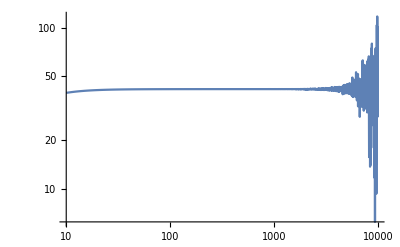

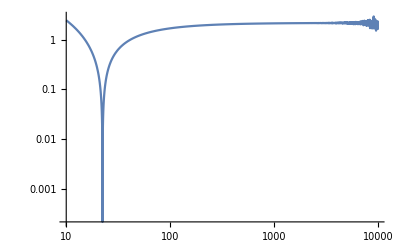

```mathematica
LogLogPlot[{
Abs[TestIntegrand[{0.6688633156907742,0.04471926097515777,0.125,0.5024753081896103,0.9552807390248423+1/ϵ,0.625},ParameterisationB]]
},{ϵ,10,10000},PlotRange->All]
```

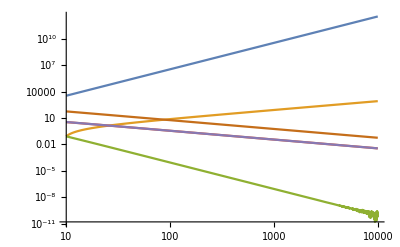

```mathematica
LogLogPlot[{
Abs[TestIntegrand[{0.5,-0.2,-0.3,0.25,0.0+1/10,0.01},ParameterisationA,IncludeVirtual->False,IncludeReal->True]]*(1+(ϵ^3-10)),
Abs[TestIntegrand[{0.5,-0.2,-0.3,0.25,0.0+1/10,0.01},ParameterisationA]]*(1+(ϵ-10)),
Abs[TestIntegrand[{0.5,-0.2,-0.3,0.25,0.0+1/ϵ,0.01},ParameterisationA]],
Abs[TestIntegrand[{0.5,-0.2,-0.3,0.25,0.0+1/ϵ,0.01},ParameterisationA,IncludeVirtual->False,IncludeReal->True]],
Abs[TestIntegrand[{0.5,-0.2,-0.3,0.25,0.0+1/ϵ,0.01},ParameterisationA,IncludeVirtual->True,IncludeReal->False]],
Abs[(ParameterisationA@@{0.5,-0.2,-0.3,0.25,0.0+1/ϵ,0.01})["jacobian"]]
},{ϵ,10,10000},PlotRange->All]
```

```mathematica
Join[(InvSphericalMap@@N[{2/10,2/10,2}])["xs"],(InvSphericalMap@@N[{-1/10,-1/10,-1}])["xs"]]
```

{0.668863,0.0447193,0.125,0.502475,0.955281,0.625}

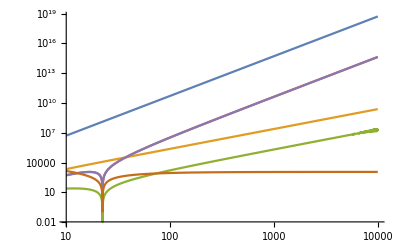

```mathematica
LogLogPlot[{
Abs[TestIntegrand[{0.6688633156907742,0.04471926097515777,0.125,0.5024753081896103,0.9552807390248423+1/10,0.625},ParameterisationB,IncludeVirtual->False,IncludeReal->True]]*(1+(ϵ^4-10)),
Abs[TestIntegrand[{0.6688633156907742,0.04471926097515777,0.125,0.5024753081896103,0.9552807390248423+1/10,0.625},ParameterisationB]]*(1+(ϵ^2-10)),
Abs[TestIntegrand[{0.6688633156907742,0.04471926097515777,0.125,0.5024753081896103,0.9552807390248423+1/ϵ,0.625},ParameterisationB]],
Abs[TestIntegrand[{0.6688633156907742,0.04471926097515777,0.125,0.5024753081896103,0.9552807390248423+1/ϵ,0.625},ParameterisationB,IncludeVirtual->False,IncludeReal->True]],
Abs[TestIntegrand[{0.6688633156907742,0.04471926097515777,0.125,0.5024753081896103,0.9552807390248423+1/ϵ,0.625},ParameterisationB,IncludeVirtual->True,IncludeReal->False]],
Abs[(ParameterisationB@@{0.6688633156907742,0.04471926097515777,0.125,0.5024753081896103,0.9552807390248423+1/ϵ,0.625})["jacobian"]]
}
,{ϵ,10,10000},PlotRange->All]
```

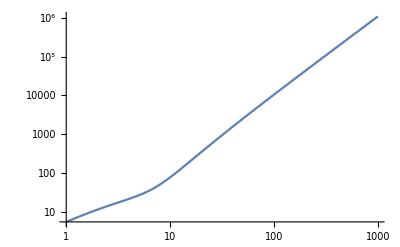

```mathematica
LogLogPlot[Abs[TestIntegrand[Join[(InvSphericalMap@@N[{2/10,2/10,2}])["xs"],(InvSphericalMap@@N[{-1/10,-1/10+1/ϵ,-1}])["xs"]],ParameterisationB]],{ϵ,1,1000},PlotRange->All]
```

```mathematica
Manipulate[TestIntegrand[{xkr,xkθ,xkϕ,xlr,xlθ,xlϕ},ParameterisationB],
{{xkr,0.5},0,1},
{{xkθ,0.5},0,1},
{{xkϕ,0.5},0,1},
{{xlr,0.5},0,1},
{{xlθ,0.5},0,1},
{{xlϕ,0.5},0,1}
]
```

itg=0.0035534870516208137

jac=2074.8575558614284

itg=0.0035534870516208137

jac=2074.8575558614284

Res=7.372979458711195

```mathematica
ClearAll[ThisIntegrand,IntermediateResult,IntegralResult,target];
ThisIntegrand[x1_?NumberQ,x2_?NumberQ,x3_?NumberQ,x4_?NumberQ,x5_?NumberQ,x6_?NumberQ]:=TestIntegrand[{x1,x2,x3,x4,x5,x6},ParameterisationB];
(*MCPoints={};*)
target=Null;
rBoundMin=0.0+10^-10;rBoundMax=0.75-10^-10;
BoundMin=0.0+10^-10;BoundMax=1.0-10^-10;
IntermediateResult=0;
IntegralResult=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->4,MaxPoints->statistics,MaxRecursion->100000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3},RealCutRescalingIntegrand[{x1,x2,x3},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3},0,2,False]}]*)
];
MyPrint["Result for "<>ToString[statistics,InputForm]<>" sample points: "<>ToString[IntermediateResult,InputForm]<>If[
target===Null, ""," vs target="<>ToString[target,InputForm]<>" (Δ_rel="<>ToString[SetPrecision[((IntermediateResult-target)/target)*100,3]]<>"%, Δ_Abs="<>ToString[SetPrecision[IntermediateResult-target,3]]<>")"
]];
statistics->IntermediateResult
,{statistics,{1000,5000,10000,50000,100000,500000,1000000,10000000,100000000}}]
]
```

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained 3252.79 and 3001.18 for the integral and error estimates.

Result for 1000 sample points: 3252.793973501106

NIntegrate::maxp: The integral failed to converge after 5100 integrand evaluations. NIntegrate obtained 950.654 and 201.346 for the integral and error estimates.

Result for 5000 sample points: 950.6544897472077

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 331.492 and 27.906 for the integral and error estimates.

Result for 10000 sample points: 331.49240985295063

$Aborted

```mathematica
ClearAll[ThisIntegrand,IntermediateResult,IntegralResult,target];
ThisIntegrand[x1_?NumberQ,x2_?NumberQ,x3_?NumberQ,x4_?NumberQ,x5_?NumberQ,x6_?NumberQ]:=TestIntegrand[{x1,x2,x3,x4,x5,x6},ParameterisationA];
(*MCPoints={};*)
target=Null;
rBoundMin=0.0+10^-10;rBoundMax=0.75-10^-10;
BoundMin=0.0+10^-10;BoundMax=1.0-10^-10;
IntermediateResult=0;
IntegralResult=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->4,MaxPoints->statistics,MaxRecursion->100000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3},RealCutRescalingIntegrand[{x1,x2,x3},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3},0,2,False]}]*)
];
MyPrint["Result for "<>ToString[statistics,InputForm]<>" sample points: "<>ToString[IntermediateResult,InputForm]<>If[
target===Null, ""," vs target="<>ToString[target,InputForm]<>" (Δ_rel="<>ToString[SetPrecision[((IntermediateResult-target)/target)*100,3]]<>"%, Δ_Abs="<>ToString[SetPrecision[IntermediateResult-target,3]]<>")"
]];
statistics->IntermediateResult
,{statistics,{1000,5000,10000,50000,100000,500000,1000000,10000000,100000000}}]
]
```

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained 331.872 and 119.37 for the integral and error estimates.

Result for 1000 sample points: 331.8717870764855

NIntegrate::maxp: The integral failed to converge after 5100 integrand evaluations. NIntegrate obtained 3616.79 and 3092.38 for the integral and error estimates.

Result for 5000 sample points: 3616.7865761766325

$Aborted

```mathematica
ClearAll[ThisIntegrand,IntermediateResult,IntegralResult,target];
ThisIntegrand[x1_?NumberQ,x2_?NumberQ,x3_?NumberQ,x4_?NumberQ,x5_?NumberQ,x6_?NumberQ]:=TestIntegrand[{x1,x2,x3,x4,x5,x6},ParameterisationB];
(*MCPoints={};*)
target=Null;
rBoundMin=0.0+10^-10;rBoundMax=0.75-10^-10;
BoundMin=0.0+10^-10;BoundMax=1.0-10^-10;
IntermediateResult=0;
IntegralResult=Association[Table[
IntermediateResult=NIntegrate[
ThisIntegrand[0.1,0.2,0.3,x4,x5,x6],
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->4,MaxPoints->statistics,MaxRecursion->100000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3},RealCutRescalingIntegrand[{x1,x2,x3},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3},0,2,False]}]*)
];
MyPrint["Result for "<>ToString[statistics,InputForm]<>" sample points: "<>ToString[IntermediateResult,InputForm]<>If[
target===Null, ""," vs target="<>ToString[target,InputForm]<>" (Δ_rel="<>ToString[SetPrecision[((IntermediateResult-target)/target)*100,3]]<>"%, Δ_Abs="<>ToString[SetPrecision[IntermediateResult-target,3]]<>")"
]];
statistics->IntermediateResult
,{statistics,{1000,5000,10000,50000,100000,500000,1000000,10000000,100000000}}]
]
```

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained -995.789 and 208.625 for the integral and error estimates.

Result for 1000 sample points: -995.788615560037

NIntegrate::maxp: The integral failed to converge after 5100 integrand evaluations. NIntegrate obtained -2159.2 and 118.124 for the integral and error estimates.

Result for 5000 sample points: -2159.200724880072

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained -2245.75 and 94.9652 for the integral and error estimates.

Result for 10000 sample points: -2245.7500878605238

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 5.36714×10^16 and 9.17145×10^14 for the integral and error estimates.

Result for 50000 sample points: 5.367135130233671*^16

$Aborted

```mathematica
ClearAll[ThisIntegrand,IntermediateResult,IntegralResult,target];
ThisIntegrand[x1_?NumberQ,x2_?NumberQ,x3_?NumberQ,x4_?NumberQ,x5_?NumberQ,x6_?NumberQ]:=TestIntegrand[{x1,x2,x3,x4,x5,x6},ParameterisationA];
MCPoints={};
target=Null;
rBoundMin=0.0+10^-10;rBoundMax=0.75-10^-10;
BoundMin=0.0+10^-10;BoundMax=1.0-10^-10;
IntermediateResult=0;
IntegralResult=Association[Table[
MCPoints={};
IntermediateResult=NIntegrate[
ThisIntegrand[0.1,0.2,0.3,x4,x5,x6],
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->4,MaxPoints->statistics,MaxRecursion->100000
,EvaluationMonitor:>AppendTo[MCPoints,{{x4,x5,x6},ThisIntegrand[0.1,0.2,0.3,x4,x5,x6]}]
];
MyPrint["Result for "<>ToString[statistics,InputForm]<>" sample points: "<>ToString[IntermediateResult,InputForm]<>If[
target===Null, ""," vs target="<>ToString[target,InputForm]<>" (Δ_rel="<>ToString[SetPrecision[((IntermediateResult-target)/target)*100,3]]<>"%, Δ_Abs="<>ToString[SetPrecision[IntermediateResult-target,3]]<>")"
]];
statistics->IntermediateResult
,{statistics,{1000,5000,10000(*,50000,100000,500000,1000000,10000000,100000000*)}}]
]
```

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained -3077.4 and 852.435 for the integral and error estimates.

Result for 1000 sample points: -3077.397189254336

NIntegrate::maxp: The integral failed to converge after 5100 integrand evaluations. NIntegrate obtained -2257.61 and 294.332 for the integral and error estimates.

Result for 5000 sample points: -2257.607240993388

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 2.28304×10^17 and 2.27158×10^17 for the integral and error estimates.

Result for 10000 sample points: 2.283040412963817*^17

<|1000→-3077.4,5000→-2257.61,10000→2.28304×10^17|>

```mathematica
MCPoints
```

{{{0.319146,0.0248582,0.255657},3.81822},{{0.608306,0.297874,0.362452},5.37199},{{0.254205,0.317821,0.903995},92.394},{{0.00583455,0.124366,0.092605},1110.95},{{0.196976,0.589984,0.629963},406.678},16291,{{0.00346285,0.999971,0.0984458},9.14444×10^11},{{0.00466983,0.9998,0.0992531},-5.84901×10^7},{{0.00268148,0.999839,0.108819},-2.59166×10^9},{{0.00402814,0.999831,0.100152},-4.32977×10^8}}
 |  |  |  |

```mathematica
cLTD[prop]
```